## Spectral Decomposition

### Definitions

```mathematica
Clear[σ,ϕ,α,β,A2]
```

```mathematica
σSol = {σ->(3+Sqrt[5])/2};
```

```mathematica
σ/.σSol//N
1/σ/.σSol//N
1/σ^2/.σSol//N
```

2.61803

0.381966

0.145898

```mathematica
ϕDef={ϕ -> σ-1};
```

```mathematica
ϕ/.ϕDef/.σSol//Simplify
%//N
1/%
%^2
```

1/2 (1+√5)

1.61803

0.618034

0.381966

```mathematica
ϕSol={ϕ -> (1+Sqrt[5])/2};
```

```mathematica
αDef={α->1/Sqrt[Simplify[1+ϕ^2]]};
βDef={β->ϕ/Sqrt[Simplify[1+ϕ^2]]};
αβDef={α->1/Sqrt[Simplify[1+ϕ^2]],β->ϕ/Sqrt[Simplify[1+ϕ^2]]};
A2Def={A2->α+β };
```

```mathematica
α/.αDef/.ϕDef/.σSol//Simplify
%//N
%^2
```

√(2/(5+√5))

0.525731

0.276393

```mathematica
β/.βDef/.ϕDef/.σSol//Simplify
%//N
%^2
```

(1+√5)/(√(2 (5+√5)))

0.850651

0.723607

```mathematica
A2/.A2Def/.αDef/.βDef/.ϕDef/.σSol//Simplify
%//N
1/%
%^2
```

(3+√5)/(√(2 (5+√5)))

1.37638

0.726543

0.527864

```mathematica
αSol={α->Sqrt[2/(5+Sqrt[5])]};
βSol={β->(1+Sqrt[5])/Sqrt[2(5+Sqrt[5])]};
αβSol={α->Sqrt[2/(5+Sqrt[5])],β->(1+Sqrt[5])/Sqrt[2(5+Sqrt[5])]};
A2Sol={A2-> (3+Sqrt[5])/Sqrt[2(5+Sqrt[5])]};
```

### The space of piecewise analytic distributions

#### considerations

Perron-Frobenius maps piecewise polynomials to piecewise polynomials defined on the partition {[0,α[ , [α,α+β[}.

```mathematica
α/.αDef/.ϕDef/.σSol//N
```

0.525731

```mathematica
{(u/σ)/.{u-> 0},(u/σ)/.{u-> α}}/.αDef/.ϕDef/.σSol//N
{(u/σ+α)/.{u-> 0},(u/σ+α)/.{u-> α}}/.αDef/.ϕDef/.σSol//N
```

{0.,0.200811}

{0.525731,0.726543}

```mathematica
{(u/σ)/.{u-> α},(u/σ)/.{u-> A2}}/.A2Def/.αDef/.βDef/.ϕDef/.σSol//N
{(u/σ+α)/.{u-> α},(u/σ+α)/.{u-> A2}}/.A2Def/.αDef/.βDef/.ϕDef/.σSol//N
{(u/σ+β)/.{u-> α},(u/σ+β)/.{u-> A2}}/.A2Def/.αDef/.βDef/.ϕDef/.σSol//N
```

{0.200811,0.525731}

{0.726543,1.05146}

{1.05146,1.37638}

First let’s define two otherwise generic families of polynomials on [0,1[ and then them into the intervals [0,α[ and [α,α+β[, respectively. This generates two families each defined on one interval of the partition.

```mathematica
Subscript[Poly, A][n_Integer,u_]:=Sum[a[i](u/α)^i,{i,0,n}]
Subscript[Poly, B][n_Integer,u_]:=Sum[b[i]((u-α)/β)^i,{i,0,n}]
```

```mathematica
Poly[norm_,n_Integer,u_]:=Piecewise[{{Collect[ Subscript[Poly, A][n,u]/norm,u],0≤ u<α},{Collect[Subscript[Poly, B][n,u]/norm,u],α≤ u<A2}}]
```

```mathematica
ψ[n_Integer,m_Integer,u_]:=Indeterminate
𝕍[n_Integer]:= Indeterminate
```

#### order 0

Let’s consider the case of order 0. First we determine the ratio between the factors as well as the invariant measure of Perron-Frobenius.

```mathematica
Subscript[LPoly, A][0]=Collect[(Subscript[Poly, A][0,u/σ]+ Subscript[Poly, B][0,u/σ+α])/σ,u,Simplify]//Expand
Subscript[LPoly, B][0]=Collect[(Subscript[Poly, A][0,u/σ]+Subscript[Poly, B][0,u/σ+α]+Subscript[Poly, B][0,u/σ+β])/σ,u,Simplify]//Expand
```

a[0]/σ+b[0]/σ

a[0]/σ+(2 b[0])/σ

```mathematica
Subscript[eq, A][0]=Subscript[LPoly, A][0]==λ  Subscript[Poly, A][0,u]
Subscript[eq, B][0]=Subscript[LPoly, B][0]==λ Subscript[Poly, B][0,u]
```

a[0]/σ+b[0]/σ==λ a[0]

a[0]/σ+(2 b[0])/σ==λ b[0]

```mathematica
L[0]={{1,1},{1,2 }}/σ;
L[0]//TraditionalForm
J[0]={{1,0},{0,1}};
J[0]//TraditionalForm
```

(1/σ | 1/σ
1/σ | 2/σ)

(1 | 0
0 | 1)

We find the 2 eigenvalues.

```mathematica
Det[L[0]-λ J[0]]//Simplify
Collect[%,λ]
λSol[0]=Solve[%==0,λ]
λSol[0]/.σSol//Simplify
%//N
```

λ^2+1/σ^2-(3 λ)/σ

λ^2+1/σ^2-(3 λ)/σ

{{λ→(3-√5)/(2 σ)},{λ→(3+√5)/(2 σ)}}

{{λ→1/2 (7-3 √5)},{λ→1}}

{{λ→0.145898},{λ→1.}}

We find the 2 eigenvectors.

```mathematica
ρ[0]={
NullSpace[(L[0]-λ J[0])/.λSol[0][[1]]],
NullSpace[(L[0]-λ J[0])/.λSol[0][[2]]]
}//Simplify
ρ[0]/.αβSol//Simplify
ρSol[0]={
{a[0]-> ρ[0][[1,1,1]],b[0]-> ρ[0][[1,1,2]]},
{a[0]-> ρ[0][[2,1,1]],b[0]-> ρ[0][[2,1,2]]}
}/.αβSol//Simplify
%/.{c[1]->α^2,c[2]-> β^2}/.αβSol//Simplify
-ϕ^2/.ϕSol
```

{{{1/2 (-1-√5),1}},{{1/2 (-1+√5),1}}}

{{{1/2 (-1-√5),1}},{{1/2 (-1+√5),1}}}

{{a[0]→1/2 (-1-√5),b[0]→1},{a[0]→1/2 (-1+√5),b[0]→1}}

{{a[0]→1/2 (-1-√5),b[0]→1},{a[0]→1/2 (-1+√5),b[0]→1}}

-1/4 (1+√5)^2

The second eigenvector determines the invariant measure. We normalize it so that the integral is 1.

1.

Piecewise[{{0.618034, 0.≤u<0.525731}, {1., 0.525731≤u<1.37638}, {0., True}}]

1.17557

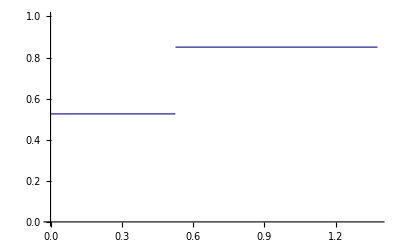

{a[0]→1/2 (-1+√5),b[0]→1}

```mathematica
λ/.λSol[0][[2]]/.σSol//N
f[norm_,u_]:=Poly[norm,0,u]/.ρSol[0][[2]]/.A2Sol/.αβSol/.σSol
f[1,u]//N
norm=Integrate[f[1,u]//N,{u,0,A2/.A2Sol}]//N//Chop
Plot[f[norm,u]//N,{u,0,A2/.A2Sol},PlotRange->{{0,A2/.A2Sol},{0,1}},ImageSize->Scaled[0.5]]//N
ρSol[0][[2]]
```

The first eigenvector determines a decaying mode. The corresponding measures of the two partition cells are the opposite of each other. We normalize it so that the absolute value of each measure is 1/2.

```mathematica
ψ[1,1,u_]:=Poly[1.1755705045849463,0,u]/.{a[0]->1/2 (-1+√5),b[0]->1}/.A2Sol/.αβSol/.σSol//N
ψ[1,1,u]
𝕍[1]:={1.,1}
```

Piecewise[{{0.525731, 0.≤u<0.525731}, {0.850651, 0.525731≤u<1.37638}, {0., True}}]

0.145898

Piecewise[{{-1.61803, 0.≤u<0.525731}, {1., 0.525731≤u<1.37638}, {0., True}}]

0

1.7013

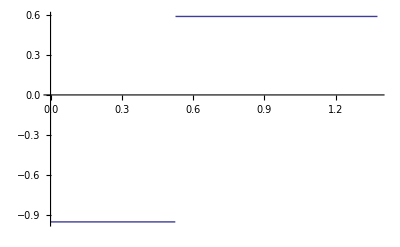

{a[0]→1/2 (-1-√5),b[0]→1}

```mathematica
λ/.λSol[0][[1]]/.σSol//N
f[norm_,u_]:=Poly[norm,0,u]/.ρSol[0][[1]]/.A2Sol/.αβSol/.ϕSol/.σSol
f[1,u]//N
Integrate[f[1,u]//N,{u,0,A2/.A2Sol}]//N//Chop
halfnorm=2Integrate[f [1,u]//N,{u,α/.αβSol,A2/.A2Sol}]//N//Chop
Plot[f[halfnorm,u]//N,{u,0,A2/.A2Sol},PlotRange->Full,ImageSize->Scaled[0.5]]//N
ρSol[0][[1]]
```

```mathematica
ψ[3,1,u_]:=Poly[1.7013016167040798,0,u]/.{a[0]->1/2 (-1-√5),b[0]->1}/.A2Sol/.αβSol/.ϕSol/.σSol//N
ψ[3,1,u]
𝕍[3]:={0.14589803375031543,1}
```

Piecewise[{{-0.951057, 0.≤u<0.525731}, {0.587785, 0.525731≤u<1.37638}, {0., True}}]

#### order 1

Let’s consider the case of order 1.

```mathematica
Subscript[LPoly, A][1]=Collect[(Subscript[Poly, A][1,u/σ]+Subscript[Poly, B][1,u/σ+α])/σ,u,Simplify]
Subscript[LPoly, B][1]=Collect[(Subscript[Poly, A][1,u/σ]+Subscript[Poly, B][1,u/σ+α]+Subscript[Poly, B][1,u/σ+β])/σ,u,Simplify]
```

(a[0]+b[0])/σ+(u (β a[1]+α b[1]))/(α β σ^2)

(u (β a[1]+2 α b[1]))/(α β σ^2)+(a[0]+2 b[0]+b[1]-(α b[1])/β)/σ

```mathematica
Subscript[eq, A][1,0]=Coefficient[Expand[Subscript[LPoly, A][1]],u,0]==λ Coefficient[Subscript[Poly, A][1,u],u,0]
Subscript[eq, B][1,0]=Coefficient[Expand[Subscript[LPoly, B][1]],u,0]==λ Coefficient[Subscript[Poly, B][1,u],u,0]
Subscript[eq, A][1,1]=Coefficient[Expand[Subscript[LPoly, A][1]],u,1]==λ Coefficient[Subscript[Poly, A][1,u],u,1]
Subscript[eq, B][1,1]=Coefficient[Expand[Subscript[LPoly, B][1]],u,1]==λ Coefficient[Subscript[Poly, B][1,u],u,1]
```

a[0]/σ+b[0]/σ==λ a[0]

a[0]/σ+(2 b[0])/σ+b[1]/σ-(α b[1])/(β σ)==λ (b[0]-(α b[1])/β)

a[1]/(α σ^2)+b[1]/(β σ^2)==(λ a[1])/α

a[1]/(α σ^2)+(2 b[1])/(β σ^2)==(λ b[1])/β

```mathematica
L[1]={{1,1,0,0},{1,2,0,1-α /β},{0,0,1/(α σ),1/(β σ)},{0,0,1/(α σ),2/(β σ)}}/σ;
%//Simplify//TraditionalForm
J[1]={{1,0,0,0},{0,1,0,-α /β},{0,0,1/α,0},{0,0,0,1/β}};
%//TraditionalForm
```

(1/σ | 1/σ | 0 | 0
1/σ | 2/σ | 0 | (β-α)/(β σ)
0 | 0 | 1/(α σ^2) | 1/(β σ^2)
0 | 0 | 1/(α σ^2) | 2/(β σ^2))

(1 | 0 | 0 | 0
0 | 1 | 0 | -α/β
0 | 0 | 1/α | 0
0 | 0 | 0 | 1/β)

```mathematica
Det[L[1]-λ J[1]]//Simplify
Collect[%,λ]/.αDef/.βDef/.ϕDef
λSol[1]=Solve[%==0,λ]
%/.σSol//Simplify
```

(1+λ^4 σ^6-3 λ σ (1+σ)-3 λ^3 σ^4 (1+σ)+λ^2 σ^2 (1+9 σ+σ^2))/(α β σ^6)

(λ^4 (1+(-1+σ)^2))/(-1+σ)+(1+(-1+σ)^2)/((-1+σ) σ^6)-(3 λ (1+(-1+σ)^2) (1+σ))/((-1+σ) σ^5)-(3 λ^3 (1+(-1+σ)^2) (1+σ))/((-1+σ) σ^2)+(λ^2 (1+(-1+σ)^2) (1+9 σ+σ^2))/((-1+σ) σ^4)

{{λ→(3-√5)/(2 σ^2)},{λ→(3+√5)/(2 σ^2)},{λ→(3-√5)/(2 σ)},{λ→(3+√5)/(2 σ)}}

{{λ→9-4 √5},{λ→2/(3+√5)},{λ→1/2 (7-3 √5)},{λ→1}}

```mathematica
λ/.λSol[1]/.σSol//N//Chop
Table[1/σ^i,{i,0,3}]/.σSol//N
```

{0.0557281,0.381966,0.145898,1.}

{1.,0.381966,0.145898,0.0557281}

```mathematica
ρ[1]={
NullSpace[(L[1]-λ J[1])/.λSol[1][[1]]],
NullSpace[(L[1]-λ J[1])/.λSol[1][[2]]],
NullSpace[(L[1]-λ J[1])/.λSol[1][[3]]],
NullSpace[(L[1]-λ J[1])/.λSol[1][[4]]]
}//Simplify
ρSol[1]={
{a[0]-> ρ[1][[1,1,1]],b[0]-> ρ[1][[1,1,2]],a[1]-> ρ[1][[1,1,3]],b[1]-> ρ[1][[1,1,4]]},
{a[0]->ρ[1][[2,1,1]],b[0]-> ρ[1][[2,1,2]],a[1]-> ρ[1][[2,1,3]],b[1]-> ρ[1][[2,1,4]]},
{a[0]-> ρ[1][[3,1,1]],b[0]->ρ[1][[3,1,2]],a[1]-> ρ[1][[3,1,3]],b[1]->ρ[1][[3,1,4]]},
{a[0]-> ρ[1][[4,1,1]],b[0]-> ρ[1][[4,1,2]],a[1]-> ρ[1][[4,1,3]],b[1]-> ρ[1][[4,1,4]]}
}/.αβSol/.σSol//Simplify
```

{{{(σ (2 β σ-α (-3+√5+2 σ)))/(β (-1+σ) (-7+3 √5+2 σ)),((-3+√5+2 σ) (-2 β σ+α (-3+√5+2 σ)))/(2 β (-1+σ) (-7+3 √5+2 σ)),-((1+√5) α)/(2 β),1}},{{(σ (α (3+√5-2 σ)+2 β σ))/(β (-1+σ) (-7-3 √5+2 σ)),-((3+√5-2 σ) (α (3+√5-2 σ)+2 β σ))/(2 β (7+3 √5-2 σ) (-1+σ)),((-1+√5) α)/(2 β),1}},{{1/2 (-1-√5),1,0,0}},{{1/2 (-1+√5),1,0,0}}}

{{a[0]→1/4 (1+√5),b[0]→1/4 (-5+√5),a[1]→-1,b[1]→1},{a[0]→-1,b[0]→0,a[1]→1/2 (3-√5),b[1]→1},{a[0]→1/2 (-1-√5),b[0]→1,a[1]→0,b[1]→0},{a[0]→1/2 (-1+√5),b[0]→1,a[1]→0,b[1]→0}}

```mathematica
λ/.λSol[1][[4]]/.σSol//N//Chop
f[norm_,u_]:=Poly[norm,1,u]/.ρSol[1][[4]]/.A2Sol/.αβSol/.ϕSol/.σSol
f[1,u]//N
norm=Integrate[f[1,u]//N,{u,0,A2/.A2Sol}]//N//Chop
f[norm,u]//N
ψ[1,1,u]
```

1.

Piecewise[{{0.618034, 0.≤u<0.525731}, {1., 0.525731≤u<1.37638}, {0., True}}]

1.17557

Piecewise[{{0.525731, 0.≤u<0.525731}, {0.850651, 0.525731≤u<1.37638}, {0., True}}]

Piecewise[{{0.525731, 0.≤u<0.525731}, {0.850651, 0.525731≤u<1.37638}, {0., True}}]

0.381966

0.381966

Piecewise[{{-1.+0.726543 u, 0.≤u<0.525731}, {-0.618034+1.17557 u, 0.525731≤u<1.37638}, {0., True}}]

0

0.850651

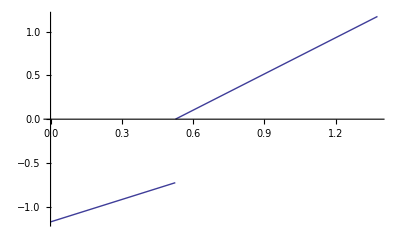

Piecewise[{{-1.17557+0.854102 u, 0.≤u<0.525731}, {-0.726543+1.38197 u, 0.525731≤u<1.37638}, {0., True}}]

{a[0]→-1,b[0]→0,a[1]→1/2 (3-√5),b[1]→1}

```mathematica
λ/.λSol[1][[2]]/.σSol//N//Chop
1/σ/.σSol//N
f[norm_,u_]:=Poly[norm,1,u]/.ρSol[1][[2]]/.A2Sol/.αβSol/.ϕSol/.σSol
f[1,u]//N
Integrate[f[1,u]//N,{u,0,A2/.A2Sol}]//N//Chop
halfnorm=2*Integrate[f[1,u]//N,{u,α/.αSol,A2/.A2Sol}]//N//Chop
Plot[f[halfnorm,u]//N,{u,0,A2/.A2Sol},PlotRange->Full,ImageSize->Scaled[0.5]]
f[halfnorm,u]//N
ρSol[1][[2]]
```

```mathematica
ψ[2,1,u_]:=Poly[0.8506508083520398,1,u]/.{a[0]->-1,b[0]->0,a[1]->1/2 (3-√5),b[1]->1}/.A2Sol/.αβSol/.ϕSol/.σSol//N
ψ[2,1,u]
𝕍[2]:={1/σ/.σSol//N,1}
```

Piecewise[{{-1.17557+0.854102 u, 0.≤u<0.525731}, {-0.726543+1.38197 u, 0.525731≤u<1.37638}, {0., True}}]

```mathematica
λ/.λSol[1][[3]]/.σSol//N//Chop
1/σ^2/.σSol//N
f[norm_,u_]:=Poly[norm,1,u]/.ρSol[1][[3]]/.A2Sol/.αβSol/.ϕSol/.σSol
f[1,u]//N
Integrate[f[1,u]//N,{u,0,A2/.A2Sol}]//N//Chop
halfnorm=2*Integrate[f[1,u]//N,{u,α/.αSol,A2/.A2Sol}]//N//Chop
f[halfnorm,u]//N
ψ[3,1,u]
```

0.145898

0.145898

Piecewise[{{-1.61803, 0.≤u<0.525731}, {1., 0.525731≤u<1.37638}, {0., True}}]

0

1.7013

Piecewise[{{-0.951057, 0.≤u<0.525731}, {0.587785, 0.525731≤u<1.37638}, {0., True}}]

Piecewise[{{-1.11803, 0.≤u<0.525731}, {0.690983, 0.525731≤u<1.37638}, {0., True}}]

0.0557281

0.0557281

Piecewise[{{0.809017-1.90211 u, 0.≤u<0.525731}, {-1.30902+1.17557 u, 0.525731≤u<1.37638}, {0., True}}]

0

-0.32492

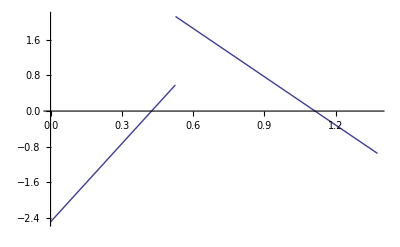

Piecewise[{{-2.4899+5.8541 u, 0.≤u<0.525731}, {4.02874-3.61803 u, 0.525731≤u<1.37638}, {0., True}}]

{a[0]→1/4 (1+√5),b[0]→1/4 (-5+√5),a[1]→-1,b[1]→1}

```mathematica
λ/.λSol[1][[1]]/.σSol//N//Chop
1/σ^3/.σSol//N
f[norm_,u_]:=Poly[norm,1,u]/.ρSol[1][[1]]/.A2Sol/.αβSol/.ϕSol/.σSol
f[1,u]//N
Integrate[f[1,u]//N,{u,0,A2/.A2Sol}]//N//Chop
halfnorm=2*Integrate[f[1,u]//N,{u,α/.αSol,A2/.A2Sol}]//N//Chop
Plot[f[halfnorm,u]//N,{u,0,A2/.A2Sol},PlotRange->Full,ImageSize->Scaled[0.5]]
f[halfnorm,u]//N
ρSol[1][[1]]
```

```mathematica
ψ[4,1,u_]:=Poly[-0.324919696232907,1,u]/.{a[0]->1/4 (1+√5),b[0]->1/4 (-5+√5),a[1]->-1,b[1]->1}/.A2Sol/.αβSol/.ϕSol/.σSol//N
ψ[4,1,u]
𝕍[4]:={1/σ^3/.σSol//N,1}
```

Piecewise[{{-2.4899+5.8541 u, 0.≤u<0.525731}, {4.02874-3.61803 u, 0.525731≤u<1.37638}, {0., True}}]

#### order 2

```mathematica
n=2;
Subscript[LPoly, A][n]=Collect[(Subscript[Poly, A][n,u/σ]+Subscript[Poly, B][n,u/σ+α])/σ,u,Simplify]
Subscript[LPoly, B][n]=Collect[(Subscript[Poly, A][n,u/σ]+Subscript[Poly, B][n,u/σ+α]+Subscript[Poly, B][n,u/σ+β])/σ,u,Simplify]
```

(a[0]+b[0])/σ+(u (β a[1]+α b[1]))/(α β σ^2)+(u^2 (a[2]/α^2+b[2]/β^2))/σ^3

(u^2 (a[2]/α^2+(2 b[2])/β^2))/σ^3+(u (β^2 a[1]-2 α^2 b[2]+2 α β (b[1]+b[2])))/(α β^2 σ^2)+(α^2 b[2]+β^2 (a[0]+2 b[0]+b[1]+b[2])-α β (b[1]+2 b[2]))/(β^2 σ)

```mathematica
vector[n]=Table[{a[i],b[i]},{i,0,n}]//Flatten;
```

```mathematica
Subscript[lhs, A][n,i_]:=Coefficient[Subscript[LPoly, A][n],u,i]
Subscript[lhs, B][n,i_]:=Coefficient[Subscript[LPoly, B][n],u,i]
L[n]={};
Do[
L[n]=Append[L[n],Coefficient[Subscript[lhs, A][n,i],#]&/@vector[n]];
L[n]=Append[L[n],Coefficient[Subscript[lhs, B][n,i],#]&/@vector[n]],
{i,0,n}]
L[n]//Simplify//TraditionalForm
Subscript[rhs, A][n,i_]:=Coefficient[Subscript[Poly, A][n,u],u,i]
Subscript[rhs, B][n,i_]:=Coefficient[Subscript[Poly, B][n,u],u,i]
J[n]={};
Do[
J[n]=Append[J[n],Coefficient[Subscript[rhs, A][n,i],#]&/@vector[n]];
J[n]=Append[J[n],Coefficient[Subscript[rhs, B][n,i],#]&/@vector[n]],
{i,0,n}]
J[n]//TraditionalForm
```

(1/σ | 1/σ | 0 | 0 | 0 | 0
1/σ | 2/σ | 0 | (β-α)/(β σ) | 0 | (α-β)^2/(β^2 σ)
0 | 0 | 1/(α σ^2) | 1/(β σ^2) | 0 | 0
0 | 0 | 1/(α σ^2) | 2/(β σ^2) | 0 | -(2 (α-β))/(β^2 σ^2)
0 | 0 | 0 | 0 | 1/(α^2 σ^3) | 1/(β^2 σ^3)
0 | 0 | 0 | 0 | 1/(α^2 σ^3) | 2/(β^2 σ^3))

(1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | -α/β | 0 | α^2/β^2
0 | 0 | 1/α | 0 | 0 | 0
0 | 0 | 0 | 1/β | 0 | -(2 α)/β^2
0 | 0 | 0 | 0 | 1/α^2 | 0
0 | 0 | 0 | 0 | 0 | 1/β^2)

```mathematica
determinant[n]=Det[L[n]-λ J[n]]//Simplify
```

1/(α^3 β^3 σ^12)(1+λ^6 σ^12-3 λ σ (1+σ+σ^2)-3 λ^5 σ^9 (1+σ+σ^2)-3 λ^3 σ^4 (1+2 σ+9 σ^2+2 σ^3+σ^4)+λ^2 σ^2 (1+9 σ+10 σ^2+9 σ^3+σ^4)+λ^4 σ^6 (1+9 σ+10 σ^2+9 σ^3+σ^4))

```mathematica
λSol[n]=Solve[determinant[n]==0,λ]
```

{{λ→(3-√5)/(2 σ^3)},{λ→(3+√5)/(2 σ^3)},{λ→(3-√5)/(2 σ^2)},{λ→(3+√5)/(2 σ^2)},{λ→(3-√5)/(2 σ)},{λ→(3+√5)/(2 σ)}}

```mathematica
λSol[n]/.σSol//Simplify
%//N
```

{{λ→1/2 (47-21 √5)},{λ→4/(3+√5)^2},{λ→9-4 √5},{λ→2/(3+√5)},{λ→1/2 (7-3 √5)},{λ→1}}

{{λ→0.0212862},{λ→0.145898},{λ→0.0557281},{λ→0.381966},{λ→0.145898},{λ→1.}}

```mathematica
L[n]/.αβSol/.σSol;
LN[n]=(L[n]/.αβSol/.σSol)//N//Chop
J[n]/.αβSol/.σSol;
JN[n]=(J[n]/.αβSol/.σSol)//N//Chop
```

{{0.381966,0.381966,0,0,0,0},{0.381966,0.763932,0,0.145898,0,0.0557281},{0,0,0.277515,0.171513,0,0},{0,0,0.277515,0.343027,0,0.131025},{0,0,0,0,0.201626,0.0770143},{0,0,0,0,0.201626,0.154029}}

{{1.,0,0,0,0,0},{0,1.,0,-0.618034,0,0.381966},{0,0,1.90211,0,0,0},{0,0,0,1.17557,0,-1.45309},{0,0,0,0,3.61803,0},{0,0,0,0,0,1.38197}}

```mathematica
ρ[n]=Table[
NullSpace[((L[n]/.αβSol/.σSol)-λ (J[n]/.αβSol/.σSol))/.λSol[n][[i]]/.σSol],
{i,Length[λSol[n]]}];
ρ[n]=%//N//Chop
λSol[n]/.σSol//Simplify;
%//N
```

{{{-0.539345,0.509288,1.,-1.38197,-0.618034,1.}},{{0,0,-1.23607,0,0.236068,1.},{-1.61803,1.,0,0,0,0}},{{0.809017,-0.690983,-1.,1.,0,0}},{{-1.,0,0.381966,1.,0,0}},{{0,0,-1.23607,0,0.236068,1.},{-1.61803,1.,0,0,0,0}},{{0.618034,1.,0,0,0,0}}}

{{λ→0.0212862},{λ→0.145898},{λ→0.0557281},{λ→0.381966},{λ→0.145898},{λ→1.}}

```mathematica
l=6;
λ/.λSol[n][[l]]/.σSol
f[norm_,u_]:=Poly[norm,n,u]/.Flatten[Table[{vector[n][[i]]->  ρ[n][[l,1,i]]},{i,Length[vector[n]]}]]/.A2Sol/.αβSol/.ϕSol/.σSol
f[1,u]//N
norm=Integrate[f[1,u]//N,{u,0,A2/.A2Sol//N}]//N//Chop
f[norm,u]//N
ψ[1,1,u]
```

1

Piecewise[{{0.618034, 0.≤u<0.525731}, {1., 0.525731≤u<1.37638}, {0., True}}]

1.17557

Piecewise[{{0.525731, 0.≤u<0.525731}, {0.850651, 0.525731≤u<1.37638}, {0., True}}]

Piecewise[{{0.525731, 0.≤u<0.525731}, {0.850651, 0.525731≤u<1.37638}, {0., True}}]

```mathematica
l=4;
λ/.λSol[n][[l]]/.σSol//N
1/σ/.σSol//N
f[norm_,u_]:=Poly[norm,n,u]/.Flatten[Table[{vector[n][[i]]->  ρ[n][[l,1,i]]},{i,Length[vector[n]]}]]/.A2Sol/.αβSol/.ϕSol/.σSol
f[1,u]//N
Integrate[f[1,u]//N,{u,0,A2/.A2Sol}]//N//Chop
halfnorm=2*Integrate[f[1,u]//N,{u,α/.αSol,A2/.A2Sol}]//N//Chop
f[halfnorm,u]//N
ψ[2,1,u]
```

0.381966

0.381966

Piecewise[{{-1.+0.726543 u, 0.≤u<0.525731}, {-0.618034+1.17557 u, 0.525731≤u<1.37638}, {0., True}}]

0

0.850651

Piecewise[{{-1.17557+0.854102 u, 0.≤u<0.525731}, {-0.726543+1.38197 u, 0.525731≤u<1.37638}, {0., True}}]

Piecewise[{{-1.17557+0.854102 u, 0.≤u<0.525731}, {-0.726543+1.38197 u, 0.525731≤u<1.37638}, {0., True}}]

```mathematica
l=5;
λ/.λSol[n][[l]]/.σSol//N
f[norm_,u_]:=Poly[norm,n,u]/.Flatten[Table[{vector[n][[i]]->  ρ[n][[l,2,i]]},{i,Length[vector[n]]}]]/.A2Sol/.αβSol/.ϕSol/.σSol
f[1,u]//N
Integrate[f[1,u]//N,{u,0,A2/.A2Sol}]//N//Chop
halfnorm=2*Integrate[f[1,u]//N,{u,α/.αSol,A2/.A2Sol}]//N//Chop
f[halfnorm,u]//N
ψ[3,1,u]
```

0.145898

Piecewise[{{-1.61803, 0.≤u<0.525731}, {1., 0.525731≤u<1.37638}, {0., True}}]

0

1.7013

Piecewise[{{-0.951057, 0.≤u<0.525731}, {0.587785, 0.525731≤u<1.37638}, {0., True}}]

Piecewise[{{-0.951057, 0.≤u<0.525731}, {0.587785, 0.525731≤u<1.37638}, {0., True}}]

0.145898

0.145898

Piecewise[{{-2.35114 u+0.854102 u^2, 0.≤u<0.525731}, {0.381966-1.45309 u+1.38197 u^2, 0.525731≤u<1.37638}, {0., True}}]

0

0.567101

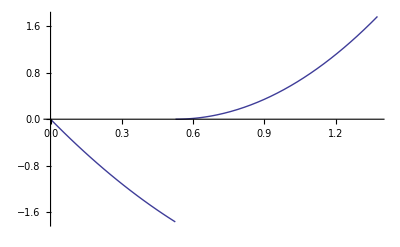

Piecewise[{{0.-4.1459 u+1.50609 u^2, 0.≤u<0.525731}, {0.673542-2.56231 u+2.4369 u^2, 0.525731≤u<1.37638}, {0., True}}]

```mathematica
l=2;
λ/.λSol[n][[l]]/.σSol//N
1/σ^2/.σSol//N
f[norm_,u_]:=Poly[norm,n,u]/.Flatten[Table[{vector[n][[i]]->  ρ[n][[l,1,i]]},{i,Length[vector[n]]}]]/.A2Sol/.αβSol/.ϕSol/.σSol
f[1,u]//N
Integrate[f[1,u]//N,{u,0,A2/.A2Sol}]//N//Chop
halfnorm=2*Integrate[f[1,u]//N,{u,α/.αSol,A2/.A2Sol}]//N//Chop
Plot[f[halfnorm,u]//N,{u,0,A2/.A2Sol},PlotRange->Full,ImageSize->Scaled[0.5]]
f[halfnorm,u]//N
```

```mathematica
Flatten[Table[{vector[n][[i]]->  ρ[n][[l,1,i]]},{i,Length[vector[n]]}]]
```

{a[0]→0,b[0]→0,a[1]→-1.23607,b[1]→0,a[2]→0.236068,b[2]→1.}

```mathematica
ψ[3,2,u_]:=Poly[0.5671005389013598,2,u]/.{a[0]->0,b[0]->0,a[1]->-1.2360679774997896,b[1]->0,a[2]->0.2360679774997898,b[2]->1.}/.A2Sol/.αβSol/.ϕSol/.σSol//N
𝕍[3]:={1/σ^2/.σSol//N,2}
ψ[3,2,u]
```

Piecewise[{{0.-4.1459 u+1.50609 u^2, 0.≤u<0.525731}, {0.673542-2.56231 u+2.4369 u^2, 0.525731≤u<1.37638}, {0., True}}]

```mathematica
l=3;
λ/.λSol[n][[l]]/.σSol//N
f[norm_,u_]:=Poly[norm,n,u]/.Flatten[Table[{vector[n][[i]]->  ρ[n][[l,1,i]]},{i,Length[vector[n]]}]]/.A2Sol/.αβSol/.ϕSol/.σSol
f[1,u]//N
Integrate[f[1,u]//N,{u,0,A2/.A2Sol}]//N//Chop
halfnorm=2*Integrate[f[1,u]//N,{u,α/.αSol,A2/.A2Sol}]//N//Chop
f[halfnorm,u]//N
ψ[4,1,u]
```

0.0557281

Piecewise[{{0.809017-1.90211 u, 0.≤u<0.525731}, {-1.30902+1.17557 u, 0.525731≤u<1.37638}, {0., True}}]

0

-0.32492

Piecewise[{{-2.4899+5.8541 u, 0.≤u<0.525731}, {4.02874-3.61803 u, 0.525731≤u<1.37638}, {0., True}}]

Piecewise[{{-2.4899+5.8541 u, 0.≤u<0.525731}, {4.02874-3.61803 u, 0.525731≤u<1.37638}, {0., True}}]

0.0212862

0.0212862

Piecewise[{{-0.539345+1.90211 u-2.23607 u^2, 0.≤u<0.525731}, {1.74536-3.07768 u+1.38197 u^2, 0.525731≤u<1.37638}, {0., True}}]

0

0.257983

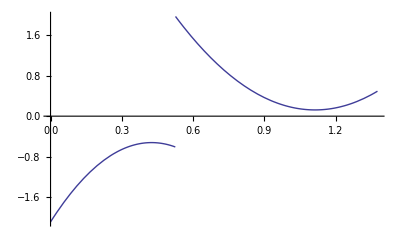

Piecewise[{{-2.09062+7.37303 u-8.66752 u^2, 0.≤u<0.525731}, {6.7654-11.9298 u+5.35682 u^2, 0.525731≤u<1.37638}, {0., True}}]

```mathematica
l=1;
λ/.λSol[n][[l]]/.σSol//N
1/σ^4/.σSol//N
f[norm_,u_]:=Poly[norm,n,u]/.Flatten[Table[{vector[n][[i]]->  ρ[n][[l,1,i]]},{i,Length[vector[n]]}]]/.A2Sol/.αβSol/.ϕSol/.σSol
f[1,u]//N
Integrate[f[1,u]//N,{u,0,A2/.A2Sol}]//N//Chop
halfnorm=2*Integrate[f[1,u]//N,{u,α/.αSol,A2/.A2Sol}]//N//Chop
Plot[f[halfnorm,u]//N,{u,0,A2/.A2Sol},PlotRange->Full,ImageSize->Scaled[0.5]]
f[halfnorm,u]//N
```

```mathematica
Flatten[Table[{vector[n][[i]]->  ρ[n][[l,1,i]]},{i,Length[vector[n]]}]]
```

{a[0]→-0.539345,b[0]→0.509288,a[1]→1.,b[1]→-1.38197,a[2]→-0.618034,b[2]→1.}

```mathematica
ψ[5,1,u_]:=Poly[0.2579825576041635,2,u]/.{a[0]->-0.5393446629166315,b[0]->0.5092880150001402,a[1]->1.,b[1]->-1.3819660112501058,a[2]->-0.6180339887498948,b[2]->1.}/.A2Sol/.αβSol/.ϕSol/.σSol//N
ψ[5,1,u]
𝕍[5]:={1/σ^4/.σSol//N,1}
```

Piecewise[{{-2.09062+7.37303 u-8.66752 u^2, 0.≤u<0.525731}, {6.7654-11.9298 u+5.35682 u^2, 0.525731≤u<1.37638}, {0., True}}]

```mathematica
Integrate[ψ[5,1,u][[1,1,1]]//N,{u,0,α/.αSol}]//N//Chop
Integrate[ψ[5,1,u][[1,2,1]]//N,{u,α/.αSol,A2/.A2Sol}]//N//Chop
```

-0.5

0.5

#### order 3

```mathematica
n=3;
Subscript[LPoly, A][n]=Collect[(Subscript[Poly, A][n,u/σ]+Subscript[Poly, B][n,u/σ+α])/σ,u,Simplify]
Subscript[LPoly, B][n]=Collect[(Subscript[Poly, A][n,u/σ]+Subscript[Poly, B][n,u/σ+α]+Subscript[Poly, B][n,u/σ+β])/σ,u,Simplify]
```

(a[0]+b[0])/σ+(u (β a[1]+α b[1]))/(α β σ^2)+(u^2 (a[2]/α^2+b[2]/β^2))/σ^3+(u^3 (a[3]/α^3+b[3]/β^3))/σ^4

(u^3 (a[3]/α^3+(2 b[3])/β^3))/σ^4+(u^2 (β^3 a[2]-3 α^3 b[3]+α^2 β (2 b[2]+3 b[3])))/(α^2 β^3 σ^3)+(-α^3 b[3]+β^3 (a[0]+2 b[0]+b[1]+b[2]+b[3])+α^2 β (b[2]+3 b[3])-α β^2 (b[1]+2 b[2]+3 b[3]))/(β^3 σ)+(u (β^3 a[1]+3 α^3 b[3]-2 α^2 β (b[2]+3 b[3])+α β^2 (2 b[1]+2 b[2]+3 b[3])))/(α β^3 σ^2)

```mathematica
vector[n]=Table[{a[i],b[i]},{i,0,n}]//Flatten;
```

```mathematica
Subscript[lhs, A][n,i_]:=Coefficient[Subscript[LPoly, A][n],u,i]
Subscript[lhs, B][n,i_]:=Coefficient[Subscript[LPoly, B][n],u,i]
L[n]={};
Do[
L[n]=Append[L[n],Coefficient[Subscript[lhs, A][n,i],#]&/@vector[n]];
L[n]=Append[L[n],Coefficient[Subscript[lhs, B][n,i],#]&/@vector[n]],
{i,0,n}]
L[n]//Simplify//TraditionalForm
Subscript[rhs, A][n,i_]:=Coefficient[Subscript[Poly, A][n,u],u,i]
Subscript[rhs, B][n,i_]:=Coefficient[Subscript[Poly, B][n,u],u,i]
J[n]={};
Do[
J[n]=Append[J[n],Coefficient[Subscript[rhs, A][n,i],#]&/@vector[n]];
J[n]=Append[J[n],Coefficient[Subscript[rhs, B][n,i],#]&/@vector[n]],
{i,0,n}]
J[n]//TraditionalForm
```

(1/σ | 1/σ | 0 | 0 | 0 | 0 | 0 | 0
1/σ | 2/σ | 0 | (β-α)/(β σ) | 0 | (α-β)^2/(β^2 σ) | 0 | -(α-β)^3/(β^3 σ)
0 | 0 | 1/(α σ^2) | 1/(β σ^2) | 0 | 0 | 0 | 0
0 | 0 | 1/(α σ^2) | 2/(β σ^2) | 0 | -(2 (α-β))/(β^2 σ^2) | 0 | (3 (α-β)^2)/(β^3 σ^2)
0 | 0 | 0 | 0 | 1/(α^2 σ^3) | 1/(β^2 σ^3) | 0 | 0
0 | 0 | 0 | 0 | 1/(α^2 σ^3) | 2/(β^2 σ^3) | 0 | -(3 (α-β))/(β^3 σ^3)
0 | 0 | 0 | 0 | 0 | 0 | 1/(α^3 σ^4) | 1/(β^3 σ^4)
0 | 0 | 0 | 0 | 0 | 0 | 1/(α^3 σ^4) | 2/(β^3 σ^4))

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | -α/β | 0 | α^2/β^2 | 0 | -α^3/β^3
0 | 0 | 1/α | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/β | 0 | -(2 α)/β^2 | 0 | (3 α^2)/β^3
0 | 0 | 0 | 0 | 1/α^2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/β^2 | 0 | -(3 α)/β^3
0 | 0 | 0 | 0 | 0 | 0 | 1/α^3 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/β^3)

```mathematica
determinant[n]=Det[L[n]-λ J[n]]//Simplify
```

1/(α^6 β^6 σ^20)(1+λ^8 σ^20-3 λ σ (1+σ+σ^2+σ^3)-3 λ^7 σ^16 (1+σ+σ^2+σ^3)+λ^2 σ^2 (1+9 σ+10 σ^2+18 σ^3+10 σ^4+9 σ^5+σ^6)+λ^6 σ^12 (1+9 σ+10 σ^2+18 σ^3+10 σ^4+9 σ^5+σ^6)-3 λ^3 σ^4 (1+2 σ+10 σ^2+11 σ^3+11 σ^4+10 σ^5+2 σ^6+σ^7)-3 λ^5 σ^9 (1+2 σ+10 σ^2+11 σ^3+11 σ^4+10 σ^5+2 σ^6+σ^7)+λ^4 σ^6 (1+9 σ+19 σ^2+27 σ^3+83 σ^4+27 σ^5+19 σ^6+9 σ^7+σ^8))

```mathematica
λSol[n]=Solve[determinant[n]==0,λ]
```

{{λ→(3-√5)/(2 σ^4)},{λ→(3+√5)/(2 σ^4)},{λ→(3-√5)/(2 σ^3)},{λ→(3+√5)/(2 σ^3)},{λ→(3-√5)/(2 σ^2)},{λ→(3+√5)/(2 σ^2)},{λ→(3-√5)/(2 σ)},{λ→(3+√5)/(2 σ)}}

```mathematica
λSol[n]/.σSol//Simplify
%//N
```

{{λ→1/2 (123-55 √5)},{λ→9-4 √5},{λ→1/2 (47-21 √5)},{λ→4/(3+√5)^2},{λ→9-4 √5},{λ→2/(3+√5)},{λ→1/2 (7-3 √5)},{λ→1}}

{{λ→0.00813062},{λ→0.0557281},{λ→0.0212862},{λ→0.145898},{λ→0.0557281},{λ→0.381966},{λ→0.145898},{λ→1.}}

```mathematica
LN[n]=(L[n]/.αβSol/.σSol)//N//Chop
JN[n]=(J[n]/.αβSol/.σSol)//N//Chop
```

{{0.381966,0.381966,0,0,0,0,0,0},{0.381966,0.763932,0,0.145898,0,0.0557281,0,0.0212862},{0,0,0.277515,0.171513,0,0,0,0},{0,0,0.277515,0.343027,0,0.131025,0,0.0750704},{0,0,0,0,0.201626,0.0770143,0,0},{0,0,0,0,0.201626,0.154029,0,0.0882506},{0,0,0,0,0,0,0.14649,0.0345816},{0,0,0,0,0,0,0.14649,0.0691632}}

{{1.,0,0,0,0,0,0,0},{0,1.,0,-0.618034,0,0.381966,0,-0.236068},{0,0,1.90211,0,0,0,0,0},{0,0,0,1.17557,0,-1.45309,0,1.34708},{0,0,0,0,3.61803,0,0,0},{0,0,0,0,0,1.38197,0,-2.56231},{0,0,0,0,0,0,6.88191,0},{0,0,0,0,0,0,0,1.6246}}

```mathematica
ρ[n]=Table[
NullSpace[(LN[n]-λ JN[n])/.λSol[n][[i]]/.σSol//N],
{i,Length[λSol[n]]}]//Chop
Length/@%
λSol[n]/.σSol//Simplify;
%//N
```

{{{-0.128192,0.125463,0.316907,-0.484191,-0.293789,0.656932,0.121048,-0.316907}},{{0.458907,-0.391954,-0.563396,0.563396,-0.0230654,0,0.00293673,0.0201287},{0.0500471,-0.0427453,0.062379,-0.062379,-0.745443,0,0.0949113,0.650532}},{{-0.245104,0.231445,0.454449,-0.628033,-0.280865,0.454449,0,0}},{{0.849709,-0.525149,-0.0361809,0,0.00690994,0.029271,0,0},{-0.0400222,0.0247351,-0.768156,0,0.146705,0.621451,0,0}},{{0.453515,-0.387348,-0.520613,0.520613,-0.239776,0,0.0305287,0.209247},{-0.0861644,0.0735932,0.224206,-0.224206,-0.706205,0,0.0899154,0.61629}},{{-0.682646,0,0.260748,0.682646,0,0,0,0}},{{0.816486,-0.504616,-0.215753,0,0.0412051,0.174548,0,0},{-0.238659,0.147499,-0.738121,0,0.140969,0.597152,0,0}},{{0.525731,0.850651,0,0,0,0,0,0}}}

{1,2,1,2,2,1,2,1}

{{λ→0.00813062},{λ→0.0557281},{λ→0.0212862},{λ→0.145898},{λ→0.0557281},{λ→0.381966},{λ→0.145898},{λ→1.}}

```mathematica
l=8;
λ/.λSol[n][[l]]/.σSol
f[norm_,u_]:=Poly[norm,n,u]/.Flatten[Table[{vector[n][[i]]->  ρ[n][[l,1,i]]},{i,Length[vector[n]]}]]/.A2Sol/.αβSol/.ϕSol/.σSol
f[1,u]//N
norm=Integrate[f[1,u]//N,{u,0,A2/.A2Sol//N}]//N//Chop
f[norm,u]//N
ψ[1,1,u]
```

1

Piecewise[{{0.525731, 0.≤u<0.525731}, {0.850651, 0.525731≤u<1.37638}, {0., True}}]

1.

Piecewise[{{0.525731, 0.≤u<0.525731}, {0.850651, 0.525731≤u<1.37638}, {0., True}}]

Piecewise[{{0.525731, 0.≤u<0.525731}, {0.850651, 0.525731≤u<1.37638}, {0., True}}]

```mathematica
l=6;
λ/.λSol[n][[l]]/.σSol//N
f[norm_,u_]:=Poly[norm,n,u]/.Flatten[Table[{vector[n][[i]]->  ρ[n][[l,1,i]]},{i,Length[vector[n]]}]]/.A2Sol/.αβSol/.ϕSol/.σSol
f[1,u]//N
Integrate[f[1,u]//N,{u,0,A2/.A2Sol}]//N//Chop
halfnorm=2*Integrate[f[1,u]//N,{u,α/.αSol,A2/.A2Sol}]//N//Chop
f[halfnorm,u]//N
ψ[2,1,u]
```

0.381966

Piecewise[{{-0.682646+0.495971 u, 0.≤u<0.525731}, {-0.421898+0.802498 u, 0.525731≤u<1.37638}, {0., True}}]

0

0.580693

Piecewise[{{-1.17557+0.854102 u, 0.≤u<0.525731}, {-0.726543+1.38197 u, 0.525731≤u<1.37638}, {0., True}}]

Piecewise[{{-1.17557+0.854102 u, 0.≤u<0.525731}, {-0.726543+1.38197 u, 0.525731≤u<1.37638}, {0., True}}]

```mathematica
l=7; k =2;
λ/.λSol[n][[l]]/.σSol//N
1/σ^2/.σSol//N
f[norm_,u_]:=Poly[norm,n,u]/.Flatten[Table[{vector[n][[i]]->  ρ[n][[l,k,i]]},{i,Length[vector[n]]}]]/.A2Sol/.αβSol/.ϕSol/.σSol
f[1,u]//N
Integrate[f[1,u]//N,{u,0,A2/.A2Sol}]//N//Chop
halfnorm=2*Integrate[f[1,u]//N,{u,α/.αSol,A2/.A2Sol}]//N//Chop
f[halfnorm,u]//N
```

0.145898

0.145898

Piecewise[{{-0.238659-1.40399 u+0.510029 u^2, 0.≤u<0.525731}, {0.375591-0.867713 u+0.825244 u^2, 0.525731≤u<1.37638}, {0., True}}]

0

0.589586

Piecewise[{{-0.40479-2.38131 u+0.865063 u^2, 0.≤u<0.525731}, {0.637042-1.47173 u+1.3997 u^2, 0.525731≤u<1.37638}, {0., True}}]

```mathematica
Flatten[Table[{vector[n][[i]]->  ρ[n][[l,k,i]]},{i,Length[vector[n]]}]]
```

{a[0]→-0.238659,b[0]→0.147499,a[1]→-0.738121,b[1]→0,a[2]→0.140969,b[2]→0.597152,a[3]→0,b[3]→0}

```mathematica
ψ[3,3,u_]:=Poly[0.5895863239900628,3,u]/.{a[0]->-0.23865892153628815,b[0]->0.1474993252278203,a[1]->-0.7381210370765777,b[1]->0,a[2]->0.14096857417596567,b[2]->0.597152462900612,a[3]->0,b[3]->0}/.A2Sol/.αβSol/.ϕSol/.σSol//N
ψ[3,3,u]
```

Piecewise[{{-0.40479-2.38131 u+0.865063 u^2, 0.≤u<0.525731}, {0.637042-1.47173 u+1.3997 u^2, 0.525731≤u<1.37638}, {0., True}}]

```mathematica
l=7; k =1;
λ/.λSol[n][[l]]/.σSol//N
1/σ^2/.σSol//N
f[norm_,u_]:=Poly[norm,n,u]/.Flatten[Table[{vector[n][[i]]->  ρ[n][[l,k,i]]},{i,Length[vector[n]]}]]/.A2Sol/.αβSol/.ϕSol/.σSol
f[1,u]//N
Integrate[f[1,u]//N,{u,0,A2/.A2Sol}]//N//Chop
halfnorm=2*Integrate[f[1,u]//N,{u,α/.αSol,A2/.A2Sol}]//N//Chop
f[halfnorm,u]//N
```

0.145898

0.145898

Piecewise[{{0.816486-0.410386 u+0.149082 u^2, 0.≤u<0.525731}, {-0.437945-0.253633 u+0.241219 u^2, 0.525731≤u<1.37638}, {0., True}}]

0

-0.759518

Piecewise[{{-1.07501+0.540325 u-0.196285 u^2, 0.≤u<0.525731}, {0.576609+0.333939 u-0.317595 u^2, 0.525731≤u<1.37638}, {0., True}}]

```mathematica
Flatten[Table[{vector[n][[i]]->  ρ[n][[l,k,i]]},{i,Length[vector[n]]}]]
```

{a[0]→0.816486,b[0]→-0.504616,a[1]→-0.215753,b[1]→0,a[2]→0.0412051,b[2]→0.174548,a[3]→0,b[3]→0}

```mathematica
ψ[3,4,u_]:=Poly[-0.7595176022850544,3,u]/.{a[0]->0.8164855889243332,b[0]->-0.5046158452797125,a[1]->-0.21575294538146195,b[1]->0,a[2]->0.04120514598140952,b[2]->0.17454779940005274,a[3]->0,b[3]->0}/.A2Sol/.αβSol/.ϕSol/.σSol//N
ψ[3,4,u]
```

Piecewise[{{-1.07501+0.540325 u-0.196285 u^2, 0.≤u<0.525731}, {0.576609+0.333939 u-0.317595 u^2, 0.525731≤u<1.37638}, {0., True}}]

```mathematica
l=4; k =1;
λ/.λSol[n][[l]]/.σSol//N
1/σ^2/.σSol//N
f[norm_,u_]:=Poly[norm,n,u]/.Flatten[Table[{vector[n][[i]]->  ρ[n][[l,k,i]]},{i,Length[vector[n]]}]]/.A2Sol/.αβSol/.ϕSol/.σSol
f[1,u]//N
Integrate[f[1,u]//N,{u,0,A2/.A2Sol}]//N//Chop
halfnorm=2*Integrate[f[1,u]//N,{u,α/.αSol,A2/.A2Sol}]//N//Chop
f[halfnorm,u]//N
```

0.145898

0.145898

Piecewise[{{0.849709-0.0688202 u+0.0250004 u^2, 0.≤u<0.525731}, {-0.513968-0.0425332 u+0.0404515 u^2, 0.525731≤u<1.37638}, {0., True}}]

0

-0.876837

Piecewise[{{-0.969061+0.0784868 u-0.028512 u^2, 0.≤u<0.525731}, {0.586162+0.0485075 u-0.0461334 u^2, 0.525731≤u<1.37638}, {0., True}}]

```mathematica
Flatten[Table[{vector[n][[i]]->  ρ[n][[l,k,i]]},{i,Length[vector[n]]}]]
```

{a[0]→0.849709,b[0]→-0.525149,a[1]→-0.0361809,b[1]→0,a[2]→0.00690994,b[2]→0.029271,a[3]→0,b[3]→0}

```mathematica
ψ[3,5,u_]:=Poly[-0.8768371088951719,3,u]/.{a[0]->0.8497087884245121,b[0]->-0.5251489117858417,a[1]->-0.036180910595192003,b[1]->0,a[2]->0.006909939051721189,b[2]->0.029270971543470973,a[3]->0,b[3]->0}/.A2Sol/.αβSol/.ϕSol/.σSol//N
ψ[3,5,u]
```

Piecewise[{{-0.969061+0.0784868 u-0.028512 u^2, 0.≤u<0.525731}, {0.586162+0.0485075 u-0.0461334 u^2, 0.525731≤u<1.37638}, {0., True}}]

```mathematica
l=4; k =2;
λ/.λSol[n][[l]]/.σSol//N
1/σ^2/.σSol//N
f[norm_,u_]:=Poly[norm,n,u]/.Flatten[Table[{vector[n][[i]]->  ρ[n][[l,k,i]]},{i,Length[vector[n]]}]]/.A2Sol/.αβSol/.ϕSol/.σSol
f[1,u]//N
Integrate[f[1,u]//N,{u,0,A2/.A2Sol}]//N//Chop
halfnorm=2*Integrate[f[1,u]//N,{u,α/.αSol,A2/.A2Sol}]//N//Chop
f[halfnorm,u]//N
```

0.145898

0.145898

Piecewise[{{-0.0400222-1.46112 u+0.530782 u^2, 0.≤u<0.525731}, {0.262108-0.903021 u+0.858824 u^2, 0.525731≤u<1.37638}, {0., True}}]

0

0.394507

Piecewise[{{-0.101449-3.70366 u+1.34543 u^2, 0.≤u<0.525731}, {0.664394-2.28899 u+2.17696 u^2, 0.525731≤u<1.37638}, {0., True}}]

```mathematica
Flatten[Table[{vector[n][[i]]->  ρ[n][[l,k,i]]},{i,Length[vector[n]]}]]
```

{a[0]→-0.0400222,b[0]→0.0247351,a[1]→-0.768156,b[1]→0,a[2]→0.146705,b[2]→0.621451,a[3]→0,b[3]→0}

```mathematica
ψ[3,6,u_]:=Poly[0.3945069151248304,3,u]/.{a[0]->-0.040022151667883185,b[0]->0.024735050033655073,a[1]->-0.7681555444858038,b[1]->0,a[2]->0.1467046546734477,b[2]->0.6214508898123561,a[3]->0,b[3]->0}/.A2Sol/.αβSol/.ϕSol/.σSol//N
ψ[3,6,u]
```

Piecewise[{{-0.101449-3.70366 u+1.34543 u^2, 0.≤u<0.525731}, {0.664394-2.28899 u+2.17696 u^2, 0.525731≤u<1.37638}, {0., True}}]

```mathematica
V3 = Table[
	Riffle[
	CoefficientList[ψ[3,i,u][[1,1,1]],u],
	CoefficientList[ψ[3,i,u][[1,2,1]],u]
	],
{i,6}]
```

{{-0.951057,0.587785},{0.,0.673542,-4.1459,-2.56231,1.50609,2.4369},{-0.40479,0.637042,-2.38131,-1.47173,0.865063,1.3997},{-1.07501,0.576609,0.540325,0.333939,-0.196285,-0.317595},{-0.969061,0.586162,0.0784868,0.0485075,-0.028512,-0.0461334},{-0.101449,0.664394,-3.70366,-2.28899,1.34543,2.17696}}

```mathematica
V3 [[1]]={V3[[1,1]],V3[[1,2]],0,0,0,0};
V3
```

{{-0.951057,0.587785,0,0,0,0},{0.,0.673542,-4.1459,-2.56231,1.50609,2.4369},{-0.40479,0.637042,-2.38131,-1.47173,0.865063,1.3997},{-1.07501,0.576609,0.540325,0.333939,-0.196285,-0.317595},{-0.969061,0.586162,0.0784868,0.0485075,-0.028512,-0.0461334},{-0.101449,0.664394,-3.70366,-2.28899,1.34543,2.17696}}

```mathematica
Dimensions[V3]
Det[V3]//Chop
MatrixRank[V3]

Do[
sol=Solve[{x V3[[1,1]]+y V3[[2,1]]==V3[[i,1]],x V3[[1,2]]+y V3[[2,2]]==V3[[i,2]]},{x,y}];
Print[sol];
Print[Chop[V3[[i]]-((x V3[[1]]+y V3[[2]])/.sol[[1]])]],
{i,3,6}]
```

{6,6}

0

2

{{x→0.425622,y→0.574378}}

{0,0,0,0,0,0}

{{x→1.13033,y→-0.130328}}

{0,0,0,0,0,0}

{{x→1.01893,y→-0.0189312}}

{0,0,0,0,0,0}

{{x→0.106669,y→0.893331}}

{0,0,0,0,0,0}

0.0557281

0.0557281

Piecewise[{{-0.0861644+0.426465 u-2.55507 u^2+0.61879 u^3, 0.≤u<0.525731}, {0.0666739+0.566624 u-1.57912 u^2+1.00122 u^3, 0.525731≤u<1.37638}, {0., True}}]

0

0.196607

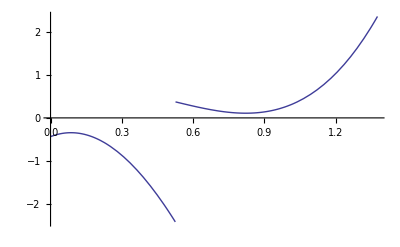

Piecewise[{{-0.438257+2.16913 u-12.9958 u^2+3.14735 u^3, 0.≤u<0.525731}, {0.339123+2.88201 u-8.03188 u^2+5.09251 u^3, 0.525731≤u<1.37638}, {0., True}}]

```mathematica
l=5; k =2;
λ/.λSol[n][[l]]/.σSol//N
1/σ^3/.σSol//N
f[norm_,u_]:=Poly[norm,n,u]/.Flatten[Table[{vector[n][[i]]->  ρ[n][[l,k,i]]},{i,Length[vector[n]]}]]/.A2Sol/.αβSol/.ϕSol/.σSol
f[1,u]//N
Integrate[f[1,u]//N,{u,0,A2/.A2Sol}]//N//Chop
halfnorm=2*Integrate[f[1,u]//N,{u,α/.αSol,A2/.A2Sol}]//N//Chop
Plot[f[halfnorm,u]//N,{u,0,A2/.A2Sol},PlotRange->Full,ImageSize->Scaled[0.5]]
f[halfnorm,u]//N
```

```mathematica
Flatten[Table[{vector[n][[i]]->  ρ[n][[l,k,i]]},{i,Length[vector[n]]}]]
```

{a[0]→-0.0861644,b[0]→0.0735932,a[1]→0.224206,b[1]→-0.224206,a[2]→-0.706205,b[2]→0,a[3]→0.0899154,b[3]→0.61629}

```mathematica
ψ[4,2,u_]:=Poly[0.1966069071915958,3,u]/.{a[0]->-0.08616444410775408,b[0]->0.07359322113324379,a[1]->0.2242059435859426,b[1]->-0.22420594358594292,a[2]->-0.7062050005516631,b[2]->0,a[3]->0.0899154357285325,b[3]->0.6162895648231305}/.A2Sol/.αβSol/.ϕSol/.σSol//N
𝕍[4]:={1/σ^3/.σSol//N,2}
ψ[4,2,u]
```

Piecewise[{{-0.438257+2.16913 u-12.9958 u^2+3.14735 u^3, 0.≤u<0.525731}, {0.339123+2.88201 u-8.03188 u^2+5.09251 u^3, 0.525731≤u<1.37638}, {0., True}}]

```mathematica
l=5; k =1;
λ/.λSol[n][[l]]/.σSol//N
1/σ^3/.σSol//N
f[norm_,u_]:=Poly[norm,n,u]/.Flatten[Table[{vector[n][[i]]->  ρ[n][[l,k,i]]},{i,Length[vector[n]]}]]/.A2Sol/.αβSol/.ϕSol/.σSol
f[1,u]//N
Integrate[f[1,u]//N,{u,0,A2/.A2Sol}]//N//Chop
halfnorm=2*Integrate[f[1,u]//N,{u,α/.αSol,A2/.A2Sol}]//N//Chop
f[halfnorm,u]//N
```

0.0557281

0.0557281

Piecewise[{{0.453515-0.990265 u-0.867516 u^2+0.210096 u^3, 0.≤u<0.525731}, {-0.758502+0.893891 u-0.536154 u^2+0.339942 u^3, 0.525731≤u<1.37638}, {0., True}}]

0

-0.127138

Piecewise[{{-3.5671+7.78888 u+6.8234 u^2-1.6525 u^3, 0.≤u<0.525731}, {5.96595-7.03085 u+4.21709 u^2-2.6738 u^3, 0.525731≤u<1.37638}, {0., True}}]

```mathematica
Flatten[Table[{vector[n][[i]]->  ρ[n][[l,k,i]]},{i,Length[vector[n]]}]]
```

{a[0]→0.453515,b[0]→-0.387348,a[1]→-0.520613,b[1]→0.520613,a[2]→-0.239776,b[2]→0,a[3]→0.0305287,b[3]→0.209247}

```mathematica
ψ[4,3,u_]:=Poly[-0.1271383647294003,3,u]/.{a[0]->0.4535154235212474,b[0]->-0.3873484149540557,a[1]->-0.5206133040994513,b[1]->0.5206133040994518,a[2]->-0.2397755293045013,b[2]->0,a[3]->0.030528700841274257,b[3]->0.2092468284632272}/.A2Sol/.αβSol/.ϕSol/.σSol//N
ψ[4,3,u]
```

Piecewise[{{-3.5671+7.78888 u+6.8234 u^2-1.6525 u^3, 0.≤u<0.525731}, {5.96595-7.03085 u+4.21709 u^2-2.6738 u^3, 0.525731≤u<1.37638}, {0., True}}]

```mathematica
l=2; k=1;
λ/.λSol[n][[l]]/.σSol//N
1/σ^3/.σSol//N
f[norm_,u_]:=Poly[norm,n,u]/.Flatten[Table[{vector[n][[i]]->  ρ[n][[l,k,i]]},{i,Length[vector[n]]}]]/.A2Sol/.αβSol/.ϕSol/.σSol
f[1,u]//N
Integrate[f[1,u]//N,{u,0,A2/.A2Sol}]//N//Chop
halfnorm=2*Integrate[f[1,u]//N,{u,α/.αSol,A2/.A2Sol}]//N//Chop
f[halfnorm,u]//N
```

0.0557281

0.0557281

Piecewise[{{0.458907-1.07164 u-0.0834514 u^2+0.0202103 u^3, 0.≤u<0.525731}, {-0.744903+0.689427 u-0.0515758 u^2+0.032701 u^3, 0.525731≤u<1.37638}, {0., True}}]

0

-0.179016

Piecewise[{{-2.56349+5.98628 u+0.466166 u^2-0.112896 u^3, 0.≤u<0.525731}, {4.16109-3.85119 u+0.288106 u^2-0.18267 u^3, 0.525731≤u<1.37638}, {0., True}}]

```mathematica
Flatten[Table[{vector[n][[i]]->  ρ[n][[l,k,i]]},{i,Length[vector[n]]}]]
```

{a[0]→0.458907,b[0]→-0.391954,a[1]→-0.563396,b[1]→0.563396,a[2]→-0.0230654,b[2]→0,a[3]→0.00293673,b[3]→0.0201287}

```mathematica
ψ[4,4,u_]:=Poly[-0.1790164887043138,3,u]/.{a[0]->0.4589072237933357,b[0]->-0.3919535621680719,a[1]->-0.5633962929816194,b[1]->0.5633962929816196,a[2]->-0.023065385955911843,b[2]->0,a[3]->0.0029367311571746957,b[3]->0.02012865479873717}/.A2Sol/.αβSol/.ϕSol/.σSol//N
ψ[4,4,u]
```

Piecewise[{{-2.56349+5.98628 u+0.466166 u^2-0.112896 u^3, 0.≤u<0.525731}, {4.16109-3.85119 u+0.288106 u^2-0.18267 u^3, 0.525731≤u<1.37638}, {0., True}}]

```mathematica
l=2; k=2;
λ/.λSol[n][[l]]/.σSol//N
1/σ^3/.σSol//N
f[norm_,u_]:=Poly[norm,n,u]/.Flatten[Table[{vector[n][[i]]->  ρ[n][[l,k,i]]},{i,Length[vector[n]]}]]/.A2Sol/.αβSol/.ϕSol/.σSol
f[1,u]//N
Integrate[f[1,u]//N,{u,0,A2/.A2Sol}]//N//Chop
halfnorm=2*Integrate[f[1,u]//N,{u,α/.αSol,A2/.A2Sol}]//N//Chop
f[halfnorm,u]//N
```

0.0557281

0.0557281

Piecewise[{{0.0500471+0.118652 u-2.69704 u^2+0.653171 u^3, 0.≤u<0.525731}, {-0.157763+0.80299 u-1.66686 u^2+1.05685 u^3, 0.525731≤u<1.37638}, {0., True}}]

0

0.150902

Piecewise[{{0.331652+0.786282 u-17.8727 u^2+4.32844 u^3, 0.≤u<0.525731}, {-1.04546+5.32126 u-11.046 u^2+7.00356 u^3, 0.525731≤u<1.37638}, {0., True}}]

```mathematica
Flatten[Table[{vector[n][[i]]->  ρ[n][[l,k,i]]},{i,Length[vector[n]]}]]
```

{a[0]→0.0500471,b[0]→-0.0427453,a[1]→0.062379,b[1]→-0.062379,a[2]→-0.745443,b[2]→0,a[3]→0.0949113,b[3]→0.650532}

```mathematica
ψ[4,5,u_]:=Poly[0.15090240724882184,3,u]/.{a[0]->0.050047085333193825,b[0]->-0.042745313988146585,a[1]->0.062378959587188344,b[1]->-0.062378959587188046,a[2]->-0.7454433548084872,b[2]->0,a[3]->0.09491134161636496,b[3]->0.6505320131921226}/.A2Sol/.αβSol/.ϕSol/.σSol//N
ψ[4,5,u]
```

Piecewise[{{0.331652+0.786282 u-17.8727 u^2+4.32844 u^3, 0.≤u<0.525731}, {-1.04546+5.32126 u-11.046 u^2+7.00356 u^3, 0.525731≤u<1.37638}, {0., True}}]

```mathematica
V4 = Table[
	Riffle[
	CoefficientList[ψ[4,i,u][[1,1,1]],u],
	CoefficientList[ψ[4,i,u][[1,2,1]],u]
	],
{i,5}]
```

{{-2.4899,4.02874,5.8541,-3.61803},{-0.438257,0.339123,2.16913,2.88201,-12.9958,-8.03188,3.14735,5.09251},{-3.5671,5.96595,7.78888,-7.03085,6.8234,4.21709,-1.6525,-2.6738},{-2.56349,4.16109,5.98628,-3.85119,0.466166,0.288106,-0.112896,-0.18267},{0.331652,-1.04546,0.786282,5.32126,-17.8727,-11.046,4.32844,7.00356}}

```mathematica
V4 [[1]]=Join[V4[[1]],{0,0,0,0}];
V4
```

{{-2.4899,4.02874,5.8541,-3.61803,0,0,0,0},{-0.438257,0.339123,2.16913,2.88201,-12.9958,-8.03188,3.14735,5.09251},{-3.5671,5.96595,7.78888,-7.03085,6.8234,4.21709,-1.6525,-2.6738},{-2.56349,4.16109,5.98628,-3.85119,0.466166,0.288106,-0.112896,-0.18267},{0.331652,-1.04546,0.786282,5.32126,-17.8727,-11.046,4.32844,7.00356}}

```mathematica
Dimensions[V4]
MatrixRank[V4]
```

{5,8}

2

```mathematica
Do[
sol=Solve[{x V4[[1,1]]+y V4[[2,1]]==V4[[i,1]],x V4[[1,2]]+y V4[[2,2]]==V4[[i,2]]},{x,y}];
Print[sol];
Print[Chop[V4[[i]]-((x V4[[1]]+y V4[[2]])/.sol[[1]])]],
{i,3,5}]
```

{{x→1.52504,y→-0.525045}}

{0,0,0,0,0,0,0,0}

{{x→1.03587,y→-0.0358704}}

{0,0,0,0,0,0,0,0}

{{x→-0.375265,y→1.37527}}

{0,0,0,0,0,0,0,0}

```mathematica
l=3;
λ/.λSol[n][[l]]/.σSol//N
1/σ^4/.σSol//N
f[norm_,u_]:=Poly[norm,n,u]/.Flatten[Table[{vector[n][[i]]->  ρ[n][[l,1,i]]},{i,Length[vector[n]]}]]/.A2Sol/.αβSol/.ϕSol/.σSol
f[1,u]//N
Integrate[f[1,u]//N,{u,0,A2/.A2Sol}]//N//Chop
halfnorm=2*Integrate[f[1,u]//N,{u,α/.αSol,A2/.A2Sol}]//N//Chop
f[halfnorm,u]//N
ψ[5,1,u]
```

0.0212862

0.0212862

Piecewise[{{-0.245104+0.864413 u-1.01618 u^2, 0.≤u<0.525731}, {0.793175-1.39865 u+0.628033 u^2, 0.525731≤u<1.37638}, {0., True}}]

0

0.11724

Piecewise[{{-2.09062+7.37303 u-8.66752 u^2, 0.≤u<0.525731}, {6.7654-11.9298 u+5.35682 u^2, 0.525731≤u<1.37638}, {0., True}}]

Piecewise[{{-2.09062+7.37303 u-8.66752 u^2, 0.≤u<0.525731}, {6.7654-11.9298 u+5.35682 u^2, 0.525731≤u<1.37638}, {0., True}}]

0.00813062

0.00813062

Piecewise[{{-0.128192+0.602793 u-1.06294 u^2+0.83304 u^3, 0.≤u<0.525731}, {0.750447-1.95068 u+1.71987 u^2-0.514847 u^3, 0.525731≤u<1.37638}, {0., True}}]

0

0.0393308

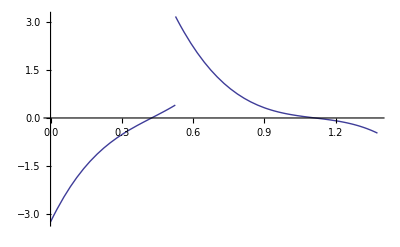

Piecewise[{{-3.25932+15.3262 u-27.0256 u^2+21.1803 u^3, 0.≤u<0.525731}, {19.0804-49.5967 u+43.7284 u^2-13.0902 u^3, 0.525731≤u<1.37638}, {0., True}}]

{a[0]→-0.128192,b[0]→0.125463,a[1]→0.316907,b[1]→-0.484191,a[2]→-0.293789,b[2]→0.656932,a[3]→0.121048,b[3]→-0.316907}

```mathematica
l=1;
λ/.λSol[n][[l]]/.σSol//N
1/σ^5/.σSol//N
f[norm_,u_]:=Poly[norm,n,u]/.Flatten[Table[{vector[n][[i]]->  ρ[n][[l,1,i]]},{i,Length[vector[n]]}]]/.A2Sol/.αβSol/.ϕSol/.σSol
f[1,u]//N
Integrate[f[1,u]//N,{u,0,A2/.A2Sol}]//N//Chop
halfnorm=2*Integrate[f[1,u]//N,{u,α/.αSol,A2/.A2Sol}]//N//Chop
Plot[f[halfnorm,u]//N,{u,0,A2/.A2Sol},PlotRange->Full,ImageSize->Scaled[0.5]]
f[halfnorm,u]//N
Flatten[Table[{vector[n][[i]]->  ρ[n][[l,1,i]]},{i,Length[vector[n]]}]]
```

```mathematica
Flatten[Table[{vector[n][[i]]->  ρ[n][[l,1,i]]},{i,Length[vector[n]]}]]
```

{a[0]→-0.128192,b[0]→0.125463,a[1]→0.316907,b[1]→-0.484191,a[2]→-0.293789,b[2]→0.656932,a[3]→0.121048,b[3]→-0.316907}

```mathematica
ψ[6,1,u_]:=Poly[0.03933080132577827,3,u]/.{a[0]->-0.12819163470018616,b[0]->0.12546291727840125,a[1]->0.3169071492725016,b[1]->-0.48419103897703636,a[2]->-0.2937890842923636,b[2]->0.6569323635251412,a[3]->0.12104775974425928,b[3]->-0.31690714927250224}/.A2Sol/.αβSol/.ϕSol/.σSol//N
ψ[6,1,u]
𝕍[6]:={1/σ^5/.σSol//N,1}
```

Piecewise[{{-3.25932+15.3262 u-27.0256 u^2+21.1803 u^3, 0.≤u<0.525731}, {19.0804-49.5967 u+43.7284 u^2-13.0902 u^3, 0.525731≤u<1.37638}, {0., True}}]

#### order 4

```mathematica
n=4;
Subscript[LPoly, A][n]=Collect[(Subscript[Poly, A][n,u/σ]+Subscript[Poly, B][n,u/σ+α])/σ,u,Simplify]
Subscript[LPoly, B][n]=Collect[(Subscript[Poly, A][n,u/σ]+Subscript[Poly, B][n,u/σ+α]+Subscript[Poly, B][n,u/σ+β])/σ,u,Simplify]
```

(a[0]+b[0])/σ+(u (β a[1]+α b[1]))/(α β σ^2)+(u^2 (a[2]/α^2+b[2]/β^2))/σ^3+(u^3 (a[3]/α^3+b[3]/β^3))/σ^4+(u^4 (a[4]/α^4+b[4]/β^4))/σ^5

(u^4 (a[4]/α^4+(2 b[4])/β^4))/σ^5+(u^3 (β^4 a[3]-4 α^4 b[4]+2 α^3 β (b[3]+2 b[4])))/(α^3 β^4 σ^4)+(u (β^4 a[1]-4 α^4 b[4]+3 α^3 β (b[3]+4 b[4])+α β^3 (2 b[1]+2 b[2]+3 b[3]+4 b[4])-2 α^2 β^2 (b[2]+3 b[3]+6 b[4])))/(α β^4 σ^2)+1/(β^4 σ)(α^4 b[4]+β^4 (a[0]+2 b[0]+b[1]+b[2]+b[3]+b[4])-α^3 β (b[3]+4 b[4])-α β^3 (b[1]+2 b[2]+3 b[3]+4 b[4])+α^2 β^2 (b[2]+3 b[3]+6 b[4]))+(u^2 (β^4 a[2]+6 α^4 b[4]-3 α^3 β (b[3]+4 b[4])+α^2 β^2 (2 b[2]+3 b[3]+6 b[4])))/(α^2 β^4 σ^3)

```mathematica
vector[n]=Table[{a[i],b[i]},{i,0,n}]//Flatten;
```

```mathematica
Subscript[lhs, A][n,i_]:=Coefficient[Subscript[LPoly, A][n],u,i]
Subscript[lhs, B][n,i_]:=Coefficient[Subscript[LPoly, B][n],u,i]
L[n]={};
Do[
L[n]=Append[L[n],Coefficient[Subscript[lhs, A][n,i],#]&/@vector[n]];
L[n]=Append[L[n],Coefficient[Subscript[lhs, B][n,i],#]&/@vector[n]],
{i,0,n}]
L[n]//Simplify//TraditionalForm
Subscript[rhs, A][n,i_]:=Coefficient[Subscript[Poly, A][n,u],u,i]
Subscript[rhs, B][n,i_]:=Coefficient[Subscript[Poly, B][n,u],u,i]
J[n]={};
Do[
J[n]=Append[J[n],Coefficient[Subscript[rhs, A][n,i],#]&/@vector[n]];
J[n]=Append[J[n],Coefficient[Subscript[rhs, B][n,i],#]&/@vector[n]],
{i,0,n}]
J[n]//TraditionalForm
```

(1/σ | 1/σ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/σ | 2/σ | 0 | (β-α)/(β σ) | 0 | (α-β)^2/(β^2 σ) | 0 | -(α-β)^3/(β^3 σ) | 0 | (α-β)^4/(β^4 σ)
0 | 0 | 1/(α σ^2) | 1/(β σ^2) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/(α σ^2) | 2/(β σ^2) | 0 | -(2 (α-β))/(β^2 σ^2) | 0 | (3 (α-β)^2)/(β^3 σ^2) | 0 | -(4 (α-β)^3)/(β^4 σ^2)
0 | 0 | 0 | 0 | 1/(α^2 σ^3) | 1/(β^2 σ^3) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/(α^2 σ^3) | 2/(β^2 σ^3) | 0 | -(3 (α-β))/(β^3 σ^3) | 0 | (6 (α-β)^2)/(β^4 σ^3)
0 | 0 | 0 | 0 | 0 | 0 | 1/(α^3 σ^4) | 1/(β^3 σ^4) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/(α^3 σ^4) | 2/(β^3 σ^4) | 0 | -(4 (α-β))/(β^4 σ^4)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(α^4 σ^5) | 1/(β^4 σ^5)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(α^4 σ^5) | 2/(β^4 σ^5))

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | -α/β | 0 | α^2/β^2 | 0 | -α^3/β^3 | 0 | α^4/β^4
0 | 0 | 1/α | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/β | 0 | -(2 α)/β^2 | 0 | (3 α^2)/β^3 | 0 | -(4 α^3)/β^4
0 | 0 | 0 | 0 | 1/α^2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/β^2 | 0 | -(3 α)/β^3 | 0 | (6 α^2)/β^4
0 | 0 | 0 | 0 | 0 | 0 | 1/α^3 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/β^3 | 0 | -(4 α)/β^4
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/α^4 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/β^4)

```mathematica
determinant[n]=Det[L[n]-λ J[n]]//Simplify
```

((1-3 λ σ+λ^2 σ^2) (1-3 λ σ^2+λ^2 σ^4) (1-3 λ σ^3+λ^2 σ^6) (1-3 λ σ^4+λ^2 σ^8) (1-3 λ σ^5+λ^2 σ^10))/(α^10 β^10 σ^30)

```mathematica
λSol[n]=Solve[determinant[n]==0,λ]
```

{{λ→(3-√5)/(2 σ^5)},{λ→(3+√5)/(2 σ^5)},{λ→(3-√5)/(2 σ^4)},{λ→(3+√5)/(2 σ^4)},{λ→(3-√5)/(2 σ^3)},{λ→(3+√5)/(2 σ^3)},{λ→(3-√5)/(2 σ^2)},{λ→(3+√5)/(2 σ^2)},{λ→(3-√5)/(2 σ)},{λ→(3+√5)/(2 σ)}}

```mathematica
λSol[n]/.σSol//Simplify
%//N
```

{{λ→161-72 √5},{λ→16/(3+√5)^4},{λ→1/2 (123-55 √5)},{λ→9-4 √5},{λ→1/2 (47-21 √5)},{λ→4/(3+√5)^2},{λ→9-4 √5},{λ→2/(3+√5)},{λ→1/2 (7-3 √5)},{λ→1}}

{{λ→0.00310562},{λ→0.0212862},{λ→0.00813062},{λ→0.0557281},{λ→0.0212862},{λ→0.145898},{λ→0.0557281},{λ→0.381966},{λ→0.145898},{λ→1.}}

```mathematica
LN[n]=(L[n]/.αβSol/.σSol)//N//Chop
JN[n]=(J[n]/.αβSol/.σSol)//N//Chop
```

{{0.381966,0.381966,0,0,0,0,0,0,0,0},{0.381966,0.763932,0,0.145898,0,0.0557281,0,0.0212862,0,0.00813062},{0,0,0.277515,0.171513,0,0,0,0,0,0},{0,0,0.277515,0.343027,0,0.131025,0,0.0750704,0,0.0382325},{0,0,0,0,0.201626,0.0770143,0,0,0,0},{0,0,0,0,0.201626,0.154029,0,0.0882506,0,0.0674174},{0,0,0,0,0,0,0.14649,0.0345816,0,0},{0,0,0,0,0,0,0.14649,0.0691632,0,0.052836},{0,0,0,0,0,0,0,0,0.106431,0.0155281},{0,0,0,0,0,0,0,0,0.106431,0.0310562}}

{{1.,0,0,0,0,0,0,0,0,0},{0,1.,0,-0.618034,0,0.381966,0,-0.236068,0,0.145898},{0,0,1.90211,0,0,0,0,0,0,0},{0,0,0,1.17557,0,-1.45309,0,1.34708,0,-1.11006},{0,0,0,0,3.61803,0,0,0,0,0},{0,0,0,0,0,1.38197,0,-2.56231,0,3.16718},{0,0,0,0,0,0,6.88191,0,0,0},{0,0,0,0,0,0,0,1.6246,0,-4.01623},{0,0,0,0,0,0,0,0,13.0902,0},{0,0,0,0,0,0,0,0,0,1.90983}}

```mathematica
ρ[n]=Table[
NullSpace[(LN[n]-λ JN[n])/.λSol[n][[i]]/.σSol//N],
{i,Length[λSol[n]]}]//Chop
Length/@%
λSol[n]/.σSol//Simplify;
%//N
```

{{{0.0662502,-0.0657115,-0.204724,0.3242,0.253053,-0.625582,-0.156395,0.565844,0.0483289,-0.204724}},{{0.148419,-0.140148,-0.225308,0.311368,-0.0148788,0.0240744,0.616508,0,-0.0588712,-0.652892},{-0.206076,0.194591,0.40082,-0.553919,-0.305614,0.494494,0.231575,0,-0.0221135,-0.245242}},{{-0.128192,0.125463,0.316907,-0.484191,-0.293789,0.656932,0.121048,-0.316907,0,0}},{{-0.441133,0.376772,0.492477,-0.492477,0.316761,0,-0.0403306,-0.27643,0,0},{0.136023,-0.116178,-0.280665,0.280665,0.675189,0,-0.0859665,-0.589223,0,0}},{{-0.106536,0.100599,0.238355,-0.329399,-0.273476,0.442493,0.504656,0,-0.0481903,-0.534439},{-0.230533,0.217686,0.393201,-0.54339,-0.137231,0.222045,-0.423121,0,0.0404045,0.448092}},{{0.687696,-0.42502,-0.452626,0,0.0864439,0.366182,0,0,0,0},{0.500681,-0.309438,0.621692,0,-0.118733,-0.50296,0,0,0,0}},{{-0.45855,0.391648,0.535431,-0.535431,0.188204,0,-0.0239625,-0.164242,0,0},{0.0532227,-0.0454576,-0.186064,0.186064,0.721663,0,-0.0918835,-0.629779,0,0}},{{0.682646,0,-0.260748,-0.682646,0,0,0,0,0,0}},{{0.828956,-0.512323,0.172568,0,-0.0329576,-0.13961,0,0,0,0},{-0.190889,0.117976,0.749395,0,-0.143122,-0.606273,0,0,0,0}},{{0.525731,0.850651,0,0,0,0,0,0,0,0}}}

{1,2,1,2,2,2,2,1,2,1}

{{λ→0.00310562},{λ→0.0212862},{λ→0.00813062},{λ→0.0557281},{λ→0.0212862},{λ→0.145898},{λ→0.0557281},{λ→0.381966},{λ→0.145898},{λ→1.}}

```mathematica
l=10; k = 1;
λ/.λSol[n][[l]]/.σSol
f[norm_,u_]:=Poly[norm,n,u]/.Flatten[Table[{vector[n][[i]]->  ρ[n][[l,k,i]]},{i,Length[vector[n]]}]]/.A2Sol/.αβSol/.ϕSol/.σSol
f[1,u]//N
norm=Integrate[f[1,u]//N,{u,0,A2/.A2Sol//N}]//N//Chop
f[norm,u]//N
ψ[1,1,u]
```

1

Piecewise[{{0.525731, 0.≤u<0.525731}, {0.850651, 0.525731≤u<1.37638}, {0., True}}]

1.

Piecewise[{{0.525731, 0.≤u<0.525731}, {0.850651, 0.525731≤u<1.37638}, {0., True}}]

Piecewise[{{0.525731, 0.≤u<0.525731}, {0.850651, 0.525731≤u<1.37638}, {0., True}}]

```mathematica
l=8; k =1;
λ/.λSol[n][[l]]/.σSol//N
f[norm_,u_]:=Poly[norm,n,u]/.Flatten[Table[{vector[n][[i]]->  ρ[n][[l,k,i]]},{i,Length[vector[n]]}]]/.A2Sol/.αβSol/.ϕSol/.σSol
f[1,u]//N
Integrate[f[1,u]//N,{u,0,A2/.A2Sol}]//N//Chop
halfnorm=2*Integrate[f[1,u]//N,{u,α/.αSol,A2/.A2Sol}]//N//Chop
f[halfnorm,u]//N
ψ[2,1,u]
```

0.381966

Piecewise[{{0.682646-0.495971 u, 0.≤u<0.525731}, {0.421898-0.802498 u, 0.525731≤u<1.37638}, {0., True}}]

0

-0.580693

Piecewise[{{-1.17557+0.854102 u, 0.≤u<0.525731}, {-0.726543+1.38197 u, 0.525731≤u<1.37638}, {0., True}}]

Piecewise[{{-1.17557+0.854102 u, 0.≤u<0.525731}, {-0.726543+1.38197 u, 0.525731≤u<1.37638}, {0., True}}]

```mathematica
l=6; k=1;
λ/.λSol[n][[l]]/.σSol//N
1/σ^2/.σSol//N
f[norm_,u_]:=Poly[norm,n,u]/.Flatten[Table[{vector[n][[i]]->  ρ[n][[l,k,i]]},{i,Length[vector[n]]}]]/.A2Sol/.αβSol/.ϕSol/.σSol
f[1,u]//N
Integrate[f[1,u]//N,{u,0,A2/.A2Sol}]//N//Chop
halfnorm=2*Integrate[f[1,u]//N,{u,α/.αSol,A2/.A2Sol}]//N//Chop
f[halfnorm,u]//N
```

0.145898

0.145898

Piecewise[{{0.687696-0.860946 u+0.312757 u^2, 0.≤u<0.525731}, {-0.28515-0.532094 u+0.506052 u^2, 0.525731≤u<1.37638}, {0., True}}]

0

-0.515424

Piecewise[{{-1.33423+1.67036 u-0.606795 u^2, 0.≤u<0.525731}, {0.553234+1.03234 u-0.981816 u^2, 0.525731≤u<1.37638}, {0., True}}]

```mathematica
Flatten[Table[{vector[n][[i]]->  ρ[n][[l,k,i]]},{i,Length[vector[n]]}]]
```

{a[0]→0.687696,b[0]→-0.42502,a[1]→-0.452626,b[1]→0,a[2]→0.0864439,b[2]→0.366182,a[3]→0,b[3]→0,a[4]→0,b[4]→0}

```mathematica
ψ[3,3,u_]:=Poly[-0.5154241904182523,4,u]/.{a[0]->0.6876960242674923,b[0]->-0.4250195169254827,a[1]->-0.4526262611472773,b[1]->0,a[2]->0.08644392377873689,b[2]->0.36618233736854006,a[3]->0,b[3]->0,a[4]->0,b[4]->0}/.A2Sol/.αβSol/.ϕSol/.σSol//N
ψ[3,3,u]
```

Piecewise[{{-1.33423+1.67036 u-0.606795 u^2, 0.≤u<0.525731}, {0.553234+1.03234 u-0.981816 u^2, 0.525731≤u<1.37638}, {0., True}}]

```mathematica
l=6; k=2;
λ/.λSol[n][[l]]/.σSol//N
1/σ^2/.σSol//N
f[norm_,u_]:=Poly[norm,n,u]/.Flatten[Table[{vector[n][[i]]->  ρ[n][[l,k,i]]},{i,Length[vector[n]]}]]/.A2Sol/.αβSol/.ϕSol/.σSol
f[1,u]//N
Integrate[f[1,u]//N,{u,0,A2/.A2Sol}]//N//Chop
halfnorm=2*Integrate[f[1,u]//N,{u,α/.αSol,A2/.A2Sol}]//N//Chop
f[halfnorm,u]//N
Flatten[Table[{vector[n][[i]]->  ρ[n][[l,k,i]]},{i,Length[vector[n]]}]]
```

0.145898

0.145898

Piecewise[{{0.500681+1.18253 u-0.429579 u^2, 0.≤u<0.525731}, {-0.501551+0.730843 u-0.695073 u^2, 0.525731≤u<1.37638}, {0., True}}]

0

-0.811675

Piecewise[{{-0.616848-1.4569 u+0.52925 u^2, 0.≤u<0.525731}, {0.617921-0.900413 u+0.856344 u^2, 0.525731≤u<1.37638}, {0., True}}]

{a[0]→0.500681,b[0]→-0.309438,a[1]→0.621692,b[1]→0,a[2]→-0.118733,b[2]→-0.50296,a[3]→0,b[3]→0,a[4]→0,b[4]→0}

```mathematica
ψ[3,4,u_]:=Poly[-0.8116753818791368,4,u]/.{a[0]->0.5006805128589129,b[0]->-0.3094375744515368,a[1]->0.6216924211662999,b[1]->0,a[2]->-0.11873268716865575,b[2]->-0.5029597339976432,a[3]->0,b[3]->0,a[4]->0,b[4]->0}/.A2Sol/.αβSol/.ϕSol/.σSol//N
ψ[3,4,u]
```

Piecewise[{{-0.616848-1.4569 u+0.52925 u^2, 0.≤u<0.525731}, {0.617921-0.900413 u+0.856344 u^2, 0.525731≤u<1.37638}, {0., True}}]

```mathematica
l=9; k = 1;
λ/.λSol[n][[l]]/.σSol//N
1/σ^2/.σSol//N
f[norm_,u_]:=Poly[norm,n,u]/.Flatten[Table[{vector[n][[i]]->  ρ[n][[l,k,i]]},{i,Length[vector[n]]}]]/.A2Sol/.αβSol/.ϕSol/.σSol
f[1,u]//N
Integrate[f[1,u]//N,{u,0,A2/.A2Sol}]//N//Chop
halfnorm=2*Integrate[f[1,u]//N,{u,α/.αSol,A2/.A2Sol}]//N//Chop
f[halfnorm,u]//N
Flatten[Table[{vector[n][[i]]->  ρ[n][[l,k,i]]},{i,Length[vector[n]]}]]
```

0.145898

0.145898

Piecewise[{{0.828956+0.328244 u-0.119242 u^2, 0.≤u<0.525731}, {-0.565649+0.202866 u-0.192937 u^2, 0.525731≤u<1.37638}, {0., True}}]

0

-0.950789

Piecewise[{{-0.871861-0.345233 u+0.125413 u^2, 0.≤u<0.525731}, {0.594926-0.213366 u+0.202923 u^2, 0.525731≤u<1.37638}, {0., True}}]

{a[0]→0.828956,b[0]→-0.512323,a[1]→0.172568,b[1]→0,a[2]→-0.0329576,b[2]→-0.13961,a[3]→0,b[3]→0,a[4]→0,b[4]→0}

```mathematica
ψ[3,5,u_]:=Poly[-0.9507891282056042,4,u]/.{a[0]->0.8289560584394389,b[0]->-0.5123230192957171,a[1]->0.17256797555721037,b[1]->0,a[2]->-0.032957550646546784,b[2]->-0.13961042491066367,a[3]->0,b[3]->0,a[4]->0,b[4]->0}/.A2Sol/.αβSol/.ϕSol/.σSol//N
ψ[3,5,u]
```

Piecewise[{{-0.871861-0.345233 u+0.125413 u^2, 0.≤u<0.525731}, {0.594926-0.213366 u+0.202923 u^2, 0.525731≤u<1.37638}, {0., True}}]

```mathematica
l=9; k = 2;
λ/.λSol[n][[l]]/.σSol//N
1/σ^2/.σSol//N
f[norm_,u_]:=Poly[norm,n,u]/.Flatten[Table[{vector[n][[i]]->  ρ[n][[l,k,i]]},{i,Length[vector[n]]}]]/.A2Sol/.αβSol/.ϕSol/.σSol
f[1,u]//N
Integrate[f[1,u]//N,{u,0,A2/.A2Sol}]//N//Chop
halfnorm=2*Integrate[f[1,u]//N,{u,α/.αSol,A2/.A2Sol}]//N//Chop
f[halfnorm,u]//N
Flatten[Table[{vector[n][[i]]->  ρ[n][[l,k,i]]},{i,Length[vector[n]]}]]
```

0.145898

0.145898

Piecewise[{{-0.190889+1.42543 u-0.517819 u^2, 0.≤u<0.525731}, {-0.1136+0.880966 u-0.837849 u^2, 0.525731≤u<1.37638}, {0., True}}]

0

-0.143105

Piecewise[{{1.33391-9.96075 u+3.61845 u^2, 0.≤u<0.525731}, {0.79382-6.15608 u+5.85478 u^2, 0.525731≤u<1.37638}, {0., True}}]

{a[0]→-0.190889,b[0]→0.117976,a[1]→0.749395,b[1]→0,a[2]→-0.143122,b[2]→-0.606273,a[3]→0,b[3]→0,a[4]→0,b[4]→0}

```mathematica
ψ[3,6,u_]:=Poly[-0.14310504988636752,4,u]/.{a[0]->-0.1908891063589764,b[0]->0.11797595581194108,a[1]->0.7493946174265359,b[1]->0,a[2]->-0.14312163643535586,b[2]->-0.6062729809911795,a[3]->0,b[3]->0,a[4]->0,b[4]->0}/.A2Sol/.αβSol/.ϕSol/.σSol//N
ψ[3,6,u]
```

Piecewise[{{1.33391-9.96075 u+3.61845 u^2, 0.≤u<0.525731}, {0.79382-6.15608 u+5.85478 u^2, 0.525731≤u<1.37638}, {0., True}}]

```mathematica
V3 = Table[
	Riffle[
	CoefficientList[ψ[3,i,u][[1,1,1]],u],
	CoefficientList[ψ[3,i,u][[1,2,1]],u]
	],
{i,6}]
```

{{-0.951057,0.587785},{0.,0.673542,-4.1459,-2.56231,1.50609,2.4369},{-1.33423,0.553234,1.67036,1.03234,-0.606795,-0.981816},{-0.616848,0.617921,-1.4569,-0.900413,0.52925,0.856344},{-0.871861,0.594926,-0.345233,-0.213366,0.125413,0.202923},{1.33391,0.79382,-9.96075,-6.15608,3.61845,5.85478}}

```mathematica
V3 [[1]]={V3[[1,1]],V3[[1,2]],0,0,0,0};
V3
```

{{-0.951057,0.587785,0,0,0,0},{0.,0.673542,-4.1459,-2.56231,1.50609,2.4369},{-1.33423,0.553234,1.67036,1.03234,-0.606795,-0.981816},{-0.616848,0.617921,-1.4569,-0.900413,0.52925,0.856344},{-0.871861,0.594926,-0.345233,-0.213366,0.125413,0.202923},{1.33391,0.79382,-9.96075,-6.15608,3.61845,5.85478}}

```mathematica
Dimensions[V3]
Det[V3]//Chop
MatrixRank[V3]

Do[
sol=Solve[{x V3[[1,1]]+y V3[[2,1]]==V3[[i,1]],x V3[[1,2]]+y V3[[2,2]]==V3[[i,2]]},{x,y}];
Print[sol];
Print[Chop[V3[[i]]-((x V3[[1]]+y V3[[2]])/.sol[[1]])]],
{i,3,6}]
```

{6,6}

0

2

{{x→1.4029,y→-0.402896}}

{0,0,0,0,0,0}

{{x→0.648593,y→0.351407}}

{0,0,0,0,0,0}

{{x→0.916729,y→0.083271}}

{0,0,0,0,0,0}

{{x→-1.40255,y→2.40255}}

{0,0,0,0,0,0}

```mathematica
l=4; k =1;
λ/.λSol[n][[l]]/.σSol//N
1/σ^3/.σSol//N
f[norm_,u_]:=Poly[norm,n,u]/.Flatten[Table[{vector[n][[i]]->  ρ[n][[l,k,i]]},{i,Length[vector[n]]}]]/.A2Sol/.αβSol/.ϕSol/.σSol
f[1,u]//N
Integrate[f[1,u]//N,{u,0,A2/.A2Sol}]//N//Chop
halfnorm=2*Integrate[f[1,u]//N,{u,α/.αSol,A2/.A2Sol}]//N//Chop
f[halfnorm,u]//N
Flatten[Table[{vector[n][[i]]->  ρ[n][[l,k,i]]},{i,Length[vector[n]]}]]
```

0.0557281

0.0557281

Piecewise[{{-0.441133+0.936747 u+1.14605 u^2-0.277551 u^3, 0.≤u<0.525731}, {0.746396-0.951316 u+0.708298 u^2-0.449088 u^3, 0.525731≤u<1.37638}, {0., True}}]

0

0.104505

Piecewise[{{-4.22116+8.96364 u+10.9665 u^2-2.65586 u^3, 0.≤u<0.525731}, {7.1422-9.10305 u+6.77764 u^2-4.29728 u^3, 0.525731≤u<1.37638}, {0., True}}]

{a[0]→-0.441133,b[0]→0.376772,a[1]→0.492477,b[1]→-0.492477,a[2]→0.316761,b[2]→0,a[3]→-0.0403306,b[3]→-0.27643,a[4]→0,b[4]→0}

```mathematica
ψ[4,3,u_]:=Poly[0.10450513263429227,4,u]/.{a[0]->-0.44113291916319375,b[0]->0.37677249363474685,a[1]->0.4924768473953877,b[1]->-0.49247684739538766,a[2]->0.3167605668194356,b[2]->0,a[3]->-0.04033059007644731,b[3]->-0.2764299767429882,a[4]->0,b[4]->0}/.A2Sol/.αβSol/.ϕSol/.σSol//N
ψ[4,3,u]
```

Piecewise[{{-4.22116+8.96364 u+10.9665 u^2-2.65586 u^3, 0.≤u<0.525731}, {7.1422-9.10305 u+6.77764 u^2-4.29728 u^3, 0.525731≤u<1.37638}, {0., True}}]

```mathematica
l=4; k =2;
λ/.λSol[n][[l]]/.σSol//N
1/σ^3/.σSol//N
f[norm_,u_]:=Poly[norm,n,u]/.Flatten[Table[{vector[n][[i]]->  ρ[n][[l,k,i]]},{i,Length[vector[n]]}]]/.A2Sol/.αβSol/.ϕSol/.σSol
f[1,u]//N
Integrate[f[1,u]//N,{u,0,A2/.A2Sol}]//N//Chop
halfnorm=2*Integrate[f[1,u]//N,{u,α/.αSol,A2/.A2Sol}]//N//Chop
f[halfnorm,u]//N
Flatten[Table[{vector[n][[i]]->  ρ[n][[l,k,i]]},{i,Length[vector[n]]}]]
```

0.0557281

0.0557281

Piecewise[{{0.136023-0.533857 u+2.44286 u^2-0.591613 u^3, 0.≤u<0.525731}, {-0.150542-0.463791 u+1.50977 u^2-0.95725 u^3, 0.525731≤u<1.37638}, {0., True}}]

0

-0.209516

Piecewise[{{-0.649224+2.54805 u-11.6595 u^2+2.82371 u^3, 0.≤u<0.525731}, {0.71852+2.21362 u-7.20597 u^2+4.56886 u^3, 0.525731≤u<1.37638}, {0., True}}]

{a[0]→0.136023,b[0]→-0.116178,a[1]→-0.280665,b[1]→0.280665,a[2]→0.675189,b[2]→0,a[3]→-0.0859665,b[3]→-0.589223,a[4]→0,b[4]→0}

```mathematica
ψ[4,4,u_]:=Poly[-0.2095163883675927,4,u]/.{a[0]->0.1360231540239145,b[0]->-0.11617764330730901,a[1]->-0.28066540991741534,b[1]->0.2806654099174154,a[2]->0.6751892701795975,b[2]->0,a[3]->-0.08596645078979002,b[3]->-0.5892228193898071,a[4]->0,b[4]->0}/.A2Sol/.αβSol/.ϕSol/.σSol//N
ψ[4,4,u]
```

Piecewise[{{-0.649224+2.54805 u-11.6595 u^2+2.82371 u^3, 0.≤u<0.525731}, {0.71852+2.21362 u-7.20597 u^2+4.56886 u^3, 0.525731≤u<1.37638}, {0., True}}]

```mathematica
l=7; k=1;
λ/.λSol[n][[l]]/.σSol//N
1/σ^3/.σSol//N
f[norm_,u_]:=Poly[norm,n,u]/.Flatten[Table[{vector[n][[i]]->  ρ[n][[l,k,i]]},{i,Length[vector[n]]}]]/.A2Sol/.αβSol/.ϕSol/.σSol
f[1,u]//N
Integrate[f[1,u]//N,{u,0,A2/.A2Sol}]//N//Chop
halfnorm=2*Integrate[f[1,u]//N,{u,α/.αSol,A2/.A2Sol}]//N//Chop
f[halfnorm,u]//N
Flatten[Table[{vector[n][[i]]->  ρ[n][[l,k,i]]},{i,Length[vector[n]]}]]/.A2Sol/.αβSol/.ϕSol/.σSol
```

0.0557281

0.0557281

Piecewise[{{-0.45855+1.01845 u+0.680929 u^2-0.164908 u^3, 0.≤u<0.525731}, {0.761335-0.850685 u+0.420837 u^2-0.266827 u^3, 0.525731≤u<1.37638}, {0., True}}]

0

0.140991

Piecewise[{{-3.25234+7.22354 u+4.82961 u^2-1.16964 u^3, 0.≤u<0.525731}, {5.3999-6.03363 u+2.98486 u^2-1.89252 u^3, 0.525731≤u<1.37638}, {0., True}}]

{a[0]→-0.45855,b[0]→0.391648,a[1]→0.535431,b[1]→-0.535431,a[2]→0.188204,b[2]→0,a[3]→-0.0239625,b[3]→-0.164242,a[4]→0,b[4]→0}

```mathematica
ψ[4,5,u_]:=Poly[0.1409905751418893,4,u]/.{a[0]->-0.4585497690975017,b[0]->0.391648259409515,a[1]->0.5354313151838892,b[1]->-0.535431315183889,a[2]->0.18820422292473157,b[2]->0,a[3]->-0.023962538776995092,b[3]->-0.1642416841477365,a[4]->0,b[4]->0}/.A2Sol/.αβSol/.ϕSol/.σSol//N
ψ[4,5,u]
```

Piecewise[{{-3.25234+7.22354 u+4.82961 u^2-1.16964 u^3, 0.≤u<0.525731}, {5.3999-6.03363 u+2.98486 u^2-1.89252 u^3, 0.525731≤u<1.37638}, {0., True}}]

```mathematica
l=7; k=2;
λ/.λSol[n][[l]]/.σSol//N
1/σ^3/.σSol//N
f[norm_,u_]:=Poly[norm,n,u]/.Flatten[Table[{vector[n][[i]]->  ρ[n][[l,k,i]]},{i,Length[vector[n]]}]]/.A2Sol/.αβSol/.ϕSol/.σSol
f[1,u]//N
Integrate[f[1,u]//N,{u,0,A2/.A2Sol}]//N//Chop
halfnorm=2*Integrate[f[1,u]//N,{u,α/.αSol,A2/.A2Sol}]//N//Chop
f[halfnorm,u]//N
Flatten[Table[{vector[n][[i]]->  ρ[n][[l,k,i]]},{i,Length[vector[n]]}]]/.A2Sol/.αβSol/.ϕSol/.σSol
```

0.0557281

0.0557281

Piecewise[{{0.0532227-0.353915 u+2.611 u^2-0.632334 u^3, 0.≤u<0.525731}, {-0.0117809-0.629634 u+1.61369 u^2-1.02314 u^3, 0.525731≤u<1.37638}, {0., True}}]

0

-0.186923

Piecewise[{{-0.284731+1.89338 u-13.9683 u^2+3.38286 u^3, 0.≤u<0.525731}, {0.0630253+3.36842 u-8.63291 u^2+5.47359 u^3, 0.525731≤u<1.37638}, {0., True}}]

{a[0]→0.0532227,b[0]→-0.0454576,a[1]→-0.186064,b[1]→0.186064,a[2]→0.721663,b[2]→0,a[3]→-0.0918835,b[3]→-0.629779,a[4]→0,b[4]→0}

```mathematica
ψ[4,6,u_]:=Poly[-0.18692270451357776,4,u]/.{a[0]->0.053222740071159014,b[0]->-0.04545764694397278,a[1]->-0.1860640327012758,b[1]->0.18606403270127603,a[2]->0.721662648147128,b[2]->0,a[3]->-0.09188353439364874,b[3]->-0.629779113753479,a[4]->0,b[4]->0}/.A2Sol/.αβSol/.ϕSol/.σSol//N
ψ[4,6,u]
```

Piecewise[{{-0.284731+1.89338 u-13.9683 u^2+3.38286 u^3, 0.≤u<0.525731}, {0.0630253+3.36842 u-8.63291 u^2+5.47359 u^3, 0.525731≤u<1.37638}, {0., True}}]

```mathematica
V4 = Table[
	Riffle[
	CoefficientList[ψ[4,i,u][[1,1,1]],u],
	CoefficientList[ψ[4,i,u][[1,2,1]],u]
	],
{i,6}]
```

{{-2.4899,4.02874,5.8541,-3.61803},{-0.438257,0.339123,2.16913,2.88201,-12.9958,-8.03188,3.14735,5.09251},{-4.22116,7.1422,8.96364,-9.10305,10.9665,6.77764,-2.65586,-4.29728},{-0.649224,0.71852,2.54805,2.21362,-11.6595,-7.20597,2.82371,4.56886},{-3.25234,5.3999,7.22354,-6.03363,4.82961,2.98486,-1.16964,-1.89252},{-0.284731,0.0630253,1.89338,3.36842,-13.9683,-8.63291,3.38286,5.47359}}

```mathematica
V4 [[1]]=Join[V4[[1]],{0,0,0,0}];
V4
```

{{-2.4899,4.02874,5.8541,-3.61803,0,0,0,0},{-0.438257,0.339123,2.16913,2.88201,-12.9958,-8.03188,3.14735,5.09251},{-4.22116,7.1422,8.96364,-9.10305,10.9665,6.77764,-2.65586,-4.29728},{-0.649224,0.71852,2.54805,2.21362,-11.6595,-7.20597,2.82371,4.56886},{-3.25234,5.3999,7.22354,-6.03363,4.82961,2.98486,-1.16964,-1.89252},{-0.284731,0.0630253,1.89338,3.36842,-13.9683,-8.63291,3.38286,5.47359}}

```mathematica
Dimensions[V4]
MatrixRank[V4]
```

{6,8}

2

```mathematica
Do[
sol=Solve[{x V4[[1,1]]+y V4[[2,1]]==V4[[i,1]],x V4[[1,2]]+y V4[[2,2]]==V4[[i,2]]},{x,y}];
Print[sol];
Print[Chop[V4[[i]]-((x V4[[1]]+y V4[[2]])/.sol[[1]])]],
{i,3,6}]
```

{{x→1.16956,y→-0.169555}}

{0,0,0,0,0,0,0,0}

{{x→0.250453,y→0.749547}}

{0,0,0,0,0,0,0,0}

{{x→0.352392,y→0.647608}}

{0,0,0,0,0,0,0,0}

{{x→1.34764,y→-0.347641}}

{0,0,0,0,0,0,0,0}

0.0212862

0.0212862

Piecewise[{{0.148419-0.428562 u-0.053832 u^2+4.24275 u^3-0.770634 u^4, 0.≤u<0.525731}, {-0.418644+1.0558 u-2.03456 u^2+2.62216 u^3-1.24691 u^4, 0.525731≤u<1.37638}, {0., True}}]

0

-0.182069

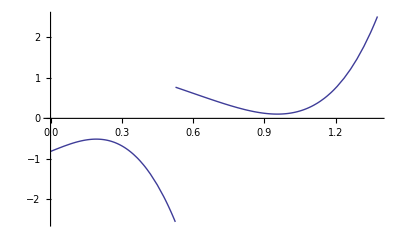

Piecewise[{{-0.81518+2.35384 u+0.295668 u^2-23.3029 u^3+4.23264 u^4, 0.≤u<0.525731}, {2.29937-5.79889 u+11.1746 u^2-14.402 u^3+6.84856 u^4, 0.525731≤u<1.37638}, {0., True}}]

{a[0]→0.148419,b[0]→-0.140148,a[1]→-0.225308,b[1]→0.311368,a[2]→-0.0148788,b[2]→0.0240744,a[3]→0.616508,b[3]→0,a[4]→-0.0588712,b[4]→-0.652892}

```mathematica
l=2;k=1;
λ/.λSol[n][[l]]/.σSol//N
1/σ^4/.σSol//N
f[norm_,u_]:=Poly[norm,n,u]/.Flatten[Table[{vector[n][[i]]->  ρ[n][[l,k,i]]},{i,Length[vector[n]]}]]/.A2Sol/.αβSol/.ϕSol/.σSol
f[1,u]//N
Integrate[f[1,u]//N,{u,0,A2/.A2Sol}]//N//Chop
halfnorm=2*Integrate[f[1,u]//N,{u,α/.αSol,A2/.A2Sol}]//N//Chop
Plot[f[halfnorm,u]//N,{u,0,A2/.A2Sol},PlotRange->Full,ImageSize->Scaled[0.5]]
f[halfnorm,u]//N
Flatten[Table[{vector[n][[i]]->  ρ[n][[l,k,i]]},{i,Length[vector[n]]}]]
```

```mathematica
ψ[5,2,u_]:=Poly[-0.18206945361234525,4,u]/.{a[0]->0.1484193651740024,b[0]->-0.1401482374337179,a[1]->-0.22530812813307877,b[1]->0.3113681751382983,a[2]->-0.014878806849643022,b[2]->0.02407441519476748,a[3]->0.6165075519100083,b[3]->0,a[4]->-0.05887123262715834,b[4]->-0.6528919746331938}/.A2Sol/.αβSol/.ϕSol/.σSol//N
𝕍[5]:={1/σ^4/.σSol//N,2}
ψ[5,2,u]
```

Piecewise[{{-0.81518+2.35384 u+0.295668 u^2-23.3029 u^3+4.23264 u^4, 0.≤u<0.525731}, {2.29937-5.79889 u+11.1746 u^2-14.402 u^3+6.84856 u^4, 0.525731≤u<1.37638}, {0., True}}]

```mathematica
l=2;k=2;
λ/.λSol[n][[l]]/.σSol//N
1/σ^4/.σSol//N
f[norm_,u_]:=Poly[norm,n,u]/.Flatten[Table[{vector[n][[i]]->  ρ[n][[l,k,i]]},{i,Length[vector[n]]}]]/.A2Sol/.αβSol/.ϕSol/.σSol
f[1,u]//N
Integrate[f[1,u]//N,{u,0,A2/.A2Sol}]//N//Chop
halfnorm=2*Integrate[f[1,u]//N,{u,α/.αSol,A2/.A2Sol}]//N//Chop
f[halfnorm,u]//N
Flatten[Table[{vector[n][[i]]->  ρ[n][[l,k,i]]},{i,Length[vector[n]]}]]
```

0.0212862

0.0212862

Piecewise[{{-0.206076+0.762405 u-1.10572 u^2+1.59368 u^3-0.289469 u^4, 0.≤u<0.525731}, {0.690032-1.09748 u-0.0933529 u^2+0.984948 u^3-0.468371 u^4, 0.525731≤u<1.37638}, {0., True}}]

0

0.0568482

Piecewise[{{-3.62501+13.4112 u-19.4504 u^2+28.0339 u^3-5.09196 u^4, 0.≤u<0.525731}, {12.1381-19.3055 u-1.64214 u^2+17.3259 u^3-8.23897 u^4, 0.525731≤u<1.37638}, {0., True}}]

{a[0]→-0.206076,b[0]→0.194591,a[1]→0.40082,b[1]→-0.553919,a[2]→-0.305614,b[2]→0.494494,a[3]→0.231575,b[3]→0,a[4]→-0.0221135,b[4]→-0.245242}

```mathematica
ψ[5,3,u_]:=Poly[0.05684819971810371,4,u]/.{a[0]->-0.20607550377006384,b[0]->0.1945913095489971,a[1]->0.4008198201725646,b[1]->-0.5539193681138634,a[2]->-0.3056140605164839,b[2]->0.4944939373555385,a[3]->0.23157515314087368,b[3]->0,a[4]->-0.022113459387462994,b[4]->-0.24524202265116635}/.A2Sol/.αβSol/.ϕSol/.σSol//N
ψ[5,3,u]
```

Piecewise[{{-3.62501+13.4112 u-19.4504 u^2+28.0339 u^3-5.09196 u^4, 0.≤u<0.525731}, {12.1381-19.3055 u-1.64214 u^2+17.3259 u^3-8.23897 u^4, 0.525731≤u<1.37638}, {0., True}}]

```mathematica
l=5; k =1;
λ/.λSol[n][[l]]/.σSol//N
1/σ^4/.σSol//N
f[norm_,u_]:=Poly[norm,n,u]/.Flatten[Table[{vector[n][[i]]->  ρ[n][[l,k,i]]},{i,Length[vector[n]]}]]/.A2Sol/.αβSol/.ϕSol/.σSol
f[1,u]//N
Integrate[f[1,u]//N,{u,0,A2/.A2Sol}]//N//Chop
halfnorm=2*Integrate[f[1,u]//N,{u,α/.αSol,A2/.A2Sol}]//N//Chop
f[halfnorm,u]//N
Flatten[Table[{vector[n][[i]]->  ρ[n][[l,k,i]]},{i,Length[vector[n]]}]]
```

0.0212862

0.0212862

Piecewise[{{-0.106536+0.453379 u-0.989444 u^2+3.47299 u^3-0.63082 u^4, 0.≤u<0.525731}, {0.395222-0.436953 u-1.08116 u^2+2.14643 u^3-1.02069 u^4, 0.525731≤u<1.37638}, {0., True}}]

0

-0.0399655

Piecewise[{{2.66569-11.3443 u+24.7575 u^2-86.8999 u^3+15.7841 u^4, 0.≤u<0.525731}, {-9.88909+10.9333 u+27.0523 u^2-53.7071 u^3+25.5392 u^4, 0.525731≤u<1.37638}, {0., True}}]

{a[0]→-0.106536,b[0]→0.100599,a[1]→0.238355,b[1]→-0.329399,a[2]→-0.273476,b[2]→0.442493,a[3]→0.504656,b[3]→0,a[4]→-0.0481903,b[4]→-0.534439}

```mathematica
ψ[5,4,u_]:=Poly[-0.03996545181097757,4,u]/.{a[0]->-0.1065355522831526,b[0]->0.10059852943722779,a[1]->0.23835527434761003,b[1]->-0.32939888775059106,a[2]->-0.2734755662389304,b[2]->0.4424927612672128,a[3]->0.504655621177206,b[3]->0,a[4]->-0.04819032366900079,b[4]->-0.5344388791335071}/.A2Sol/.αβSol/.ϕSol/.σSol//N
ψ[5,4,u]
```

Piecewise[{{2.66569-11.3443 u+24.7575 u^2-86.8999 u^3+15.7841 u^4, 0.≤u<0.525731}, {-9.88909+10.9333 u+27.0523 u^2-53.7071 u^3+25.5392 u^4, 0.525731≤u<1.37638}, {0., True}}]

```mathematica
l=5; k =2;
λ/.λSol[n][[l]]/.σSol//N
1/σ^4/.σSol//N
f[norm_,u_]:=Poly[norm,n,u]/.Flatten[Table[{vector[n][[i]]->  ρ[n][[l,k,i]]},{i,Length[vector[n]]}]]/.A2Sol/.αβSol/.ϕSol/.σSol
f[1,u]//N
Integrate[f[1,u]//N,{u,0,A2/.A2Sol}]//N//Chop
halfnorm=2*Integrate[f[1,u]//N,{u,α/.αSol,A2/.A2Sol}]//N//Chop
f[halfnorm,u]//N
Flatten[Table[{vector[n][[i]]->  ρ[n][[l,k,i]]},{i,Length[vector[n]]}]]
```

0.0212862

0.0212862

Piecewise[{{-0.230533+0.747913 u-0.496508 u^2-2.91188 u^3+0.528901 u^4, 0.≤u<0.525731}, {0.703709-1.45885 u+1.72605 u^2-1.79964 u^3+0.85578 u^4, 0.525731≤u<1.37638}, {0., True}}]

0

0.186504

Piecewise[{{-1.23608+4.01017 u-2.66218 u^2-15.613 u^3+2.83587 u^4, 0.≤u<0.525731}, {3.77316-7.8221 u+9.25475 u^2-9.64934 u^3+4.58853 u^4, 0.525731≤u<1.37638}, {0., True}}]

{a[0]→-0.230533,b[0]→0.217686,a[1]→0.393201,b[1]→-0.54339,a[2]→-0.137231,b[2]→0.222045,a[3]→-0.423121,b[3]→0,a[4]→0.0404045,b[4]→0.448092}

```mathematica
ψ[5,5,u_]:=Poly[0.18650406540188685,4,u]/.{a[0]->-0.23053328894644068,b[0]->0.21768610907184355,a[1]->0.3932010224257743,b[1]->-0.5433904485812106,a[2]->-0.1372313650334303,b[2]->0.22204501294663406,a[3]->-0.42312092494763154,b[3]->0,a[4]->0.040404452994675336,b[4]->0.4480922501951884}/.A2Sol/.αβSol/.ϕSol/.σSol//N
ψ[5,5,u]
```

Piecewise[{{-1.23608+4.01017 u-2.66218 u^2-15.613 u^3+2.83587 u^4, 0.≤u<0.525731}, {3.77316-7.8221 u+9.25475 u^2-9.64934 u^3+4.58853 u^4, 0.525731≤u<1.37638}, {0., True}}]

```mathematica
V5 = Table[
	Riffle[
	CoefficientList[ψ[5,i,u][[1,1,1]],u],
	CoefficientList[ψ[5,i,u][[1,2,1]],u]
	],
{i,5}]
```

{{-2.09062,6.7654,7.37303,-11.9298,-8.66752,5.35682},{-0.81518,2.29937,2.35384,-5.79889,0.295668,11.1746,-23.3029,-14.402,4.23264,6.84856},{-3.62501,12.1381,13.4112,-19.3055,-19.4504,-1.64214,28.0339,17.3259,-5.09196,-8.23897},{2.66569,-9.88909,-11.3443,10.9333,24.7575,27.0523,-86.8999,-53.7071,15.7841,25.5392},{-1.23608,3.77316,4.01017,-7.8221,-2.66218,9.25475,-15.613,-9.64934,2.83587,4.58853}}

```mathematica
V5 [[1]]=Join[V5[[1]],{0,0,0,0}];
V5
```

{{-2.09062,6.7654,7.37303,-11.9298,-8.66752,5.35682,0,0,0,0},{-0.81518,2.29937,2.35384,-5.79889,0.295668,11.1746,-23.3029,-14.402,4.23264,6.84856},{-3.62501,12.1381,13.4112,-19.3055,-19.4504,-1.64214,28.0339,17.3259,-5.09196,-8.23897},{2.66569,-9.88909,-11.3443,10.9333,24.7575,27.0523,-86.8999,-53.7071,15.7841,25.5392},{-1.23608,3.77316,4.01017,-7.8221,-2.66218,9.25475,-15.613,-9.64934,2.83587,4.58853}}

```mathematica
Dimensions[V5]
MatrixRank[V5]
```

{5,10}

2

```mathematica
Do[
sol=Solve[{x V5[[1,1]]+y V5[[2,1]]==V5[[i,1]],x V5[[1,2]]+y V5[[2,2]]==V5[[i,2]]},{x,y}];
Print[sol];
Print[Chop[V5[[i]]-((x V5[[1]]+y V5[[2]])/.sol[[1]])]],
{i,3,5}]
```

{{x→2.20302,y→-1.20302}}

{0,0,0,0,0,0,0,0,0,0}

{{x→-2.72914,y→3.72914}}

{0,0,0,0,0,0,0,0,0,0}

{{x→0.33,y→0.67}}

{0,0,0,0,0,0,0,0,0,0}

```mathematica
l=3;
λ/.λSol[n][[l]]/.σSol//N
f[norm_,u_]:=Poly[norm,n,u]/.Flatten[Table[{vector[n][[i]]->  ρ[n][[l,1,i]]},{i,Length[vector[n]]}]]/.A2Sol/.αβSol/.ϕSol/.σSol
f[1,u]//N
Integrate[f[1,u]//N,{u,0,A2/.A2Sol}]//N//Chop
halfnorm=2*Integrate[f[1,u]//N,{u,α/.αSol,A2/.A2Sol}]//N//Chop
f[halfnorm,u]//N
ψ[6,1,u]
```

0.00813062

Piecewise[{{-0.128192+0.602793 u-1.06294 u^2+0.83304 u^3, 0.≤u<0.525731}, {0.750447-1.95068 u+1.71987 u^2-0.514847 u^3, 0.525731≤u<1.37638}, {0., True}}]

0

0.0393308

Piecewise[{{-3.25932+15.3262 u-27.0256 u^2+21.1803 u^3, 0.≤u<0.525731}, {19.0804-49.5967 u+43.7284 u^2-13.0902 u^3, 0.525731≤u<1.37638}, {0., True}}]

Piecewise[{{-3.25932+15.3262 u-27.0256 u^2+21.1803 u^3, 0.≤u<0.525731}, {19.0804-49.5967 u+43.7284 u^2-13.0902 u^3, 0.525731≤u<1.37638}, {0., True}}]

0.00310562

0.00310562

Piecewise[{{0.0662502-0.389409 u+0.915555 u^2-1.0763 u^3+0.632633 u^4, 0.≤u<0.525731}, {-0.668476+2.27964 u-2.9628 u^2+1.74149 u^3-0.390989 u^4, 0.525731≤u<1.37638}, {0., True}}]

0

-0.0197738

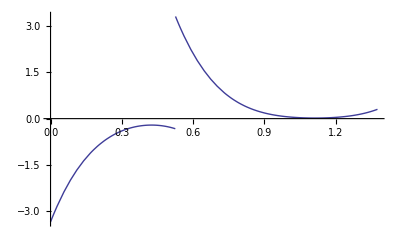

Piecewise[{{-3.3504+19.6932 u-46.3015 u^2+54.4306 u^3-31.9935 u^4, 0.≤u<0.525731}, {33.8062-115.286 u+149.835 u^2-88.0706 u^3+19.7731 u^4, 0.525731≤u<1.37638}, {0., True}}]

{a[0]→0.0662502,b[0]→-0.0657115,a[1]→-0.204724,b[1]→0.3242,a[2]→0.253053,b[2]→-0.625582,a[3]→-0.156395,b[3]→0.565844,a[4]→0.0483289,b[4]→-0.204724}

```mathematica
l=1;
λ/.λSol[n][[l]]/.σSol//N
1/σ^6/.σSol//N
f[norm_,u_]:=Poly[norm,n,u]/.Flatten[Table[{vector[n][[i]]->  ρ[n][[l,1,i]]},{i,Length[vector[n]]}]]/.A2Sol/.αβSol/.ϕSol/.σSol
f[1,u]//N
Integrate[f[1,u]//N,{u,0,A2/.A2Sol}]//N//Chop
halfnorm=2*Integrate[f[1,u]//N,{u,α/.αSol,A2/.A2Sol}]//N//Chop
Plot[f[halfnorm,u]//N,{u,0,A2/.A2Sol},PlotRange->Full,ImageSize->Scaled[0.5]]
f[halfnorm,u]//N
Flatten[Table[{vector[n][[i]]->  ρ[n][[l,1,i]]},{i,Length[vector[n]]}]]
```

```mathematica
ψ[7,1,u_]:=Poly[-0.01977378298966179,4,u]/.{a[0]->0.06625018002996023,b[0]->-0.0657115250736346,a[1]->-0.20472431509657432,b[1]->0.324199815230455,a[2]->0.2530531701064519,b[2]->-0.6255818403467838,a[3]->-0.15639546008669583,b[3]->0.5658440902798425,a[4]->0.048328855009877825,b[4]->-0.2047243150965735}/.A2Sol/.αβSol/.ϕSol/.σSol//N
𝕍[7]:={1/σ^6/.σSol//N//N,1}
ψ[7,1,u]
```

Piecewise[{{-3.3504+19.6932 u-46.3015 u^2+54.4306 u^3-31.9935 u^4, 0.≤u<0.525731}, {33.8062-115.286 u+149.835 u^2-88.0706 u^3+19.7731 u^4, 0.525731≤u<1.37638}, {0., True}}]

#### order 5

```mathematica
n=5;
Subscript[LPoly, A][n]=Collect[(Subscript[Poly, A][n,u/σ]+Subscript[Poly, B][n,u/σ+α])/σ,u,Simplify]
Subscript[LPoly, B][n]=Collect[(Subscript[Poly, A][n,u/σ]+Subscript[Poly, B][n,u/σ+α]+Subscript[Poly, B][n,u/σ+β])/σ,u,Simplify]
```

(a[0]+b[0])/σ+(u (β a[1]+α b[1]))/(α β σ^2)+(u^2 (a[2]/α^2+b[2]/β^2))/σ^3+(u^3 (a[3]/α^3+b[3]/β^3))/σ^4+(u^4 (a[4]/α^4+b[4]/β^4))/σ^5+(u^5 (a[5]/α^5+b[5]/β^5))/σ^6

(u^5 (a[5]/α^5+(2 b[5])/β^5))/σ^6+(u^4 (β^5 a[4]-5 α^5 b[5]+α^4 β (2 b[4]+5 b[5])))/(α^4 β^5 σ^5)+(u^3 (β^5 a[3]+10 α^5 b[5]-4 α^4 β (b[4]+5 b[5])+2 α^3 β^2 (b[3]+2 b[4]+5 b[5])))/(α^3 β^5 σ^4)+1/(α β^5 σ^2)u (β^5 a[1]+5 α^5 b[5]-4 α^4 β (b[4]+5 b[5])+α β^4 (2 b[1]+2 b[2]+3 b[3]+4 b[4]+5 b[5])+3 α^3 β^2 (b[3]+4 b[4]+10 b[5])-2 α^2 β^3 (b[2]+3 b[3]+6 b[4]+10 b[5]))+1/(β^5 σ)(-α^5 b[5]+β^5 (a[0]+2 b[0]+b[1]+b[2]+b[3]+b[4]+b[5])+α^4 β (b[4]+5 b[5])-α β^4 (b[1]+2 b[2]+3 b[3]+4 b[4]+5 b[5])-α^3 β^2 (b[3]+4 b[4]+10 b[5])+α^2 β^3 (b[2]+3 b[3]+6 b[4]+10 b[5]))+(u^2 (β^5 a[2]-10 α^5 b[5]+6 α^4 β (b[4]+5 b[5])-3 α^3 β^2 (b[3]+4 b[4]+10 b[5])+α^2 β^3 (2 b[2]+3 b[3]+6 b[4]+10 b[5])))/(α^2 β^5 σ^3)

```mathematica
vector[n]=Table[{a[i],b[i]},{i,0,n}]//Flatten;
```

```mathematica
Subscript[lhs, A][n,i_]:=Coefficient[Subscript[LPoly, A][n],u,i]
Subscript[lhs, B][n,i_]:=Coefficient[Subscript[LPoly, B][n],u,i]
L[n]={};
Do[
L[n]=Append[L[n],Coefficient[Subscript[lhs, A][n,i],#]&/@vector[n]];
L[n]=Append[L[n],Coefficient[Subscript[lhs, B][n,i],#]&/@vector[n]],
{i,0,n}]
L[n]//Simplify//TraditionalForm
Subscript[rhs, A][n,i_]:=Coefficient[Subscript[Poly, A][n,u],u,i]
Subscript[rhs, B][n,i_]:=Coefficient[Subscript[Poly, B][n,u],u,i]
J[n]={};
Do[
J[n]=Append[J[n],Coefficient[Subscript[rhs, A][n,i],#]&/@vector[n]];
J[n]=Append[J[n],Coefficient[Subscript[rhs, B][n,i],#]&/@vector[n]],
{i,0,n}]
J[n]//TraditionalForm
```

(1/σ | 1/σ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/σ | 2/σ | 0 | (β-α)/(β σ) | 0 | (α-β)^2/(β^2 σ) | 0 | -(α-β)^3/(β^3 σ) | 0 | (α-β)^4/(β^4 σ) | 0 | -(α-β)^5/(β^5 σ)
0 | 0 | 1/(α σ^2) | 1/(β σ^2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/(α σ^2) | 2/(β σ^2) | 0 | -(2 (α-β))/(β^2 σ^2) | 0 | (3 (α-β)^2)/(β^3 σ^2) | 0 | -(4 (α-β)^3)/(β^4 σ^2) | 0 | (5 (α-β)^4)/(β^5 σ^2)
0 | 0 | 0 | 0 | 1/(α^2 σ^3) | 1/(β^2 σ^3) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/(α^2 σ^3) | 2/(β^2 σ^3) | 0 | -(3 (α-β))/(β^3 σ^3) | 0 | (6 (α-β)^2)/(β^4 σ^3) | 0 | -(10 (α-β)^3)/(β^5 σ^3)
0 | 0 | 0 | 0 | 0 | 0 | 1/(α^3 σ^4) | 1/(β^3 σ^4) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/(α^3 σ^4) | 2/(β^3 σ^4) | 0 | -(4 (α-β))/(β^4 σ^4) | 0 | (10 (α-β)^2)/(β^5 σ^4)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(α^4 σ^5) | 1/(β^4 σ^5) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(α^4 σ^5) | 2/(β^4 σ^5) | 0 | -(5 (α-β))/(β^5 σ^5)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(α^5 σ^6) | 1/(β^5 σ^6)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(α^5 σ^6) | 2/(β^5 σ^6))

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | -α/β | 0 | α^2/β^2 | 0 | -α^3/β^3 | 0 | α^4/β^4 | 0 | -α^5/β^5
0 | 0 | 1/α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/β | 0 | -(2 α)/β^2 | 0 | (3 α^2)/β^3 | 0 | -(4 α^3)/β^4 | 0 | (5 α^4)/β^5
0 | 0 | 0 | 0 | 1/α^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/β^2 | 0 | -(3 α)/β^3 | 0 | (6 α^2)/β^4 | 0 | -(10 α^3)/β^5
0 | 0 | 0 | 0 | 0 | 0 | 1/α^3 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/β^3 | 0 | -(4 α)/β^4 | 0 | (10 α^2)/β^5
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/α^4 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/β^4 | 0 | -(5 α)/β^5
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/α^5 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/β^5)

```mathematica
determinant[n]=Det[L[n]-λ J[n]]//Simplify
```

((1-3 λ σ+λ^2 σ^2) (1-3 λ σ^2+λ^2 σ^4) (1-3 λ σ^3+λ^2 σ^6) (1-3 λ σ^4+λ^2 σ^8) (1-3 λ σ^5+λ^2 σ^10) (1-3 λ σ^6+λ^2 σ^12))/(α^15 β^15 σ^42)

```mathematica
λSol[n]=Solve[determinant[n]==0,λ]
```

{{λ→(3-√5)/(2 σ^6)},{λ→(3+√5)/(2 σ^6)},{λ→(3-√5)/(2 σ^5)},{λ→(3+√5)/(2 σ^5)},{λ→(3-√5)/(2 σ^4)},{λ→(3+√5)/(2 σ^4)},{λ→(3-√5)/(2 σ^3)},{λ→(3+√5)/(2 σ^3)},{λ→(3-√5)/(2 σ^2)},{λ→(3+√5)/(2 σ^2)},{λ→(3-√5)/(2 σ)},{λ→(3+√5)/(2 σ)}}

```mathematica
λSol[n]/.σSol//Simplify
%//N
```

{{λ→1/2 (843-377 √5)},{λ→32/(3+√5)^5},{λ→161-72 √5},{λ→16/(3+√5)^4},{λ→1/2 (123-55 √5)},{λ→9-4 √5},{λ→1/2 (47-21 √5)},{λ→4/(3+√5)^2},{λ→9-4 √5},{λ→2/(3+√5)},{λ→1/2 (7-3 √5)},{λ→1}}

{{λ→0.00118624},{λ→0.00813062},{λ→0.00310562},{λ→0.0212862},{λ→0.00813062},{λ→0.0557281},{λ→0.0212862},{λ→0.145898},{λ→0.0557281},{λ→0.381966},{λ→0.145898},{λ→1.}}

```mathematica
LN[n]=(L[n]/.αβSol/.σSol)//N//Chop
JN[n]=(J[n]/.αβSol/.σSol)//N//Chop
```

{{0.381966,0.381966,0,0,0,0,0,0,0,0,0,0},{0.381966,0.763932,0,0.145898,0,0.0557281,0,0.0212862,0,0.00813062,0,0.00310562},{0,0,0.277515,0.171513,0,0,0,0,0,0,0,0},{0,0,0.277515,0.343027,0,0.131025,0,0.0750704,0,0.0382325,0,0.0182544},{0,0,0,0,0.201626,0.0770143,0,0,0,0,0,0},{0,0,0,0,0.201626,0.154029,0,0.0882506,0,0.0674174,0,0.0429186},{0,0,0,0,0,0,0.14649,0.0345816,0,0,0,0},{0,0,0,0,0,0,0.14649,0.0691632,0,0.052836,0,0.0504539},{0,0,0,0,0,0,0,0,0.106431,0.0155281,0,0},{0,0,0,0,0,0,0,0,0.106431,0.0310562,0,0.029656},{0,0,0,0,0,0,0,0,0,0,0.0773268,0.00697255},{0,0,0,0,0,0,0,0,0,0,0.0773268,0.0139451}}

{{1.,0,0,0,0,0,0,0,0,0,0,0},{0,1.,0,-0.618034,0,0.381966,0,-0.236068,0,0.145898,0,-0.0901699},{0,0,1.90211,0,0,0,0,0,0,0,0,0},{0,0,0,1.17557,0,-1.45309,0,1.34708,0,-1.11006,0,0.857567},{0,0,0,0,3.61803,0,0,0,0,0,0,0},{0,0,0,0,0,1.38197,0,-2.56231,0,3.16718,0,-3.26238},{0,0,0,0,0,0,6.88191,0,0,0,0,0},{0,0,0,0,0,0,0,1.6246,0,-4.01623,0,6.20541},{0,0,0,0,0,0,0,0,13.0902,0,0,0},{0,0,0,0,0,0,0,0,0,1.90983,0,-5.9017},{0,0,0,0,0,0,0,0,0,0,24.899,0},{0,0,0,0,0,0,0,0,0,0,0,2.24514}}

```mathematica
ρ[n]=Table[
NullSpace[(LN[n]-λ JN[n])/.λSol[n][[i]]/.σSol//N],
{i,Length[λSol[n]]}]//Chop
Length/@%
λSol[n]/.σSol//Simplify;
%//N
```

{{{0.0340714,-0.0339656,-0.126344,0.202766,0.195212,-0.500192,-0.160863,0.643453,0.0745642,-0.436507,-0.0184333,0.126344}},{{0.0436433,-0.0427143,-0.107892,0.164845,0.165365,-0.369768,-0.20275,0.530806,0.403847,0,-0.0308512,-0.553602},{-0.128125,0.125397,0.316742,-0.483938,-0.243436,0.54434,-0.00311563,0.00815683,0.31025,0,-0.023701,-0.425298}},{{0.0662502,-0.0657115,-0.204724,0.3242,0.253053,-0.625582,-0.156395,0.565844,0.0483289,-0.204724,0,0}},{{0.0635848,-0.0600413,-0.0646173,0.0892989,-0.124694,0.20176,0.65852,0,-0.0628831,-0.697384,0,0},{-0.245871,0.232169,0.455242,-0.629128,-0.279415,0.452103,-0.00775953,0,0.000740969,0.00821747,0,0}},{{-0.094137,0.0921332,0.23272,-0.355564,-0.253423,0.56667,0.18204,-0.476588,-0.232874,0,0.01779,0.319228},{0.0972568,-0.0951866,-0.240432,0.367348,0.149612,-0.334543,0.0893228,-0.23385,-0.452899,0,0.0345984,0.620843}},{{-0.125058,0.106813,0.268385,-0.268385,-0.682826,0,0.0869387,0.595887,0,0,0,0},{0.444366,-0.379534,-0.499275,0.499275,-0.299945,0,0.0381896,0.261755,0,0,0,0}},{{0.253759,-0.239618,-0.454519,0.62813,0.231539,-0.374638,0.197478,0,-0.0188575,-0.209133,0,0},{-0.0100791,0.00951744,0.0695151,-0.0960674,-0.200028,0.323652,0.62826,0,-0.0599935,-0.665338,0,0}},{{-0.850349,0.525545,0.020468,0,-0.00390904,-0.016559,0,0,0,0,0,0},{-0.022641,0.0139929,-0.768735,0,0.146815,0.621919,0,0,0,0,0,0}},{{0.349857,-0.298813,-0.339038,0.339038,-0.560455,0,0.0713583,0.489097,0,0,0,0},{0.301166,-0.257226,-0.454269,0.454269,0.492044,0,-0.0626481,-0.429396,0,0,0,0}},{{-0.682646,0,0.260748,0.682646,0,0,0,0,0,0,0,0}},{{-0.449637,0.277891,0.652798,0,-0.124673,-0.528124,0,0,0,0,0,0},{-0.722104,0.446285,-0.406482,0,0.0776311,0.328851,0,0,0,0,0,0}},{{-0.525731,-0.850651,0,0,0,0,0,0,0,0,0,0}}}

{1,2,1,2,2,2,2,2,2,1,2,1}

{{λ→0.00118624},{λ→0.00813062},{λ→0.00310562},{λ→0.0212862},{λ→0.00813062},{λ→0.0557281},{λ→0.0212862},{λ→0.145898},{λ→0.0557281},{λ→0.381966},{λ→0.145898},{λ→1.}}

0.00813062

0.00813062

Piecewise[{{0.0436433-0.205223 u+0.598297 u^2-1.39531 u^3+5.28643 u^4-0.768163 u^5, 0.≤u<0.525731}, {-0.361221+0.971381 u-0.065036 u^2-2.57298 u^3+3.26719 u^4-1.24291 u^5, 0.525731≤u<1.37638}, {0., True}}]

0

-0.073349

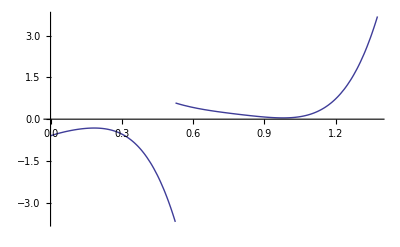

Piecewise[{{-0.595008+2.7979 u-8.15686 u^2+19.0228 u^3-72.0722 u^4+10.4727 u^5, 0.≤u<0.525731}, {4.92468-13.2433 u+0.886665 u^2+35.0786 u^3-44.5431 u^4+16.9452 u^5, 0.525731≤u<1.37638}, {0., True}}]

{a[0]→0.0436433,b[0]→-0.0427143,a[1]→-0.107892,b[1]→0.164845,a[2]→0.165365,b[2]→-0.369768,a[3]→-0.20275,b[3]→0.530806,a[4]→0.403847,b[4]→0,a[5]→-0.0308512,b[5]→-0.553602}

```mathematica
l=2;k=1;
λ/.λSol[n][[l]]/.σSol//N
1/σ^5/.σSol//N
f[norm_,u_]:=Poly[norm,n,u]/.Flatten[Table[{vector[n][[i]]->  ρ[n][[l,k,i]]},{i,Length[vector[n]]}]]/.A2Sol/.αβSol/.ϕSol/.σSol
f[1,u]//N
Integrate[f[1,u]//N,{u,0,A2/.A2Sol}]//N//Chop
halfnorm=2*Integrate[f[1,u]//N,{u,α/.αSol,A2/.A2Sol}]//N//Chop
Plot[f[halfnorm,u]//N,{u,0,A2/.A2Sol},PlotRange->Full,ImageSize->Scaled[0.5]]
f[halfnorm,u]//N
Flatten[Table[{vector[n][[i]]->  ρ[n][[l,k,i]]},{i,Length[vector[n]]}]]
```

```mathematica
ψ[6,2,u_]:=Poly[-0.0733490207813369,5,u]/.{a[0]->0.04364328539919925,b[0]->-0.042714284115369344,a[1]->-0.10789213502966823,b[1]->0.16484451385016072,a[2]->0.16536534270852532,b[2]->-0.36976814741881175,a[3]->-0.20274996710787205,b[3]->0.5308063051063319,a[4]->0.40384709661333007,b[4]->0,a[5]->-0.03085117292966599,b[5]->-0.5536018357923307}/.A2Sol/.αβSol/.ϕSol/.σSol//N
𝕍[6]:={1/σ^5/.σSol//N,2}
ψ[6,2,u]
```

Piecewise[{{-0.595008+2.7979 u-8.15686 u^2+19.0228 u^3-72.0722 u^4+10.4727 u^5, 0.≤u<0.525731}, {4.92468-13.2433 u+0.886665 u^2+35.0786 u^3-44.5431 u^4+16.9452 u^5, 0.525731≤u<1.37638}, {0., True}}]

0.00118624

0.00118624

Piecewise[{{0.0340714-0.24032 u+0.706282 u^2-1.10705 u^3+0.976058 u^4-0.45897 u^5, 0.≤u<0.525731}, {-0.577315+2.42487 u-4.13465 u^2+3.58248 u^3-1.5793 u^4+0.283659 u^5, 0.525731≤u<1.37638}, {0., True}}]

0

-0.00798578

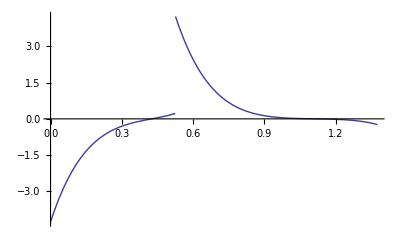

Piecewise[{{-4.2665+30.0935 u-88.4425 u^2+138.627 u^3-122.224 u^4+57.4734 u^5, 0.≤u<0.525731}, {72.2928-303.648 u+517.751 u^2-448.607 u^3+197.763 u^4-35.5205 u^5, 0.525731≤u<1.37638}, {0., True}}]

{a[0]→0.0340714,b[0]→-0.0339656,a[1]→-0.126344,b[1]→0.202766,a[2]→0.195212,b[2]→-0.500192,a[3]→-0.160863,b[3]→0.643453,a[4]→0.0745642,b[4]→-0.436507,a[5]→-0.0184333,b[5]→0.126344}

```mathematica
l=1;k=1;
λ/.λSol[n][[l]]/.σSol//N
1/σ^7/.σSol//N
f[norm_,u_]:=Poly[norm,n,u]/.Flatten[Table[{vector[n][[i]]->  ρ[n][[l,k,i]]},{i,Length[vector[n]]}]]/.A2Sol/.αβSol/.ϕSol/.σSol
f[1,u]//N
Integrate[f[1,u]//N,{u,0,A2/.A2Sol}]//N//Chop
halfnorm=2*Integrate[f[1,u]//N,{u,α/.αSol,A2/.A2Sol}]//N//Chop
Plot[f[halfnorm,u]//N,{u,0,A2/.A2Sol},PlotRange->Full,ImageSize->Scaled[0.5]]
f[halfnorm,u]//N
Flatten[Table[{vector[n][[i]]->  ρ[n][[l,k,i]]},{i,Length[vector[n]]}]]
```

```mathematica
ψ[8,1,u_]:=Poly[-0.007985784626829574,5,u]/.{a[0]->0.03407138351126936,b[0]->-0.033965570740693174,a[1]->-0.1263436383221836,b[1]->0.2027661724887435,a[2]->0.19521165686358363,b[2]->-0.5001919798861362,a[3]->-0.16086325192250192,b[3]->0.6434530076900085,a[4]->0.07456421792170753,b[4]->-0.4365065347473381,a[5]->-0.0184332884080678,b[5]->0.1263436383221844}/.A2Sol/.αβSol/.ϕSol/.σSol//N
𝕍[8]:={1/σ^7/.σSol//N,1}
ψ[8,1,u]
```

Piecewise[{{-4.2665+30.0935 u-88.4425 u^2+138.627 u^3-122.224 u^4+57.4734 u^5, 0.≤u<0.525731}, {72.2928-303.648 u+517.751 u^2-448.607 u^3+197.763 u^4-35.5205 u^5, 0.525731≤u<1.37638}, {0., True}}]

#### order 6

```mathematica
n=6;
Subscript[LPoly, A][n]=Collect[(Subscript[Poly, A][n,u/σ]+Subscript[Poly, B][n,u/σ+α])/σ,u,Simplify]
Subscript[LPoly, B][n]=Collect[(Subscript[Poly, A][n,u/σ]+Subscript[Poly, B][n,u/σ+α]+Subscript[Poly, B][n,u/σ+β])/σ,u,Simplify]
```

(a[0]+b[0])/σ+(u (β a[1]+α b[1]))/(α β σ^2)+(u^2 (a[2]/α^2+b[2]/β^2))/σ^3+(u^3 (a[3]/α^3+b[3]/β^3))/σ^4+(u^4 (a[4]/α^4+b[4]/β^4))/σ^5+(u^5 (a[5]/α^5+b[5]/β^5))/σ^6+(u^6 (a[6]/α^6+b[6]/β^6))/σ^7

(u^6 (a[6]/α^6+(2 b[6])/β^6))/σ^7+(u^5 (β^6 a[5]-6 α^6 b[6]+2 α^5 β (b[5]+3 b[6])))/(α^5 β^6 σ^6)+(u^3 (β^6 a[3]-20 α^6 b[6]+10 α^5 β (b[5]+6 b[6])+2 α^3 β^3 (b[3]+2 b[4]+5 b[5]+10 b[6])-4 α^4 β^2 (b[4]+5 (b[5]+3 b[6]))))/(α^3 β^6 σ^4)+1/(α β^6 σ^2)u (β^6 a[1]-6 α^6 b[6]+5 α^5 β (b[5]+6 b[6])+α β^5 (2 b[1]+2 b[2]+3 b[3]+4 b[4]+5 b[5]+6 b[6])-2 α^2 β^4 (b[2]+3 b[3]+6 b[4]+10 b[5]+15 b[6])+3 α^3 β^3 (b[3]+4 b[4]+10 b[5]+20 b[6])-4 α^4 β^2 (b[4]+5 (b[5]+3 b[6])))+1/(β^6 σ)(α^6 b[6]+β^6 (a[0]+2 b[0]+b[1]+b[2]+b[3]+b[4]+b[5]+b[6])-α^5 β (b[5]+6 b[6])-α β^5 (b[1]+2 b[2]+3 b[3]+4 b[4]+5 b[5]+6 b[6])+α^2 β^4 (b[2]+3 b[3]+6 b[4]+10 b[5]+15 b[6])-α^3 β^3 (b[3]+4 b[4]+10 b[5]+20 b[6])+α^4 β^2 (b[4]+5 (b[5]+3 b[6])))+1/(α^2 β^6 σ^3)u^2 (β^6 a[2]+15 α^6 b[6]-10 α^5 β (b[5]+6 b[6])+α^2 β^4 (2 b[2]+3 b[3]+6 b[4]+10 b[5]+15 b[6])-3 α^3 β^3 (b[3]+4 b[4]+10 b[5]+20 b[6])+6 α^4 β^2 (b[4]+5 (b[5]+3 b[6])))+(u^4 (β^6 a[4]+15 α^6 b[6]-5 α^5 β (b[5]+6 b[6])+α^4 β^2 (2 b[4]+5 (b[5]+3 b[6]))))/(α^4 β^6 σ^5)

```mathematica
vector[n]=Table[{a[i],b[i]},{i,0,n}]//Flatten;
```

```mathematica
Subscript[lhs, A][n,i_]:=Coefficient[Subscript[LPoly, A][n],u,i]
Subscript[lhs, B][n,i_]:=Coefficient[Subscript[LPoly, B][n],u,i]
L[n]={};
Do[
L[n]=Append[L[n],Coefficient[Subscript[lhs, A][n,i],#]&/@vector[n]];
L[n]=Append[L[n],Coefficient[Subscript[lhs, B][n,i],#]&/@vector[n]],
{i,0,n}]
L[n]//Simplify//TraditionalForm
Subscript[rhs, A][n,i_]:=Coefficient[Subscript[Poly, A][n,u],u,i]
Subscript[rhs, B][n,i_]:=Coefficient[Subscript[Poly, B][n,u],u,i]
J[n]={};
Do[
J[n]=Append[J[n],Coefficient[Subscript[rhs, A][n,i],#]&/@vector[n]];
J[n]=Append[J[n],Coefficient[Subscript[rhs, B][n,i],#]&/@vector[n]],
{i,0,n}]
J[n]//TraditionalForm
```

(1/σ | 1/σ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/σ | 2/σ | 0 | (β-α)/(β σ) | 0 | (α-β)^2/(β^2 σ) | 0 | -(α-β)^3/(β^3 σ) | 0 | (α-β)^4/(β^4 σ) | 0 | -(α-β)^5/(β^5 σ) | 0 | (α-β)^6/(β^6 σ)
0 | 0 | 1/(α σ^2) | 1/(β σ^2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/(α σ^2) | 2/(β σ^2) | 0 | -(2 (α-β))/(β^2 σ^2) | 0 | (3 (α-β)^2)/(β^3 σ^2) | 0 | -(4 (α-β)^3)/(β^4 σ^2) | 0 | (5 (α-β)^4)/(β^5 σ^2) | 0 | -(6 (α-β)^5)/(β^6 σ^2)
0 | 0 | 0 | 0 | 1/(α^2 σ^3) | 1/(β^2 σ^3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/(α^2 σ^3) | 2/(β^2 σ^3) | 0 | -(3 (α-β))/(β^3 σ^3) | 0 | (6 (α-β)^2)/(β^4 σ^3) | 0 | -(10 (α-β)^3)/(β^5 σ^3) | 0 | (15 (α-β)^4)/(β^6 σ^3)
0 | 0 | 0 | 0 | 0 | 0 | 1/(α^3 σ^4) | 1/(β^3 σ^4) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/(α^3 σ^4) | 2/(β^3 σ^4) | 0 | -(4 (α-β))/(β^4 σ^4) | 0 | (10 (α-β)^2)/(β^5 σ^4) | 0 | -(20 (α-β)^3)/(β^6 σ^4)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(α^4 σ^5) | 1/(β^4 σ^5) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(α^4 σ^5) | 2/(β^4 σ^5) | 0 | -(5 (α-β))/(β^5 σ^5) | 0 | (15 (α-β)^2)/(β^6 σ^5)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(α^5 σ^6) | 1/(β^5 σ^6) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(α^5 σ^6) | 2/(β^5 σ^6) | 0 | -(6 (α-β))/(β^6 σ^6)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(α^6 σ^7) | 1/(β^6 σ^7)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(α^6 σ^7) | 2/(β^6 σ^7))

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | -α/β | 0 | α^2/β^2 | 0 | -α^3/β^3 | 0 | α^4/β^4 | 0 | -α^5/β^5 | 0 | α^6/β^6
0 | 0 | 1/α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/β | 0 | -(2 α)/β^2 | 0 | (3 α^2)/β^3 | 0 | -(4 α^3)/β^4 | 0 | (5 α^4)/β^5 | 0 | -(6 α^5)/β^6
0 | 0 | 0 | 0 | 1/α^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/β^2 | 0 | -(3 α)/β^3 | 0 | (6 α^2)/β^4 | 0 | -(10 α^3)/β^5 | 0 | (15 α^4)/β^6
0 | 0 | 0 | 0 | 0 | 0 | 1/α^3 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/β^3 | 0 | -(4 α)/β^4 | 0 | (10 α^2)/β^5 | 0 | -(20 α^3)/β^6
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/α^4 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/β^4 | 0 | -(5 α)/β^5 | 0 | (15 α^2)/β^6
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/α^5 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/β^5 | 0 | -(6 α)/β^6
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/α^6 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/β^6)

```mathematica
determinant[n]=Det[L[n]-λ J[n]]//Simplify
```

1/(α^21 β^21 σ^56)(1-3 λ σ+λ^2 σ^2) (1-3 λ σ^2+λ^2 σ^4) (1-3 λ σ^3+λ^2 σ^6) (1-3 λ σ^4+λ^2 σ^8) (1-3 λ σ^5+λ^2 σ^10) (1-3 λ σ^6+λ^2 σ^12) (1-3 λ σ^7+λ^2 σ^14)

```mathematica
λSol[n]=Solve[determinant[n]==0,λ]
```

{{λ→(3-√5)/(2 σ^7)},{λ→(3+√5)/(2 σ^7)},{λ→(3-√5)/(2 σ^6)},{λ→(3+√5)/(2 σ^6)},{λ→(3-√5)/(2 σ^5)},{λ→(3+√5)/(2 σ^5)},{λ→(3-√5)/(2 σ^4)},{λ→(3+√5)/(2 σ^4)},{λ→(3-√5)/(2 σ^3)},{λ→(3+√5)/(2 σ^3)},{λ→(3-√5)/(2 σ^2)},{λ→(3+√5)/(2 σ^2)},{λ→(3-√5)/(2 σ)},{λ→(3+√5)/(2 σ)}}

```mathematica
λSol[n]/.σSol//Simplify
%//N
```

{{λ→1/2 (2207-987 √5)},{λ→64/(3+√5)^6},{λ→1/2 (843-377 √5)},{λ→32/(3+√5)^5},{λ→161-72 √5},{λ→16/(3+√5)^4},{λ→1/2 (123-55 √5)},{λ→9-4 √5},{λ→1/2 (47-21 √5)},{λ→4/(3+√5)^2},{λ→9-4 √5},{λ→2/(3+√5)},{λ→1/2 (7-3 √5)},{λ→1}}

{{λ→0.000453104},{λ→0.00310562},{λ→0.00118624},{λ→0.00813062},{λ→0.00310562},{λ→0.0212862},{λ→0.00813062},{λ→0.0557281},{λ→0.0212862},{λ→0.145898},{λ→0.0557281},{λ→0.381966},{λ→0.145898},{λ→1.}}

```mathematica
LN[n]=(L[n]/.αβSol/.σSol)//N//Chop
JN[n]=(J[n]/.αβSol/.σSol)//N//Chop
```

{{0.381966,0.381966,0,0,0,0,0,0,0,0,0,0,0,0},{0.381966,0.763932,0,0.145898,0,0.0557281,0,0.0212862,0,0.00813062,0,0.00310562,0,0.00118624},{0,0,0.277515,0.171513,0,0,0,0,0,0,0,0,0,0},{0,0,0.277515,0.343027,0,0.131025,0,0.0750704,0,0.0382325,0,0.0182544,0,0.00836706},{0,0,0,0,0.201626,0.0770143,0,0,0,0,0,0,0,0},{0,0,0,0,0.201626,0.154029,0,0.0882506,0,0.0674174,0,0.0429186,0,0.0245902},{0,0,0,0,0,0,0.14649,0.0345816,0,0,0,0,0,0},{0,0,0,0,0,0,0.14649,0.0691632,0,0.052836,0,0.0504539,0,0.0385433},{0,0,0,0,0,0,0,0,0.106431,0.0155281,0,0,0,0},{0,0,0,0,0,0,0,0,0.106431,0.0310562,0,0.029656,0,0.0339828},{0,0,0,0,0,0,0,0,0,0,0.0773268,0.00697255,0,0},{0,0,0,0,0,0,0,0,0,0,0.0773268,0.0139451,0,0.0159797},{0,0,0,0,0,0,0,0,0,0,0,0,0.0561812,0.00313087},{0,0,0,0,0,0,0,0,0,0,0,0,0.0561812,0.00626174}}

{{1.,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1.,0,-0.618034,0,0.381966,0,-0.236068,0,0.145898,0,-0.0901699,0,0.0557281},{0,0,1.90211,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1.17557,0,-1.45309,0,1.34708,0,-1.11006,0,0.857567,0,-0.636007},{0,0,0,0,3.61803,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1.38197,0,-2.56231,0,3.16718,0,-3.26238,0,3.02439},{0,0,0,0,0,0,6.88191,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1.6246,0,-4.01623,0,6.20541,0,-7.67031},{0,0,0,0,0,0,0,0,13.0902,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1.90983,0,-5.9017,0,10.9424},{0,0,0,0,0,0,0,0,0,0,24.899,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,2.24514,0,-8.32544},{0,0,0,0,0,0,0,0,0,0,0,0,47.3607,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,2.63932}}

```mathematica
ρ[n]=Table[
NullSpace[(LN[n]-λ JN[n])/.λSol[n][[i]]/.σSol//N],
{i,Length[λSol[n]]}]//Chop
Length/@%
λSol[n]/.σSol//Simplify;
%//N
```

{{{0.0174827,-0.0174619,-0.0756342,0.121999,0.140233,-0.364151,-0.144448,0.598868,0.089274,-0.577794,-0.0331046,0.313572,0.00681993,-0.0756342}},{{0.0313563,-0.0311014,-0.115931,0.183587,0.143298,-0.354253,-0.00131775,0.00476767,-0.134394,0.569304,0.323524,0,-0.0205959,-0.597989},{0.0607509,-0.0602569,-0.183333,0.290324,0.226612,-0.560215,-0.160211,0.579648,0.0806522,-0.341648,-0.0747464,0,0.00475843,0.138158}},{{0.0340714,-0.0339656,-0.126344,0.202766,0.195212,-0.500192,-0.160863,0.643453,0.0745642,-0.436507,-0.0184333,0.126344,0,0}},{{-0.110534,0.108181,0.273255,-0.417497,-0.18668,0.41743,-0.0603712,0.158054,0.411863,0,-0.0314636,-0.564591,0,0},{-0.0781211,0.0764582,0.193126,-0.29507,-0.227502,0.50871,0.193578,-0.506795,-0.299527,0,0.0228818,0.410598,0,0}},{{0.0070809,-0.00702333,-0.04121,0.0652598,0.0509383,-0.125926,0.0571137,-0.206639,-0.154536,0.654627,0.32853,0,-0.0209145,-0.607242},{0.0679981,-0.0674453,-0.212961,0.337244,0.263235,-0.650752,-0.149691,0.541586,0.0261747,-0.110878,0.0481974,0,-0.00306829,-0.0890862}},{{0.234513,-0.221444,-0.441667,0.610368,0.29415,-0.475945,-0.0847401,0,0.00809196,0.0897413,0,0,0,0},{-0.0974632,0.0920318,0.127871,-0.176713,0.0842443,-0.13631,-0.653091,0,0.0623646,0.691634,0,0,0,0}},{{-0.10896,0.106641,0.269364,-0.411552,-0.182124,0.407241,-0.0642053,0.168092,0.417733,0,-0.031912,-0.572637,0,0},{-0.0803018,0.0785925,0.198517,-0.303307,-0.231166,0.516903,0.192341,-0.503554,-0.291285,0,0.0222522,0.399299,0,0}},{{-0.168166,0.143631,0.0869317,-0.0869317,0.725594,0,-0.0923841,-0.63321,0,0,0,0,0,0},{-0.429908,0.367185,0.560133,-0.560133,-0.172427,0,0.0219538,0.150473,0,0,0,0,0,0}},{{0.234424,-0.22136,-0.401996,0.555544,0.14755,-0.23874,0.403589,0,-0.0385394,-0.427408,0,0,0,0},{0.0976763,-0.092233,-0.223204,0.30846,0.268049,-0.433713,-0.520408,0,0.0496945,0.551121,0,0,0,0}},{{-0.383167,0.23681,-0.686575,0,0.131124,0.555451,0,0,0,0,0,0,0,0},{-0.759467,0.469376,0.346391,0,-0.0661548,-0.280236,0,0,0,0,0,0,0,0}},{{0.245579,-0.209749,-0.398582,0.398582,0.570179,0,-0.0725963,-0.497582,0,0,0,0,0,0},{-0.390886,0.333856,0.403038,-0.403038,0.480743,0,-0.0612092,-0.419534,0,0,0,0,0,0}},{{-0.682646,0,0.260748,0.682646,0,0,0,0,0,0,0,0,0,0}},{{-0.0956975,0.0591443,-0.764125,0,0.145935,0.61819,0,0,0,0,0,0,0,0},{-0.845251,0.522394,0.0865127,0,-0.0165224,-0.0699902,0,0,0,0,0,0,0,0}},{{-0.525731,-0.850651,0,0,0,0,0,0,0,0,0,0,0,0}}}

{1,2,1,2,2,2,2,2,2,2,2,1,2,1}

{{λ→0.000453104},{λ→0.00310562},{λ→0.00118624},{λ→0.00813062},{λ→0.00310562},{λ→0.0212862},{λ→0.00813062},{λ→0.0557281},{λ→0.0212862},{λ→0.145898},{λ→0.0557281},{λ→0.381966},{λ→0.145898},{λ→1.}}

0.00310562

0.00310562

Piecewise[{{0.0313563-0.220513 u+0.518458 u^2-0.00906865 u^3-1.75925 u^4+8.05542 u^5-0.975434 u^6, 0.≤u<0.525731}, {-0.231267+0.485366 u-0.507245 u^2+2.30806 u^3-5.45613 u^4+4.97852 u^5-1.57828 u^6, 0.525731≤u<1.37638}, {0., True}}]

0

-0.0472392

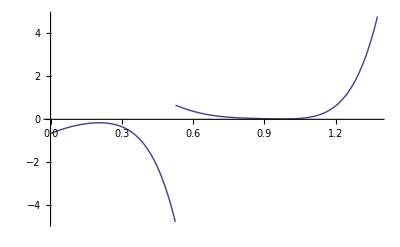

Piecewise[{{-0.663778+4.66802 u-10.9752 u^2+0.191973 u^3+37.2412 u^4-170.524 u^5+20.6488 u^6, 0.≤u<0.525731}, {4.89566-10.2746 u+10.7378 u^2-48.8589 u^3+115.5 u^4-105.39 u^5+33.4105 u^6, 0.525731≤u<1.37638}, {0., True}}]

{a[0]→0.0313563,b[0]→-0.0311014,a[1]→-0.115931,b[1]→0.183587,a[2]→0.143298,b[2]→-0.354253,a[3]→-0.00131775,b[3]→0.00476767,a[4]→-0.134394,b[4]→0.569304,a[5]→0.323524,b[5]→0,a[6]→-0.0205959,b[6]→-0.597989}

```mathematica
l=2;k=1;
λ/.λSol[n][[l]]/.σSol//N
1/σ^6/.σSol//N
f[norm_,u_]:=Poly[norm,n,u]/.Flatten[Table[{vector[n][[i]]->  ρ[n][[l,k,i]]},{i,Length[vector[n]]}]]/.A2Sol/.αβSol/.ϕSol/.σSol
f[1,u]//N
Integrate[f[1,u]//N,{u,0,A2/.A2Sol}]//N//Chop
halfnorm=2*Integrate[f[1,u]//N,{u,α/.αSol,A2/.A2Sol}]//N//Chop
Plot[f[halfnorm,u]//N,{u,0,A2/.A2Sol},PlotRange->Full,ImageSize->Scaled[0.5]]
f[halfnorm,u]//N
Flatten[Table[{vector[n][[i]]->  ρ[n][[l,k,i]]},{i,Length[vector[n]]}]]
```

```mathematica
ψ[7,2,u_]:=Poly[-0.04723917497544383,6,u]/.{a[0]->0.03135634063738153,b[0]->-0.0311013941860825,a[1]->-0.1159307138364837,b[1]->0.18358696663653748,a[2]->0.1432982429819711,b[2]->-0.3542527387639972,a[3]->-0.0013177515086869322,b[3]->0.004767669747155206,a[4]->-0.1343944000641455,b[4]->0.5693038144670225,a[5]->0.32352385841926345,b[5]->0,a[6]->-0.020595852957441565,b[6]->-0.5979890951211965}/.A2Sol/.αβSol/.ϕSol/.σSol//N
𝕍[7]:={1/σ^6/.σSol//N,2}
ψ[7,2,u]
```

Piecewise[{{-0.663778+4.66802 u-10.9752 u^2+0.191973 u^3+37.2412 u^4-170.524 u^5+20.6488 u^6, 0.≤u<0.525731}, {4.89566-10.2746 u+10.7378 u^2-48.8589 u^3+115.5 u^4-105.39 u^5+33.4105 u^6, 0.525731≤u<1.37638}, {0., True}}]

0.000453104

0.000453104

Piecewise[{{0.0174827-0.143865 u+0.507369 u^2-0.994081 u^3+1.16861 u^4-0.824272 u^5+0.322996 u^6, 0.≤u<0.525731}, {-0.490117+2.43768 u-5.11944 u^2+5.81945 u^3-3.78171 u^4+1.3337 u^5-0.199623 u^6, 0.525731≤u<1.37638}, {0., True}}]

0

-0.00379537

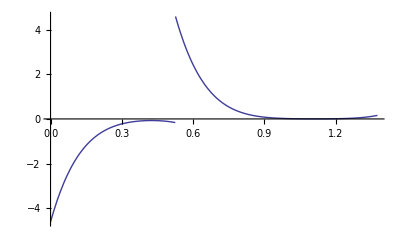

Piecewise[{{-4.60632+37.9054 u-133.681 u^2+261.92 u^3-307.905 u^4+217.178 u^5-85.1028 u^6, 0.≤u<0.525731}, {129.136-642.279 u+1348.87 u^2-1533.3 u^3+996.401 u^4-351.402 u^5+52.5964 u^6, 0.525731≤u<1.37638}, {0., True}}]

{a[0]→0.0174827,b[0]→-0.0174619,a[1]→-0.0756342,b[1]→0.121999,a[2]→0.140233,b[2]→-0.364151,a[3]→-0.144448,b[3]→0.598868,a[4]→0.089274,b[4]→-0.577794,a[5]→-0.0331046,b[5]→0.313572,a[6]→0.00681993,b[6]→-0.0756342}

```mathematica
l=1;k=1;
λ/.λSol[n][[l]]/.σSol//N
1/σ^8/.σSol//N
f[norm_,u_]:=Poly[norm,n,u]/.Flatten[Table[{vector[n][[i]]->  ρ[n][[l,k,i]]},{i,Length[vector[n]]}]]/.A2Sol/.αβSol/.ϕSol/.σSol
f[1,u]//N
Integrate[f[1,u]//N,{u,0,A2/.A2Sol}]//N//Chop
halfnorm=2*Integrate[f[1,u]//N,{u,α/.αSol,A2/.A2Sol}]//N//Chop
Plot[f[halfnorm,u]//N,{u,0,A2/.A2Sol},PlotRange->Full,ImageSize->Scaled[0.5]]
f[halfnorm,u]//N
Flatten[Table[{vector[n][[i]]->  ρ[n][[l,k,i]]},{i,Length[vector[n]]}]]
```

```mathematica
ψ[9,1,u_]:=Poly[-0.003795366248104781,6,u]/.{a[0]->0.017482663811615184,b[0]->-0.017461925153948912,a[1]->-0.0756341631462598,b[1]->0.12199858510674347,a[2]->0.14023345060512837,b[2]->-0.36415089768386216,a[3]->-0.14444839805608084,b[3]->0.598868329479089,a[4]->0.0892740196191324,b[4]->-0.577793592224324,a[5]->-0.03310462706216914,b[5]->0.3135715282724241,a[6]->0.006819928236436606,b[6]->-0.07563416314625859}/.A2Sol/.αβSol/.ϕSol/.σSol//N
𝕍[9]:={1/σ^8/.σSol//N,1}
ψ[9,1,u]
```

Piecewise[{{-4.60632+37.9054 u-133.681 u^2+261.92 u^3-307.905 u^4+217.178 u^5-85.1028 u^6, 0.≤u<0.525731}, {129.136-642.279 u+1348.87 u^2-1533.3 u^3+996.401 u^4-351.402 u^5+52.5964 u^6, 0.525731≤u<1.37638}, {0., True}}]

#### order 7

```mathematica
n=7;
Subscript[LPoly, A][n]=Collect[(Subscript[Poly, A][n,u/σ]+Subscript[Poly, B][n,u/σ+α])/σ,u,Simplify]
Subscript[LPoly, B][n]=Collect[(Subscript[Poly, A][n,u/σ]+Subscript[Poly, B][n,u/σ+α]+Subscript[Poly, B][n,u/σ+β])/σ,u,Simplify]
```

(a[0]+b[0])/σ+(u (β a[1]+α b[1]))/(α β σ^2)+(u^2 (a[2]/α^2+b[2]/β^2))/σ^3+(u^3 (a[3]/α^3+b[3]/β^3))/σ^4+(u^4 (a[4]/α^4+b[4]/β^4))/σ^5+(u^5 (a[5]/α^5+b[5]/β^5))/σ^6+(u^6 (a[6]/α^6+b[6]/β^6))/σ^7+(u^7 (a[7]/α^7+b[7]/β^7))/σ^8

(u^7 (a[7]/α^7+(2 b[7])/β^7))/σ^8+(u^6 (β^7 a[6]-7 α^7 b[7]+α^6 β (2 b[6]+7 b[7])))/(α^6 β^7 σ^7)+(u^5 (β^7 a[5]+21 α^7 b[7]-6 α^6 β (b[6]+7 b[7])+α^5 β^2 (2 b[5]+6 b[6]+21 b[7])))/(α^5 β^7 σ^6)+1/(α β^7 σ^2)u (β^7 a[1]+7 α^7 b[7]-6 α^6 β (b[6]+7 b[7])+α β^6 (2 b[1]+2 b[2]+3 b[3]+4 b[4]+5 b[5]+6 b[6]+7 b[7])+5 α^5 β^2 (b[5]+6 b[6]+21 b[7])-2 α^2 β^5 (b[2]+3 b[3]+6 b[4]+10 b[5]+15 b[6]+21 b[7])+3 α^3 β^4 (b[3]+4 b[4]+10 b[5]+20 b[6]+35 b[7])-4 α^4 β^3 (b[4]+5 (b[5]+3 b[6]+7 b[7])))+1/(α^3 β^7 σ^4)u^3 (β^7 a[3]+35 α^7 b[7]-20 α^6 β (b[6]+7 b[7])+10 α^5 β^2 (b[5]+6 b[6]+21 b[7])+α^3 β^4 (2 b[3]+4 b[4]+10 b[5]+20 b[6]+35 b[7])-4 α^4 β^3 (b[4]+5 (b[5]+3 b[6]+7 b[7])))+1/(β^7 σ)(-α^7 b[7]+β^7 (a[0]+2 b[0]+b[1]+b[2]+b[3]+b[4]+b[5]+b[6]+b[7])+α^6 β (b[6]+7 b[7])-α β^6 (b[1]+2 b[2]+3 b[3]+4 b[4]+5 b[5]+6 b[6]+7 b[7])-α^5 β^2 (b[5]+6 b[6]+21 b[7])+α^2 β^5 (b[2]+3 b[3]+6 b[4]+10 b[5]+15 b[6]+21 b[7])-α^3 β^4 (b[3]+4 b[4]+10 b[5]+20 b[6]+35 b[7])+α^4 β^3 (b[4]+5 (b[5]+3 b[6]+7 b[7])))+1/(α^2 β^7 σ^3)u^2 (β^7 a[2]-21 α^7 b[7]+15 α^6 β (b[6]+7 b[7])-10 α^5 β^2 (b[5]+6 b[6]+21 b[7])+α^2 β^5 (2 b[2]+3 b[3]+6 b[4]+10 b[5]+15 b[6]+21 b[7])-3 α^3 β^4 (b[3]+4 b[4]+10 b[5]+20 b[6]+35 b[7])+6 α^4 β^3 (b[4]+5 (b[5]+3 b[6]+7 b[7])))+(u^4 (β^7 a[4]-35 α^7 b[7]+15 α^6 β (b[6]+7 b[7])-5 α^5 β^2 (b[5]+6 b[6]+21 b[7])+α^4 β^3 (2 b[4]+5 (b[5]+3 b[6]+7 b[7]))))/(α^4 β^7 σ^5)

```mathematica
vector[n]=Table[{a[i],b[i]},{i,0,n}]//Flatten;
```

```mathematica
Subscript[lhs, A][n,i_]:=Coefficient[Subscript[LPoly, A][n],u,i]
Subscript[lhs, B][n,i_]:=Coefficient[Subscript[LPoly, B][n],u,i]
L[n]={};
Do[
L[n]=Append[L[n],Coefficient[Subscript[lhs, A][n,i],#]&/@vector[n]];
L[n]=Append[L[n],Coefficient[Subscript[lhs, B][n,i],#]&/@vector[n]],
{i,0,n}]
L[n]//Simplify//TraditionalForm
Subscript[rhs, A][n,i_]:=Coefficient[Subscript[Poly, A][n,u],u,i]
Subscript[rhs, B][n,i_]:=Coefficient[Subscript[Poly, B][n,u],u,i]
J[n]={};
Do[
J[n]=Append[J[n],Coefficient[Subscript[rhs, A][n,i],#]&/@vector[n]];
J[n]=Append[J[n],Coefficient[Subscript[rhs, B][n,i],#]&/@vector[n]],
{i,0,n}]
J[n]//TraditionalForm
```

(1/σ | 1/σ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/σ | 2/σ | 0 | (β-α)/(β σ) | 0 | (α-β)^2/(β^2 σ) | 0 | -(α-β)^3/(β^3 σ) | 0 | (α-β)^4/(β^4 σ) | 0 | -(α-β)^5/(β^5 σ) | 0 | (α-β)^6/(β^6 σ) | 0 | -(α-β)^7/(β^7 σ)
0 | 0 | 1/(α σ^2) | 1/(β σ^2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/(α σ^2) | 2/(β σ^2) | 0 | -(2 (α-β))/(β^2 σ^2) | 0 | (3 (α-β)^2)/(β^3 σ^2) | 0 | -(4 (α-β)^3)/(β^4 σ^2) | 0 | (5 (α-β)^4)/(β^5 σ^2) | 0 | -(6 (α-β)^5)/(β^6 σ^2) | 0 | (7 (α-β)^6)/(β^7 σ^2)
0 | 0 | 0 | 0 | 1/(α^2 σ^3) | 1/(β^2 σ^3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/(α^2 σ^3) | 2/(β^2 σ^3) | 0 | -(3 (α-β))/(β^3 σ^3) | 0 | (6 (α-β)^2)/(β^4 σ^3) | 0 | -(10 (α-β)^3)/(β^5 σ^3) | 0 | (15 (α-β)^4)/(β^6 σ^3) | 0 | -(21 (α-β)^5)/(β^7 σ^3)
0 | 0 | 0 | 0 | 0 | 0 | 1/(α^3 σ^4) | 1/(β^3 σ^4) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/(α^3 σ^4) | 2/(β^3 σ^4) | 0 | -(4 (α-β))/(β^4 σ^4) | 0 | (10 (α-β)^2)/(β^5 σ^4) | 0 | -(20 (α-β)^3)/(β^6 σ^4) | 0 | (35 (α-β)^4)/(β^7 σ^4)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(α^4 σ^5) | 1/(β^4 σ^5) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(α^4 σ^5) | 2/(β^4 σ^5) | 0 | -(5 (α-β))/(β^5 σ^5) | 0 | (15 (α-β)^2)/(β^6 σ^5) | 0 | -(35 (α-β)^3)/(β^7 σ^5)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(α^5 σ^6) | 1/(β^5 σ^6) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(α^5 σ^6) | 2/(β^5 σ^6) | 0 | -(6 (α-β))/(β^6 σ^6) | 0 | (21 (α-β)^2)/(β^7 σ^6)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(α^6 σ^7) | 1/(β^6 σ^7) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(α^6 σ^7) | 2/(β^6 σ^7) | 0 | -(7 (α-β))/(β^7 σ^7)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(α^7 σ^8) | 1/(β^7 σ^8)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(α^7 σ^8) | 2/(β^7 σ^8))

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | -α/β | 0 | α^2/β^2 | 0 | -α^3/β^3 | 0 | α^4/β^4 | 0 | -α^5/β^5 | 0 | α^6/β^6 | 0 | -α^7/β^7
0 | 0 | 1/α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/β | 0 | -(2 α)/β^2 | 0 | (3 α^2)/β^3 | 0 | -(4 α^3)/β^4 | 0 | (5 α^4)/β^5 | 0 | -(6 α^5)/β^6 | 0 | (7 α^6)/β^7
0 | 0 | 0 | 0 | 1/α^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/β^2 | 0 | -(3 α)/β^3 | 0 | (6 α^2)/β^4 | 0 | -(10 α^3)/β^5 | 0 | (15 α^4)/β^6 | 0 | -(21 α^5)/β^7
0 | 0 | 0 | 0 | 0 | 0 | 1/α^3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/β^3 | 0 | -(4 α)/β^4 | 0 | (10 α^2)/β^5 | 0 | -(20 α^3)/β^6 | 0 | (35 α^4)/β^7
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/α^4 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/β^4 | 0 | -(5 α)/β^5 | 0 | (15 α^2)/β^6 | 0 | -(35 α^3)/β^7
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/α^5 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/β^5 | 0 | -(6 α)/β^6 | 0 | (21 α^2)/β^7
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/α^6 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/β^6 | 0 | -(7 α)/β^7
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/α^7 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/β^7)

```mathematica
determinant[n]=Det[L[n]-λ J[n]]//Simplify
```

1/(α^28 β^28 σ^72)(1-3 λ σ+λ^2 σ^2) (1-3 λ σ^2+λ^2 σ^4) (1-3 λ σ^3+λ^2 σ^6) (1-3 λ σ^4+λ^2 σ^8) (1-3 λ σ^5+λ^2 σ^10) (1-3 λ σ^6+λ^2 σ^12) (1-3 λ σ^7+λ^2 σ^14) (1-3 λ σ^8+λ^2 σ^16)

```mathematica
λSol[n]=Solve[determinant[n]==0,λ]
```

{{λ→(3-√5)/(2 σ^8)},{λ→(3+√5)/(2 σ^8)},{λ→(3-√5)/(2 σ^7)},{λ→(3+√5)/(2 σ^7)},{λ→(3-√5)/(2 σ^6)},{λ→(3+√5)/(2 σ^6)},{λ→(3-√5)/(2 σ^5)},{λ→(3+√5)/(2 σ^5)},{λ→(3-√5)/(2 σ^4)},{λ→(3+√5)/(2 σ^4)},{λ→(3-√5)/(2 σ^3)},{λ→(3+√5)/(2 σ^3)},{λ→(3-√5)/(2 σ^2)},{λ→(3+√5)/(2 σ^2)},{λ→(3-√5)/(2 σ)},{λ→(3+√5)/(2 σ)}}

```mathematica
λSol[n]/.σSol//Simplify
%//N
```

{{λ→2889-1292 √5},{λ→128/(3+√5)^7},{λ→1/2 (2207-987 √5)},{λ→64/(3+√5)^6},{λ→1/2 (843-377 √5)},{λ→32/(3+√5)^5},{λ→161-72 √5},{λ→16/(3+√5)^4},{λ→1/2 (123-55 √5)},{λ→9-4 √5},{λ→1/2 (47-21 √5)},{λ→4/(3+√5)^2},{λ→9-4 √5},{λ→2/(3+√5)},{λ→1/2 (7-3 √5)},{λ→1}}

{{λ→0.00017307},{λ→0.00118624},{λ→0.000453104},{λ→0.00310562},{λ→0.00118624},{λ→0.00813062},{λ→0.00310562},{λ→0.0212862},{λ→0.00813062},{λ→0.0557281},{λ→0.0212862},{λ→0.145898},{λ→0.0557281},{λ→0.381966},{λ→0.145898},{λ→1.}}

```mathematica
LN[n]=(L[n]/.αβSol/.σSol)//N//Chop
JN[n]=(J[n]/.αβSol/.σSol)//N//Chop
```

{{0.381966,0.381966,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0.381966,0.763932,0,0.145898,0,0.0557281,0,0.0212862,0,0.00813062,0,0.00310562,0,0.00118624,0,0.000453104},{0,0,0.277515,0.171513,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0.277515,0.343027,0,0.131025,0,0.0750704,0,0.0382325,0,0.0182544,0,0.00836706,0,0.00372859},{0,0,0,0,0.201626,0.0770143,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0.201626,0.154029,0,0.0882506,0,0.0674174,0,0.0429186,0,0.0245902,0,0.0131497},{0,0,0,0,0,0,0.14649,0.0345816,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0.14649,0.0691632,0,0.052836,0,0.0504539,0,0.0385433,0,0.0257639},{0,0,0,0,0,0,0,0,0.106431,0.0155281,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0.106431,0.0310562,0,0.029656,0,0.0339828,0,0.0302873},{0,0,0,0,0,0,0,0,0,0,0.0773268,0.00697255,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0.0773268,0.0139451,0,0.0159797,0,0.0213629},{0,0,0,0,0,0,0,0,0,0,0,0,0.0561812,0.00313087,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0.0561812,0.00626174,0,0.0083712},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.040818,0.00140585},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.040818,0.0028117}}

{{1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1.,0,-0.618034,0,0.381966,0,-0.236068,0,0.145898,0,-0.0901699,0,0.0557281,0,-0.0344419},{0,0,1.90211,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1.17557,0,-1.45309,0,1.34708,0,-1.11006,0,0.857567,0,-0.636007,0,0.458586},{0,0,0,0,3.61803,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1.38197,0,-2.56231,0,3.16718,0,-3.26238,0,3.02439,0,-2.61685},{0,0,0,0,0,0,6.88191,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1.6246,0,-4.01623,0,6.20541,0,-7.67031,0,8.2959},{0,0,0,0,0,0,0,0,13.0902,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1.90983,0,-5.9017,0,10.9424,0,-15.7797},{0,0,0,0,0,0,0,0,0,0,24.899,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,2.24514,0,-8.32544,0,18.0089},{0,0,0,0,0,0,0,0,0,0,0,0,47.3607,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,2.63932,0,-11.4183},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,90.0854,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3.10271}}

```mathematica
ρ[n]=Table[
NullSpace[(LN[n]-λ JN[n])/.λSol[n][[i]]/.σSol//N],
{i,Length[λSol[n]]}]//Chop
Length/@%
λSol[n]/.σSol//Simplify;
%//N
```

{{{0.00895779,-0.00895373,-0.0442898,0.0715773,0.095804,-0.250039,-0.11842,0.497558,0.0914847,-0.613698,-0.0452325,0.473681,0.0139776,-0.214224,-0.00246818,0.0442898}},{{0.0277268,-0.0276407,-0.0940819,0.15099,0.12647,-0.324055,-0.104217,0.416869,0.0916092,-0.53629,-0.0761712,0.522085,0.107048,0,-0.00584125,-0.274415},{0.0198115,-0.01975,-0.0861901,0.138325,0.160697,-0.411754,-0.132421,0.529686,-0.00170251,0.00996669,0.078396,-0.537334,-0.15595,0,0.00850967,0.399773}},{{0.0174827,-0.0174619,-0.0756342,0.121999,0.140233,-0.364151,-0.144448,0.598868,0.089274,-0.577794,-0.0331046,0.313572,0.00681993,-0.0756342,0,0}},{{-0.00873852,0.00866747,0.0463958,-0.073472,-0.0573483,0.141773,-0.053443,0.193359,0.153852,-0.651726,-0.329608,0,0.0209832,0.609235,0,0},{0.067805,-0.0672538,-0.211892,0.335551,0.261913,-0.647485,-0.15104,0.546468,0.0299389,-0.126823,0.0401642,0,-0.00255689,-0.0742379,0,0}},{{0.0320513,-0.0319518,-0.113885,0.182771,0.165215,-0.423331,-0.136145,0.544578,0.0877355,-0.513612,-0.0521325,0.357321,0.0608862,0,-0.00332235,-0.15608},{0.0115752,-0.0115393,-0.0575362,0.0923386,0.120508,-0.308778,-0.099304,0.397216,-0.0264129,0.154624,0.0960738,-0.6585,-0.179088,0,0.00977224,0.459087}},{{0.133035,-0.130203,-0.32888,0.502485,0.293277,-0.655787,-0.0969144,0.253725,-0.0717668,0,0.00548249,0.0983794,0,0,0,0},{0.0249475,-0.0244165,-0.0616737,0.094229,-0.0244034,0.0545676,0.178115,-0.46631,-0.50418,0,0.0385159,0.69114,0,0,0,0}},{{0.0501325,-0.0497248,-0.171325,0.27131,0.21177,-0.523524,-0.0556749,0.201434,-0.0989953,0.419351,0.278879,0,-0.0177537,-0.51547,0,0},{-0.0464825,0.0461046,0.133035,-0.210674,-0.164441,0.40652,0.150232,-0.543543,-0.121518,0.514757,0.180225,0,-0.0114733,-0.33312,0,0}},{{0.210579,-0.198844,-0.350128,0.483866,0.0918345,-0.148591,0.498227,0,-0.0475765,-0.527631,0,0,0,0,0,0},{0.141957,-0.134046,-0.298044,0.411887,0.291869,-0.472255,-0.430672,0,0.0411255,0.456089,0,0,0,0,0,0}},{{0.0680098,-0.0665622,-0.16813,0.256879,0.0751015,-0.167932,0.135438,-0.35458,-0.499144,0,0.0381312,0.684236,0,0,0,0},{-0.117027,0.114536,0.289307,-0.442021,-0.284546,0.636265,0.15091,-0.395088,-0.101012,0,0.00771664,0.138469,0,0,0,0}},{{0.344587,-0.294313,-0.331118,0.331118,-0.568894,0,0.0724328,0.496462,0,0,0,0,0,0,0,0},{0.307181,-0.262364,-0.460073,0.460073,0.482262,0,-0.0614026,-0.42086,0,0,0,0,0,0,0,0}},{{0.243675,-0.230095,-0.452902,0.625894,0.283319,-0.45842,-0.0136424,0,0.00130273,0.0144475,0,0,0,0,0,0},{-0.0715405,0.0675537,0.0793757,-0.109695,0.115549,-0.186962,-0.658424,0,0.0628739,0.697282,0,0,0,0,0,0}},{{-0.745065,0.460475,0.371074,0,-0.0708688,-0.300205,0,0,0,0,0,0,0,0,0,0},{0.41047,-0.253684,0.673555,0,-0.128638,-0.544917,0,0,0,0,0,0,0,0,0,0}},{{-0.17566,0.150032,0.32438,-0.32438,-0.643511,0,0.0819331,0.561578,0,0,0,0,0,0,0,0},{0.4269,-0.364616,-0.464848,0.464848,-0.376977,0,0.0479974,0.328979,0,0,0,0,0,0,0,0}},{{0.682646,0,-0.260748,-0.682646,0,0,0,0,0,0,0,0,0,0,0,0}},{{0.771723,-0.476951,0.323497,0,-0.0617825,-0.261715,0,0,0,0,0,0,0,0,0,0},{0.357842,-0.221159,-0.697654,0,0.13324,0.564414,0,0,0,0,0,0,0,0,0,0}},{{-0.525731,-0.850651,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}}

{1,2,1,2,2,2,2,2,2,2,2,2,2,1,2,1}

{{λ→0.00017307},{λ→0.00118624},{λ→0.000453104},{λ→0.00310562},{λ→0.00118624},{λ→0.00813062},{λ→0.00310562},{λ→0.0212862},{λ→0.00813062},{λ→0.0557281},{λ→0.0212862},{λ→0.145898},{λ→0.0557281},{λ→0.381966},{λ→0.145898},{λ→1.}}

0.00118624

0.00118624

Piecewise[{{0.0277268-0.178954 u+0.457573 u^2-0.717213 u^3+1.19918 u^4-1.89658 u^5+5.06988 u^6-0.526212 u^7, 0.≤u<0.525731}, {-0.459014+2.12713 u-4.19964 u^2+3.79434 u^3+0.224781 u^4-3.76975 u^5+3.13336 u^6-0.851428 u^7, 0.525731≤u<1.37638}, {0., True}}]

0

-0.0178511

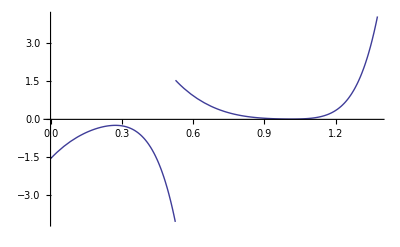

Piecewise[{{-1.55323+10.0248 u-25.6328 u^2+40.1775 u^3-67.1769 u^4+106.245 u^5-284.009 u^6+29.4778 u^7, 0.≤u<0.525731}, {25.7135-119.16 u+235.26 u^2-212.555 u^3-12.592 u^4+211.178 u^5-175.527 u^6+47.6961 u^7, 0.525731≤u<1.37638}, {0., True}}]

{a[0]→0.0277268,b[0]→-0.0276407,a[1]→-0.0940819,b[1]→0.15099,a[2]→0.12647,b[2]→-0.324055,a[3]→-0.104217,b[3]→0.416869,a[4]→0.0916092,b[4]→-0.53629,a[5]→-0.0761712,b[5]→0.522085,a[6]→0.107048,b[6]→0,a[7]→-0.00584125,b[7]→-0.274415}

```mathematica
l=2;k=1;
λ/.λSol[n][[l]]/.σSol//N
1/σ^7/.σSol//N
f[norm_,u_]:=Poly[norm,n,u]/.Flatten[Table[{vector[n][[i]]->  ρ[n][[l,k,i]]},{i,Length[vector[n]]}]]/.A2Sol/.αβSol/.ϕSol/.σSol
f[1,u]//N
Integrate[f[1,u]//N,{u,0,A2/.A2Sol}]//N//Chop
halfnorm=2*Integrate[f[1,u]//N,{u,α/.αSol,A2/.A2Sol}]//N//Chop
Plot[f[halfnorm,u]//N,{u,0,A2/.A2Sol},PlotRange->Full,ImageSize->Scaled[0.5]]
f[halfnorm,u]//N
Flatten[Table[{vector[n][[i]]->  ρ[n][[l,k,i]]},{i,Length[vector[n]]}]]
```

```mathematica
ψ[8,2,u_]:=Poly[-0.01785109342232027,7,u]/.{a[0]->0.02772680466395261,b[0]->-0.027640695744432307,a[1]->-0.09408189083770334,b[1]->0.15098999173206007,a[2]->0.12647020095512734,b[2]->-0.3240553419233011,a[3]->-0.1042171770057316,b[3]->0.416868708022926,a[4]->0.09160923433704594,b[4]->-0.5362897988591282,a[5]->-0.07617116010181764,b[5]->0.5220848982253896,a[6]->0.10704822380071748,b[6]->0,a[7]->-0.005841254722367008,b[7]->-0.27441463362321655}/.A2Sol/.αβSol/.ϕSol/.σSol//N
𝕍[8]:={1/σ^7/.σSol//N,2}
ψ[8,2,u]
```

Piecewise[{{-1.55323+10.0248 u-25.6328 u^2+40.1775 u^3-67.1769 u^4+106.245 u^5-284.009 u^6+29.4778 u^7, 0.≤u<0.525731}, {25.7135-119.16 u+235.26 u^2-212.555 u^3-12.592 u^4+211.178 u^5-175.527 u^6+47.6961 u^7, 0.525731≤u<1.37638}, {0., True}}]

0.00017307

0.00017307

Piecewise[{{0.00895779-0.0842441 u+0.346622 u^2-0.814958 u^3+1.19755 u^4-1.12624 u^5+0.661989 u^6-0.222347 u^7, 0.≤u<0.525731}, {-0.411868+2.36174 u-5.87326 u^2+8.22306 u^3-7.01058 u^4+3.6446 u^5-1.07112 u^6+0.137418 u^7, 0.525731≤u<1.37638}, {0., True}}]

0

-0.00167075

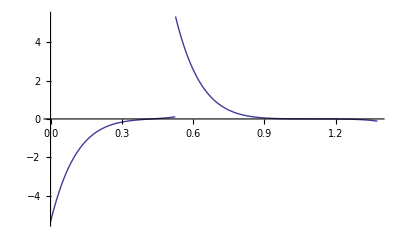

Piecewise[{{-5.36153+50.4228 u-207.465 u^2+487.779 u^3-716.773 u^4+674.093 u^5-396.222 u^6+133.082 u^7, 0.≤u<0.525731}, {246.516-1413.58 u+3515.34 u^2-4921.77 u^3+4196.06 u^4-2181.41 u^5+641.101 u^6-82.2492 u^7, 0.525731≤u<1.37638}, {0., True}}]

{a[0]→0.00895779,b[0]→-0.00895373,a[1]→-0.0442898,b[1]→0.0715773,a[2]→0.095804,b[2]→-0.250039,a[3]→-0.11842,b[3]→0.497558,a[4]→0.0914847,b[4]→-0.613698,a[5]→-0.0452325,b[5]→0.473681,a[6]→0.0139776,b[6]→-0.214224,a[7]→-0.00246818,b[7]→0.0442898}

```mathematica
l=1;k=1;
λ/.λSol[n][[l]]/.σSol//N
1/σ^9/.σSol//N
f[norm_,u_]:=Poly[norm,n,u]/.Flatten[Table[{vector[n][[i]]->  ρ[n][[l,k,i]]},{i,Length[vector[n]]}]]/.A2Sol/.αβSol/.ϕSol/.σSol
f[1,u]//N
Integrate[f[1,u]//N,{u,0,A2/.A2Sol}]//N//Chop
halfnorm=2*Integrate[f[1,u]//N,{u,α/.αSol,A2/.A2Sol}]//N//Chop
Plot[f[halfnorm,u]//N,{u,0,A2/.A2Sol},PlotRange->Full,ImageSize->Scaled[0.5]]
f[halfnorm,u]//N
Flatten[Table[{vector[n][[i]]->  ρ[n][[l,k,i]]},{i,Length[vector[n]]}]]
```

```mathematica
ψ[10,1,u_]:=Poly[-0.0016707531458920893,7,u]/.{a[0]->0.008957792149043076,b[0]->-0.008953733338898944,a[1]->-0.04428976009812304,b[1]->0.07157732836905217,a[2]->0.09580401982976432,b[2]->-0.2500392342126845,a[3]->-0.11842028102732528,b[3]->0.4975577463463638,a[4]->0.09148469829025128,b[4]->-0.6136980128341822,a[5]->-0.04523252239512383,b[5]->0.47368112410929797,a[6]->0.013977618118538591,b[6]->-0.214224300857087,a[7]->-0.002468183736863701,b[7]->0.044289760098121154}/.A2Sol/.αβSol/.ϕSol/.σSol//N
𝕍[10]:={1/σ^9/.σSol//N,1}
ψ[10,1,u]
```

Piecewise[{{-5.36153+50.4228 u-207.465 u^2+487.779 u^3-716.773 u^4+674.093 u^5-396.222 u^6+133.082 u^7, 0.≤u<0.525731}, {246.516-1413.58 u+3515.34 u^2-4921.77 u^3+4196.06 u^4-2181.41 u^5+641.101 u^6-82.2492 u^7, 0.525731≤u<1.37638}, {0., True}}]

#### order 8

```mathematica
n=8;
Subscript[LPoly, A][n]=Collect[(Subscript[Poly, A][n,u/σ]+Subscript[Poly, B][n,u/σ+α])/σ,u,Simplify]
Subscript[LPoly, B][n]=Collect[(Subscript[Poly, A][n,u/σ]+Subscript[Poly, B][n,u/σ+α]+Subscript[Poly, B][n,u/σ+β])/σ,u,Simplify]
```

(a[0]+b[0])/σ+(u (β a[1]+α b[1]))/(α β σ^2)+(u^2 (a[2]/α^2+b[2]/β^2))/σ^3+(u^3 (a[3]/α^3+b[3]/β^3))/σ^4+(u^4 (a[4]/α^4+b[4]/β^4))/σ^5+(u^5 (a[5]/α^5+b[5]/β^5))/σ^6+(u^6 (a[6]/α^6+b[6]/β^6))/σ^7+(u^7 (a[7]/α^7+b[7]/β^7))/σ^8+(u^8 (a[8]/α^8+b[8]/β^8))/σ^9

(u^8 (a[8]/α^8+(2 b[8])/β^8))/σ^9+(u^7 (β^8 a[7]-8 α^8 b[8]+2 α^7 β (b[7]+4 b[8])))/(α^7 β^8 σ^8)+(u^5 (β^8 a[5]-56 α^8 b[8]+21 α^7 β (b[7]+8 b[8])+α^5 β^3 (2 b[5]+6 b[6]+21 b[7]+56 b[8])-6 α^6 β^2 (b[6]+7 (b[7]+4 b[8]))))/(α^5 β^8 σ^6)+(u^6 (β^8 a[6]+28 α^8 b[8]-7 α^7 β (b[7]+8 b[8])+α^6 β^2 (2 b[6]+7 (b[7]+4 b[8]))))/(α^6 β^8 σ^7)+1/(α^3 β^8 σ^4)u^3 (β^8 a[3]-56 α^8 b[8]+35 α^7 β (b[7]+8 b[8])+10 α^5 β^3 (b[5]+6 b[6]+21 b[7]+56 b[8])+α^3 β^5 (2 b[3]+4 b[4]+10 b[5]+20 b[6]+35 b[7]+56 b[8])-20 α^6 β^2 (b[6]+7 (b[7]+4 b[8]))-4 α^4 β^4 (b[4]+5 (b[5]+3 b[6]+7 b[7]+14 b[8])))+1/(α β^8 σ^2)u (β^8 a[1]-8 α^8 b[8]+7 α^7 β (b[7]+8 b[8])+α β^7 (2 b[1]+2 b[2]+3 b[3]+4 b[4]+5 b[5]+6 b[6]+7 b[7]+8 b[8])-2 α^2 β^6 (b[2]+3 b[3]+6 b[4]+10 b[5]+15 b[6]+21 b[7]+28 b[8])+5 α^5 β^3 (b[5]+6 b[6]+21 b[7]+56 b[8])+3 α^3 β^5 (b[3]+4 b[4]+10 b[5]+20 b[6]+35 b[7]+56 b[8])-6 α^6 β^2 (b[6]+7 (b[7]+4 b[8]))-4 α^4 β^4 (b[4]+5 (b[5]+3 b[6]+7 b[7]+14 b[8])))+1/(β^8 σ)(α^8 b[8]+β^8 (a[0]+2 b[0]+b[1]+b[2]+b[3]+b[4]+b[5]+b[6]+b[7]+b[8])-α^7 β (b[7]+8 b[8])-α β^7 (b[1]+2 b[2]+3 b[3]+4 b[4]+5 b[5]+6 b[6]+7 b[7]+8 b[8])+α^2 β^6 (b[2]+3 b[3]+6 b[4]+10 b[5]+15 b[6]+21 b[7]+28 b[8])-α^5 β^3 (b[5]+6 b[6]+21 b[7]+56 b[8])-α^3 β^5 (b[3]+4 b[4]+10 b[5]+20 b[6]+35 b[7]+56 b[8])+α^6 β^2 (b[6]+7 (b[7]+4 b[8]))+α^4 β^4 (b[4]+5 (b[5]+3 b[6]+7 b[7]+14 b[8])))+1/(α^2 β^8 σ^3)u^2 (β^8 a[2]+28 α^8 b[8]-21 α^7 β (b[7]+8 b[8])+α^2 β^6 (2 b[2]+3 b[3]+6 b[4]+10 b[5]+15 b[6]+21 b[7]+28 b[8])-10 α^5 β^3 (b[5]+6 b[6]+21 b[7]+56 b[8])-3 α^3 β^5 (b[3]+4 b[4]+10 b[5]+20 b[6]+35 b[7]+56 b[8])+15 α^6 β^2 (b[6]+7 (b[7]+4 b[8]))+6 α^4 β^4 (b[4]+5 (b[5]+3 b[6]+7 b[7]+14 b[8])))+1/(α^4 β^8 σ^5)u^4 (β^8 a[4]+70 α^8 b[8]-35 α^7 β (b[7]+8 b[8])-5 α^5 β^3 (b[5]+6 b[6]+21 b[7]+56 b[8])+15 α^6 β^2 (b[6]+7 (b[7]+4 b[8]))+α^4 β^4 (2 b[4]+5 (b[5]+3 b[6]+7 b[7]+14 b[8])))

```mathematica
vector[n]=Table[{a[i],b[i]},{i,0,n}]//Flatten;
```

```mathematica
Subscript[lhs, A][n,i_]:=Coefficient[Subscript[LPoly, A][n],u,i]
Subscript[lhs, B][n,i_]:=Coefficient[Subscript[LPoly, B][n],u,i]
L[n]={};
Do[
L[n]=Append[L[n],Coefficient[Subscript[lhs, A][n,i],#]&/@vector[n]];
L[n]=Append[L[n],Coefficient[Subscript[lhs, B][n,i],#]&/@vector[n]],
{i,0,n}]
L[n]//Simplify//TraditionalForm
Subscript[rhs, A][n,i_]:=Coefficient[Subscript[Poly, A][n,u],u,i]
Subscript[rhs, B][n,i_]:=Coefficient[Subscript[Poly, B][n,u],u,i]
J[n]={};
Do[
J[n]=Append[J[n],Coefficient[Subscript[rhs, A][n,i],#]&/@vector[n]];
J[n]=Append[J[n],Coefficient[Subscript[rhs, B][n,i],#]&/@vector[n]],
{i,0,n}]
J[n]//TraditionalForm
```

(1/σ | 1/σ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/σ | 2/σ | 0 | (β-α)/(β σ) | 0 | (α-β)^2/(β^2 σ) | 0 | -(α-β)^3/(β^3 σ) | 0 | (α-β)^4/(β^4 σ) | 0 | -(α-β)^5/(β^5 σ) | 0 | (α-β)^6/(β^6 σ) | 0 | -(α-β)^7/(β^7 σ) | 0 | (α-β)^8/(β^8 σ)
0 | 0 | 1/(α σ^2) | 1/(β σ^2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/(α σ^2) | 2/(β σ^2) | 0 | -(2 (α-β))/(β^2 σ^2) | 0 | (3 (α-β)^2)/(β^3 σ^2) | 0 | -(4 (α-β)^3)/(β^4 σ^2) | 0 | (5 (α-β)^4)/(β^5 σ^2) | 0 | -(6 (α-β)^5)/(β^6 σ^2) | 0 | (7 (α-β)^6)/(β^7 σ^2) | 0 | -(8 (α-β)^7)/(β^8 σ^2)
0 | 0 | 0 | 0 | 1/(α^2 σ^3) | 1/(β^2 σ^3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/(α^2 σ^3) | 2/(β^2 σ^3) | 0 | -(3 (α-β))/(β^3 σ^3) | 0 | (6 (α-β)^2)/(β^4 σ^3) | 0 | -(10 (α-β)^3)/(β^5 σ^3) | 0 | (15 (α-β)^4)/(β^6 σ^3) | 0 | -(21 (α-β)^5)/(β^7 σ^3) | 0 | (28 (α-β)^6)/(β^8 σ^3)
0 | 0 | 0 | 0 | 0 | 0 | 1/(α^3 σ^4) | 1/(β^3 σ^4) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/(α^3 σ^4) | 2/(β^3 σ^4) | 0 | -(4 (α-β))/(β^4 σ^4) | 0 | (10 (α-β)^2)/(β^5 σ^4) | 0 | -(20 (α-β)^3)/(β^6 σ^4) | 0 | (35 (α-β)^4)/(β^7 σ^4) | 0 | -(56 (α-β)^5)/(β^8 σ^4)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(α^4 σ^5) | 1/(β^4 σ^5) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(α^4 σ^5) | 2/(β^4 σ^5) | 0 | -(5 (α-β))/(β^5 σ^5) | 0 | (15 (α-β)^2)/(β^6 σ^5) | 0 | -(35 (α-β)^3)/(β^7 σ^5) | 0 | (70 (α-β)^4)/(β^8 σ^5)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(α^5 σ^6) | 1/(β^5 σ^6) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(α^5 σ^6) | 2/(β^5 σ^6) | 0 | -(6 (α-β))/(β^6 σ^6) | 0 | (21 (α-β)^2)/(β^7 σ^6) | 0 | -(56 (α-β)^3)/(β^8 σ^6)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(α^6 σ^7) | 1/(β^6 σ^7) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(α^6 σ^7) | 2/(β^6 σ^7) | 0 | -(7 (α-β))/(β^7 σ^7) | 0 | (28 (α-β)^2)/(β^8 σ^7)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(α^7 σ^8) | 1/(β^7 σ^8) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(α^7 σ^8) | 2/(β^7 σ^8) | 0 | -(8 (α-β))/(β^8 σ^8)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(α^8 σ^9) | 1/(β^8 σ^9)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(α^8 σ^9) | 2/(β^8 σ^9))

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | -α/β | 0 | α^2/β^2 | 0 | -α^3/β^3 | 0 | α^4/β^4 | 0 | -α^5/β^5 | 0 | α^6/β^6 | 0 | -α^7/β^7 | 0 | α^8/β^8
0 | 0 | 1/α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/β | 0 | -(2 α)/β^2 | 0 | (3 α^2)/β^3 | 0 | -(4 α^3)/β^4 | 0 | (5 α^4)/β^5 | 0 | -(6 α^5)/β^6 | 0 | (7 α^6)/β^7 | 0 | -(8 α^7)/β^8
0 | 0 | 0 | 0 | 1/α^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/β^2 | 0 | -(3 α)/β^3 | 0 | (6 α^2)/β^4 | 0 | -(10 α^3)/β^5 | 0 | (15 α^4)/β^6 | 0 | -(21 α^5)/β^7 | 0 | (28 α^6)/β^8
0 | 0 | 0 | 0 | 0 | 0 | 1/α^3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/β^3 | 0 | -(4 α)/β^4 | 0 | (10 α^2)/β^5 | 0 | -(20 α^3)/β^6 | 0 | (35 α^4)/β^7 | 0 | -(56 α^5)/β^8
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/α^4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/β^4 | 0 | -(5 α)/β^5 | 0 | (15 α^2)/β^6 | 0 | -(35 α^3)/β^7 | 0 | (70 α^4)/β^8
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/α^5 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/β^5 | 0 | -(6 α)/β^6 | 0 | (21 α^2)/β^7 | 0 | -(56 α^3)/β^8
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/α^6 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/β^6 | 0 | -(7 α)/β^7 | 0 | (28 α^2)/β^8
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/α^7 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/β^7 | 0 | -(8 α)/β^8
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/α^8 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/β^8)

```mathematica
determinant[n]=Det[L[n]-λ J[n]]//Simplify
```

1/(α^36 β^36 σ^90)(1-3 λ σ+λ^2 σ^2) (1-3 λ σ^2+λ^2 σ^4) (1-3 λ σ^3+λ^2 σ^6) (1-3 λ σ^4+λ^2 σ^8) (1-3 λ σ^5+λ^2 σ^10) (1-3 λ σ^6+λ^2 σ^12) (1-3 λ σ^7+λ^2 σ^14) (1-3 λ σ^8+λ^2 σ^16) (1-3 λ σ^9+λ^2 σ^18)

```mathematica
λSol[n]=Solve[determinant[n]==0,λ]
```

{{λ→(3-√5)/(2 σ^9)},{λ→(3+√5)/(2 σ^9)},{λ→(3-√5)/(2 σ^8)},{λ→(3+√5)/(2 σ^8)},{λ→(3-√5)/(2 σ^7)},{λ→(3+√5)/(2 σ^7)},{λ→(3-√5)/(2 σ^6)},{λ→(3+√5)/(2 σ^6)},{λ→(3-√5)/(2 σ^5)},{λ→(3+√5)/(2 σ^5)},{λ→(3-√5)/(2 σ^4)},{λ→(3+√5)/(2 σ^4)},{λ→(3-√5)/(2 σ^3)},{λ→(3+√5)/(2 σ^3)},{λ→(3-√5)/(2 σ^2)},{λ→(3+√5)/(2 σ^2)},{λ→(3-√5)/(2 σ)},{λ→(3+√5)/(2 σ)}}

```mathematica
λSol[n]/.σSol//Simplify
%//N
```

{{λ→1/2 (15127-6765 √5)},{λ→256/(3+√5)^8},{λ→2889-1292 √5},{λ→128/(3+√5)^7},{λ→1/2 (2207-987 √5)},{λ→64/(3+√5)^6},{λ→1/2 (843-377 √5)},{λ→32/(3+√5)^5},{λ→161-72 √5},{λ→16/(3+√5)^4},{λ→1/2 (123-55 √5)},{λ→9-4 √5},{λ→1/2 (47-21 √5)},{λ→4/(3+√5)^2},{λ→9-4 √5},{λ→2/(3+√5)},{λ→1/2 (7-3 √5)},{λ→1}}

{{λ→0.000066107},{λ→0.000453104},{λ→0.00017307},{λ→0.00118624},{λ→0.000453104},{λ→0.00310562},{λ→0.00118624},{λ→0.00813062},{λ→0.00310562},{λ→0.0212862},{λ→0.00813062},{λ→0.0557281},{λ→0.0212862},{λ→0.145898},{λ→0.0557281},{λ→0.381966},{λ→0.145898},{λ→1.}}

```mathematica
LN[n]=(L[n]/.αβSol/.σSol)//N//Chop
JN[n]=(J[n]/.αβSol/.σSol)//N//Chop
```

{{0.381966,0.381966,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0.381966,0.763932,0,0.145898,0,0.0557281,0,0.0212862,0,0.00813062,0,0.00310562,0,0.00118624,0,0.000453104,0,0.00017307},{0,0,0.277515,0.171513,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0.277515,0.343027,0,0.131025,0,0.0750704,0,0.0382325,0,0.0182544,0,0.00836706,0,0.00372859,0,0.00162765},{0,0,0,0,0.201626,0.0770143,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0.201626,0.154029,0,0.0882506,0,0.0674174,0,0.0429186,0,0.0245902,0,0.0131497,0,0.00669696},{0,0,0,0,0,0,0.14649,0.0345816,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0.14649,0.0691632,0,0.052836,0,0.0504539,0,0.0385433,0,0.0257639,0,0.0157455},{0,0,0,0,0,0,0,0,0.106431,0.0155281,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0.106431,0.0310562,0,0.029656,0,0.0339828,0,0.0302873,0,0.0231374},{0,0,0,0,0,0,0,0,0,0,0.0773268,0.00697255,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0.0773268,0.0139451,0,0.0159797,0,0.0213629,0,0.0217598},{0,0,0,0,0,0,0,0,0,0,0,0,0.0561812,0.00313087,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0.0561812,0.00626174,0,0.0083712,0,0.0127901},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.040818,0.00140585,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.040818,0.0028117,0,0.00429589},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.029656,0.000631265},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.029656,0.00126253}}

{{1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1.,0,-0.618034,0,0.381966,0,-0.236068,0,0.145898,0,-0.0901699,0,0.0557281,0,-0.0344419,0,0.0212862},{0,0,1.90211,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1.17557,0,-1.45309,0,1.34708,0,-1.11006,0,0.857567,0,-0.636007,0,0.458586,0,-0.323911},{0,0,0,0,3.61803,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1.38197,0,-2.56231,0,3.16718,0,-3.26238,0,3.02439,0,-2.61685,0,2.1564},{0,0,0,0,0,0,6.88191,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1.6246,0,-4.01623,0,6.20541,0,-7.67031,0,8.2959,0,-8.20344},{0,0,0,0,0,0,0,0,13.0902,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1.90983,0,-5.9017,0,10.9424,0,-15.7797,0,19.5048},{0,0,0,0,0,0,0,0,0,0,24.899,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,2.24514,0,-8.32544,0,18.0089,0,-29.6803},{0,0,0,0,0,0,0,0,0,0,0,0,47.3607,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,2.63932,0,-11.4183,0,28.2277},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,90.0854,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3.10271,0,-15.3406},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,171.353,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3.64745}}

```mathematica
ρ[n]=Table[
NullSpace[(LN[n]-λ JN[n])/.λSol[n][[i]]/.σSol//N],
{i,Length[λSol[n]]}]//Chop
Length/@%
λSol[n]/.σSol//Simplify;
%//N
```

{{{0.00458417,-0.00458338,-0.0254986,0.0412389,0.0630359,-0.164834,-0.0909028,0.383875,0.0842715,-0.572909,-0.0520827,0.565311,0.0214592,-0.363611,-0.00568395,0.140953,0.000878218,-0.0254986}},{{0.0182022,-0.0181806,-0.0771126,0.124383,0.1354,-0.351599,-0.128545,0.532936,0.0794455,-0.514182,-0.0444811,0.421331,0.0246362,-0.27322,-0.0265244,0,0.00126643,0.0962653},{0.00031411,-0.000313738,0.00465436,-0.00750752,-0.0365027,0.0947883,0.077795,-0.32253,-0.04808,0.31118,-0.0374424,0.35466,0.0646463,-0.716938,-0.097599,0,0.00465994,0.354216}},{{0.00895779,-0.00895373,-0.0442898,0.0715773,0.095804,-0.250039,-0.11842,0.497558,0.0914847,-0.613698,-0.0452325,0.473681,0.0139776,-0.214224,-0.00246818,0.0442898,0,0}},{{0.00975801,-0.00972771,-0.0214825,0.0344768,0.00138978,-0.00356103,-0.00114524,0.00458096,0.0734158,-0.429784,-0.10824,0.741889,0.180182,0,-0.00983189,-0.461889,0,0},{0.0326505,-0.0325491,-0.125772,0.201849,0.20449,-0.523966,-0.168509,0.674037,0.0548203,-0.320924,0.0152332,-0.10441,-0.057571,0,0.00314145,0.147581,0,0}},{{-0.00435692,0.00435175,0.0242435,-0.0391049,-0.0699542,0.181653,0.108115,-0.448234,-0.0668188,0.43246,-0.0248052,0.234958,0.0561834,-0.623083,-0.0875541,0,0.00418034,0.317761},{-0.0176758,0.0176548,0.0733504,-0.118315,-0.12154,0.315608,0.104341,-0.432589,-0.0644865,0.417366,0.0525852,-0.498095,-0.0403673,0.44768,0.0506299,0,-0.00241736,-0.183751}},{{-0.0283383,0.0281079,0.072341,-0.114559,-0.0894185,0.221055,0.125068,-0.452502,-0.146503,0.620595,0.25885,0,-0.0164787,-0.478449,0,0,0,0},{-0.0622159,0.0617101,0.204494,-0.323834,-0.252768,0.624877,0.100136,-0.362294,0.0557103,-0.235993,-0.207969,0,0.0132395,0.384403,0,0,0,0}},{{0.0317687,-0.0316701,-0.12366,0.198458,0.203729,-0.522015,-0.167882,0.671527,0.0487937,-0.285643,0.0238129,-0.163216,-0.0717506,0,0.00391519,0.18393,0,0},{-0.0123296,0.0122913,0.0314399,-0.0504572,-0.0176859,0.0453168,0.014574,-0.058296,-0.0775521,0.453998,0.106681,-0.731205,-0.175019,0,0.00955019,0.448655,0,0}},{{0.135099,-0.132223,-0.333983,0.510281,0.288007,-0.644002,-0.0741403,0.194102,-0.133575,0,0.0102042,0.183107,0,0,0,0,0,0},{-0.00830166,0.00812495,0.0205228,-0.0313561,0.0604897,-0.135259,-0.188734,0.494112,0.491432,0,-0.0375421,-0.673665,0,0,0,0,0,0}},{{-0.0586614,0.0581845,0.195134,-0.309013,-0.241199,0.596276,0.0855396,-0.309485,0.0717252,-0.303833,-0.23558,0,0.0149973,0.435437,0,0,0,0},{0.0351102,-0.0348247,-0.0947291,0.150012,0.117092,-0.289466,-0.13547,0.490136,0.139363,-0.590352,-0.234002,0,0.0148968,0.43252,0,0,0,0}},{{-0.0592275,0.0559269,0.0565579,-0.0781611,0.129615,-0.209722,-0.65828,0,0.0628601,0.697129,0,0,0,0,0,0,0,0},{-0.246957,0.233194,0.456313,-0.630609,-0.277166,0.448465,-0.0194019,0,0.00185271,0.0205469,0,0,0,0,0,0,0,0}},{{-0.0601294,0.0588495,0.148648,-0.227114,-0.195971,0.438205,0.200576,-0.525114,-0.359493,0,0.0274628,0.4928,0,0,0,0,0,0},{0.121265,-0.118683,-0.299783,0.458027,0.21955,-0.490928,0.0297778,-0.0779593,-0.360712,0,0.0275559,0.494471,0,0,0,0,0,0}},{{-0.000285484,0.000243833,-0.122749,0.122749,0.738613,0,-0.0940417,-0.644571,0,0,0,0,0,0,0,0,0,0},{-0.461628,0.394277,0.553389,-0.553389,0.103289,0,-0.013151,-0.0901384,0,0,0,0,0,0,0,0,0,0}},{{0.245173,-0.23151,-0.427703,0.591072,0.181294,-0.293339,0.332166,0,-0.031719,-0.351769,0,0,0,0,0,0,0,0},{0.0662232,-0.0625327,-0.16879,0.233262,0.246483,-0.398818,-0.56866,0,0.0543022,0.602221,0,0,0,0,0,0,0,0}},{{-0.436623,0.269848,0.659978,0,-0.126044,-0.533933,0,0,0,0,0,0,0,0,0,0,0,0},{-0.730046,0.451193,-0.394717,0,0.0753843,0.319333,0,0,0,0,0,0,0,0,0,0,0,0}},{{-0.423405,0.361631,0.458455,-0.458455,0.389415,0,-0.0495811,-0.339834,0,0,0,0,0,0,0,0,0,0},{-0.183926,0.157092,0.333355,-0.333355,-0.636061,0,0.0809846,0.555076,0,0,0,0,0,0,0,0,0,0}},{{0.682646,0,-0.260748,-0.682646,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{{-0.42009,0.25963,0.66869,0,-0.127708,-0.540982,0,0,0,0,0,0,0,0,0,0,0,0},{-0.739683,0.457149,-0.37977,0,0.0725297,0.307241,0,0,0,0,0,0,0,0,0,0,0,0}},{{0.525731,0.850651,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}}

{1,2,1,2,2,2,2,2,2,2,2,2,2,2,2,1,2,1}

{{λ→0.000066107},{λ→0.000453104},{λ→0.00017307},{λ→0.00118624},{λ→0.000453104},{λ→0.00310562},{λ→0.00118624},{λ→0.00813062},{λ→0.00310562},{λ→0.0212862},{λ→0.00813062},{λ→0.0557281},{λ→0.0212862},{λ→0.145898},{λ→0.0557281},{λ→0.381966},{λ→0.145898},{λ→1.}}

0.000453104

0.000453104

Piecewise[{{0.0182022-0.146677 u+0.48988 u^2-0.884638 u^3+1.03995 u^4-1.10753 u^5+1.16679 u^6-2.38946 u^7+0.217006 u^8, 0.≤u<0.525731}, {-0.481348+2.44971 u-5.47323 u^2+6.85139 u^3-4.5806 u^4+0.363436 u^5+1.99623 u^6-1.47677 u^7+0.351123 u^8, 0.525731≤u<1.37638}, {0., True}}]

0

-0.00153816

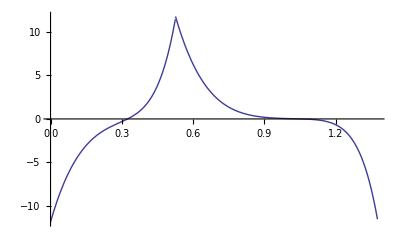

Piecewise[{{-11.8337+95.3587 u-318.485 u^2+575.128 u^3-676.103 u^4+720.038 u^5-758.56 u^6+1553.46 u^7-141.081 u^8, 0.≤u<0.525731}, {312.938-1592.63 u+3558.3 u^2-4454.28 u^3+2977.97 u^4-236.28 u^5-1297.8 u^6+960.089 u^7-228.275 u^8, 0.525731≤u<1.37638}, {0., True}}]

{a[0]→0.0182022,b[0]→-0.0181806,a[1]→-0.0771126,b[1]→0.124383,a[2]→0.1354,b[2]→-0.351599,a[3]→-0.128545,b[3]→0.532936,a[4]→0.0794455,b[4]→-0.514182,a[5]→-0.0444811,b[5]→0.421331,a[6]→0.0246362,b[6]→-0.27322,a[7]→-0.0265244,b[7]→0,a[8]→0.00126643,b[8]→0.0962653}

```mathematica
l=2;k=1;
λ/.λSol[n][[l]]/.σSol//N
1/σ^8/.σSol//N
f[norm_,u_]:=Poly[norm,n,u]/.Flatten[Table[{vector[n][[i]]->  ρ[n][[l,k,i]]},{i,Length[vector[n]]}]]/.A2Sol/.αβSol/.ϕSol/.σSol
f[1,u]//N
Integrate[f[1,u]//N,{u,0,A2/.A2Sol}]//N//Chop
halfnorm=2*Integrate[f[1,u]//N,{u,α/.αSol,A2/.A2Sol}]//N//Chop
Plot[f[halfnorm,u]//N,{u,0,A2/.A2Sol},PlotRange->Full,ImageSize->Scaled[0.5]]
f[halfnorm,u]//N
Flatten[Table[{vector[n][[i]]->  ρ[n][[l,k,i]]},{i,Length[vector[n]]}]]
```

```mathematica
ψ[9,2,u_]:=Poly[-0.0015381595546090157,8,u]/.{a[0]->0.018202152464971002,b[0]->-0.01818056032015674,a[1]->-0.07711261759655155,b[1]->0.12438334542638313,a[2]->0.1353996080858976,b[2]->-0.3515986279861222,a[3]->-0.12854544671913143,b[3]->0.5329363148004024,a[4]->0.0794454551714619,b[4]->-0.5141817868765266,a[5]->-0.04448109516760621,b[5]->0.42133098085484133,a[6]->0.024636193717006306,b[6]->-0.27321957508873357,a[7]->-0.026524429988925416,b[7]->0,a[8]->0.0012664288404439158,b[8]->0.09626525252716064}/.A2Sol/.αβSol/.ϕSol/.σSol//N
𝕍[9]:={1/σ^8/.σSol//N,2}
ψ[9,2,u]
```

Piecewise[{{-11.8337+95.3587 u-318.485 u^2+575.128 u^3-676.103 u^4+720.038 u^5-758.56 u^6+1553.46 u^7-141.081 u^8, 0.≤u<0.525731}, {312.938-1592.63 u+3558.3 u^2-4454.28 u^3+2977.97 u^4-236.28 u^5-1297.8 u^6+960.089 u^7-228.275 u^8, 0.525731≤u<1.37638}, {0., True}}]

0.000066107

0.000066107

Piecewise[{{0.00458417-0.0485012 u+0.228066 u^2-0.625585 u^3+1.10313 u^4-1.29681 u^5+1.01632 u^6-0.51204 u^7+0.150485 u^8, 0.≤u<0.525731}, {-0.343873+2.23002 u-6.39371 u^2+10.6001 u^3-11.1308 u^4+7.59163 u^5-3.28889 u^6+0.828499 u^7-0.0930048 u^8, 0.525731≤u<1.37638}, {0., True}}]

0

-0.000786196

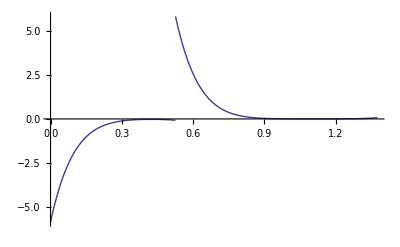

Piecewise[{{-5.83083+61.691 u-290.088 u^2+795.712 u^3-1403.12 u^4+1649.47 u^5-1292.71 u^6+651.289 u^7-191.409 u^8, 0.≤u<0.525731}, {437.389-2836.47 u+8132.46 u^2-13482.8 u^3+14157.7 u^4-9656.16 u^5+4183.3 u^6-1053.81 u^7+118.297 u^8, 0.525731≤u<1.37638}, {0., True}}]

{a[0]→0.00458417,b[0]→-0.00458338,a[1]→-0.0254986,b[1]→0.0412389,a[2]→0.0630359,b[2]→-0.164834,a[3]→-0.0909028,b[3]→0.383875,a[4]→0.0842715,b[4]→-0.572909,a[5]→-0.0520827,b[5]→0.565311,a[6]→0.0214592,b[6]→-0.363611,a[7]→-0.00568395,b[7]→0.140953,a[8]→0.000878218,b[8]→-0.0254986}

```mathematica
l=1;k=1;
λ/.λSol[n][[l]]/.σSol//N
1/σ^10/.σSol//N
f[norm_,u_]:=Poly[norm,n,u]/.Flatten[Table[{vector[n][[i]]->  ρ[n][[l,k,i]]},{i,Length[vector[n]]}]]/.A2Sol/.αβSol/.ϕSol/.σSol
f[1,u]//N
Integrate[f[1,u]//N,{u,0,A2/.A2Sol}]//N//Chop
halfnorm=2*Integrate[f[1,u]//N,{u,α/.αSol,A2/.A2Sol}]//N//Chop
Plot[f[halfnorm,u]//N,{u,0,A2/.A2Sol},PlotRange->Full,ImageSize->Scaled[0.5]]
f[halfnorm,u]//N
Flatten[Table[{vector[n][[i]]->  ρ[n][[l,k,i]]},{i,Length[vector[n]]}]]
```

```mathematica
ψ[11,1,u_]:=Poly[-0.0007861955567533011,8,u]/.{a[0]->0.004584172424178626,b[0]->-0.004583379040211593,a[1]->-0.025498569315889758,b[1]->0.04123885786187845,a[2]->0.06303593000685731,b[2]->-0.16483444162450947,a[3]->-0.0909028102656259,b[3]->0.3838746010297522,a[4]->0.0842715396255588,b[4]->-0.572909433501669,a[5]->-0.05208267577287891,b[5]->0.5653106735139498,a[6]->0.02145924256845337,b[6]->-0.36361124106250053,a[7]->-0.005683946262913632,b[7]->0.1409526245202485,a[8]->0.0008782179951774133,b[8]->-0.025498569315887176}/.A2Sol/.αβSol/.ϕSol/.σSol//N
𝕍[11]:={1/σ^10/.σSol//N,1}
ψ[11,1,u]
```

Piecewise[{{-5.83083+61.691 u-290.088 u^2+795.712 u^3-1403.12 u^4+1649.47 u^5-1292.71 u^6+651.289 u^7-191.409 u^8, 0.≤u<0.525731}, {437.389-2836.47 u+8132.46 u^2-13482.8 u^3+14157.7 u^4-9656.16 u^5+4183.3 u^6-1053.81 u^7+118.297 u^8, 0.525731≤u<1.37638}, {0., True}}]

#### order 9

```mathematica
n=9;
Subscript[LPoly, A][n]=Collect[(Subscript[Poly, A][n,u/σ]+Subscript[Poly, B][n,u/σ+α])/σ,u,Simplify]
Subscript[LPoly, B][n]=Collect[(Subscript[Poly, A][n,u/σ]+Subscript[Poly, B][n,u/σ+α]+Subscript[Poly, B][n,u/σ+β])/σ,u,Simplify]
```

(a[0]+b[0])/σ+(u (β a[1]+α b[1]))/(α β σ^2)+(u^2 (a[2]/α^2+b[2]/β^2))/σ^3+(u^3 (a[3]/α^3+b[3]/β^3))/σ^4+(u^4 (a[4]/α^4+b[4]/β^4))/σ^5+(u^5 (a[5]/α^5+b[5]/β^5))/σ^6+(u^6 (a[6]/α^6+b[6]/β^6))/σ^7+(u^7 (a[7]/α^7+b[7]/β^7))/σ^8+(u^8 (a[8]/α^8+b[8]/β^8))/σ^9+(u^9 (a[9]/α^9+b[9]/β^9))/σ^10

(u^9 (a[9]/α^9+(2 b[9])/β^9))/σ^10+(u^8 (β^9 a[8]-9 α^9 b[9]+α^8 β (2 b[8]+9 b[9])))/(α^8 β^9 σ^9)+(u^7 (β^9 a[7]+36 α^9 b[9]-8 α^8 β (b[8]+9 b[9])+2 α^7 β^2 (b[7]+4 b[8]+18 b[9])))/(α^7 β^9 σ^8)+1/(α^3 β^9 σ^4)u^3 (β^9 a[3]+84 α^9 b[9]-56 α^8 β (b[8]+9 b[9])+35 α^7 β^2 (b[7]+8 b[8]+36 b[9])+α^3 β^6 (2 b[3]+4 b[4]+10 b[5]+20 b[6]+35 b[7]+56 b[8]+84 b[9])+10 α^5 β^4 (b[5]+6 b[6]+21 b[7]+56 b[8]+126 b[9])-4 α^4 β^5 (b[4]+5 b[5]+15 b[6]+35 b[7]+70 b[8]+126 b[9])-20 α^6 β^3 (b[6]+7 (b[7]+4 b[8]+12 b[9])))+1/(α^5 β^9 σ^6)u^5 (β^9 a[5]+126 α^9 b[9]-56 α^8 β (b[8]+9 b[9])+21 α^7 β^2 (b[7]+8 b[8]+36 b[9])+α^5 β^4 (2 b[5]+6 b[6]+21 b[7]+56 b[8]+126 b[9])-6 α^6 β^3 (b[6]+7 (b[7]+4 b[8]+12 b[9])))+1/(α β^9 σ^2)u (β^9 a[1]+9 α^9 b[9]-8 α^8 β (b[8]+9 b[9])+α β^8 (2 b[1]+2 b[2]+3 b[3]+4 b[4]+5 b[5]+6 b[6]+7 b[7]+8 b[8]+9 b[9])+7 α^7 β^2 (b[7]+8 b[8]+36 b[9])-2 α^2 β^7 (b[2]+3 b[3]+6 b[4]+10 b[5]+15 b[6]+21 b[7]+28 b[8]+36 b[9])+3 α^3 β^6 (b[3]+4 b[4]+10 b[5]+20 b[6]+35 b[7]+56 b[8]+84 b[9])+5 α^5 β^4 (b[5]+6 b[6]+21 b[7]+56 b[8]+126 b[9])-4 α^4 β^5 (b[4]+5 b[5]+15 b[6]+35 b[7]+70 b[8]+126 b[9])-6 α^6 β^3 (b[6]+7 (b[7]+4 b[8]+12 b[9])))+1/(β^9 σ)(-α^9 b[9]+β^9 (a[0]+2 b[0]+b[1]+b[2]+b[3]+b[4]+b[5]+b[6]+b[7]+b[8]+b[9])+α^8 β (b[8]+9 b[9])-α β^8 (b[1]+2 b[2]+3 b[3]+4 b[4]+5 b[5]+6 b[6]+7 b[7]+8 b[8]+9 b[9])-α^7 β^2 (b[7]+8 b[8]+36 b[9])+α^2 β^7 (b[2]+3 b[3]+6 b[4]+10 b[5]+15 b[6]+21 b[7]+28 b[8]+36 b[9])-α^3 β^6 (b[3]+4 b[4]+10 b[5]+20 b[6]+35 b[7]+56 b[8]+84 b[9])-α^5 β^4 (b[5]+6 b[6]+21 b[7]+56 b[8]+126 b[9])+α^4 β^5 (b[4]+5 b[5]+15 b[6]+35 b[7]+70 b[8]+126 b[9])+α^6 β^3 (b[6]+7 (b[7]+4 b[8]+12 b[9])))+1/(α^2 β^9 σ^3)u^2 (β^9 a[2]-36 α^9 b[9]+28 α^8 β (b[8]+9 b[9])-21 α^7 β^2 (b[7]+8 b[8]+36 b[9])+α^2 β^7 (2 b[2]+3 b[3]+6 b[4]+10 b[5]+15 b[6]+21 b[7]+28 b[8]+36 b[9])-3 α^3 β^6 (b[3]+4 b[4]+10 b[5]+20 b[6]+35 b[7]+56 b[8]+84 b[9])-10 α^5 β^4 (b[5]+6 b[6]+21 b[7]+56 b[8]+126 b[9])+6 α^4 β^5 (b[4]+5 b[5]+15 b[6]+35 b[7]+70 b[8]+126 b[9])+15 α^6 β^3 (b[6]+7 (b[7]+4 b[8]+12 b[9])))+1/(α^4 β^9 σ^5)u^4 (β^9 a[4]-126 α^9 b[9]+70 α^8 β (b[8]+9 b[9])-35 α^7 β^2 (b[7]+8 b[8]+36 b[9])-5 α^5 β^4 (b[5]+6 b[6]+21 b[7]+56 b[8]+126 b[9])+α^4 β^5 (2 b[4]+5 b[5]+15 b[6]+35 b[7]+70 b[8]+126 b[9])+15 α^6 β^3 (b[6]+7 (b[7]+4 b[8]+12 b[9])))+(u^6 (β^9 a[6]-84 α^9 b[9]+28 α^8 β (b[8]+9 b[9])-7 α^7 β^2 (b[7]+8 b[8]+36 b[9])+α^6 β^3 (2 b[6]+7 (b[7]+4 b[8]+12 b[9]))))/(α^6 β^9 σ^7)

```mathematica
vector[n]=Table[{a[i],b[i]},{i,0,n}]//Flatten;
```

```mathematica
Subscript[lhs, A][n,i_]:=Coefficient[Subscript[LPoly, A][n],u,i]
Subscript[lhs, B][n,i_]:=Coefficient[Subscript[LPoly, B][n],u,i]
L[n]={};
Do[
L[n]=Append[L[n],Coefficient[Subscript[lhs, A][n,i],#]&/@vector[n]];
L[n]=Append[L[n],Coefficient[Subscript[lhs, B][n,i],#]&/@vector[n]],
{i,0,n}]
L[n]//Simplify//TraditionalForm
Subscript[rhs, A][n,i_]:=Coefficient[Subscript[Poly, A][n,u],u,i]
Subscript[rhs, B][n,i_]:=Coefficient[Subscript[Poly, B][n,u],u,i]
J[n]={};
Do[
J[n]=Append[J[n],Coefficient[Subscript[rhs, A][n,i],#]&/@vector[n]];
J[n]=Append[J[n],Coefficient[Subscript[rhs, B][n,i],#]&/@vector[n]],
{i,0,n}]
J[n]//TraditionalForm
```

(1/σ | 1/σ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/σ | 2/σ | 0 | (β-α)/(β σ) | 0 | (α-β)^2/(β^2 σ) | 0 | -(α-β)^3/(β^3 σ) | 0 | (α-β)^4/(β^4 σ) | 0 | -(α-β)^5/(β^5 σ) | 0 | (α-β)^6/(β^6 σ) | 0 | -(α-β)^7/(β^7 σ) | 0 | (α-β)^8/(β^8 σ) | 0 | -(α-β)^9/(β^9 σ)
0 | 0 | 1/(α σ^2) | 1/(β σ^2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/(α σ^2) | 2/(β σ^2) | 0 | -(2 (α-β))/(β^2 σ^2) | 0 | (3 (α-β)^2)/(β^3 σ^2) | 0 | -(4 (α-β)^3)/(β^4 σ^2) | 0 | (5 (α-β)^4)/(β^5 σ^2) | 0 | -(6 (α-β)^5)/(β^6 σ^2) | 0 | (7 (α-β)^6)/(β^7 σ^2) | 0 | -(8 (α-β)^7)/(β^8 σ^2) | 0 | (9 (α-β)^8)/(β^9 σ^2)
0 | 0 | 0 | 0 | 1/(α^2 σ^3) | 1/(β^2 σ^3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/(α^2 σ^3) | 2/(β^2 σ^3) | 0 | -(3 (α-β))/(β^3 σ^3) | 0 | (6 (α-β)^2)/(β^4 σ^3) | 0 | -(10 (α-β)^3)/(β^5 σ^3) | 0 | (15 (α-β)^4)/(β^6 σ^3) | 0 | -(21 (α-β)^5)/(β^7 σ^3) | 0 | (28 (α-β)^6)/(β^8 σ^3) | 0 | -(36 (α-β)^7)/(β^9 σ^3)
0 | 0 | 0 | 0 | 0 | 0 | 1/(α^3 σ^4) | 1/(β^3 σ^4) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/(α^3 σ^4) | 2/(β^3 σ^4) | 0 | -(4 (α-β))/(β^4 σ^4) | 0 | (10 (α-β)^2)/(β^5 σ^4) | 0 | -(20 (α-β)^3)/(β^6 σ^4) | 0 | (35 (α-β)^4)/(β^7 σ^4) | 0 | -(56 (α-β)^5)/(β^8 σ^4) | 0 | (84 (α-β)^6)/(β^9 σ^4)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(α^4 σ^5) | 1/(β^4 σ^5) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(α^4 σ^5) | 2/(β^4 σ^5) | 0 | -(5 (α-β))/(β^5 σ^5) | 0 | (15 (α-β)^2)/(β^6 σ^5) | 0 | -(35 (α-β)^3)/(β^7 σ^5) | 0 | (70 (α-β)^4)/(β^8 σ^5) | 0 | -(126 (α-β)^5)/(β^9 σ^5)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(α^5 σ^6) | 1/(β^5 σ^6) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(α^5 σ^6) | 2/(β^5 σ^6) | 0 | -(6 (α-β))/(β^6 σ^6) | 0 | (21 (α-β)^2)/(β^7 σ^6) | 0 | -(56 (α-β)^3)/(β^8 σ^6) | 0 | (126 (α-β)^4)/(β^9 σ^6)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(α^6 σ^7) | 1/(β^6 σ^7) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(α^6 σ^7) | 2/(β^6 σ^7) | 0 | -(7 (α-β))/(β^7 σ^7) | 0 | (28 (α-β)^2)/(β^8 σ^7) | 0 | -(84 (α-β)^3)/(β^9 σ^7)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(α^7 σ^8) | 1/(β^7 σ^8) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(α^7 σ^8) | 2/(β^7 σ^8) | 0 | -(8 (α-β))/(β^8 σ^8) | 0 | (36 (α-β)^2)/(β^9 σ^8)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(α^8 σ^9) | 1/(β^8 σ^9) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(α^8 σ^9) | 2/(β^8 σ^9) | 0 | -(9 (α-β))/(β^9 σ^9)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(α^9 σ^10) | 1/(β^9 σ^10)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(α^9 σ^10) | 2/(β^9 σ^10))

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | -α/β | 0 | α^2/β^2 | 0 | -α^3/β^3 | 0 | α^4/β^4 | 0 | -α^5/β^5 | 0 | α^6/β^6 | 0 | -α^7/β^7 | 0 | α^8/β^8 | 0 | -α^9/β^9
0 | 0 | 1/α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/β | 0 | -(2 α)/β^2 | 0 | (3 α^2)/β^3 | 0 | -(4 α^3)/β^4 | 0 | (5 α^4)/β^5 | 0 | -(6 α^5)/β^6 | 0 | (7 α^6)/β^7 | 0 | -(8 α^7)/β^8 | 0 | (9 α^8)/β^9
0 | 0 | 0 | 0 | 1/α^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/β^2 | 0 | -(3 α)/β^3 | 0 | (6 α^2)/β^4 | 0 | -(10 α^3)/β^5 | 0 | (15 α^4)/β^6 | 0 | -(21 α^5)/β^7 | 0 | (28 α^6)/β^8 | 0 | -(36 α^7)/β^9
0 | 0 | 0 | 0 | 0 | 0 | 1/α^3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/β^3 | 0 | -(4 α)/β^4 | 0 | (10 α^2)/β^5 | 0 | -(20 α^3)/β^6 | 0 | (35 α^4)/β^7 | 0 | -(56 α^5)/β^8 | 0 | (84 α^6)/β^9
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/α^4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/β^4 | 0 | -(5 α)/β^5 | 0 | (15 α^2)/β^6 | 0 | -(35 α^3)/β^7 | 0 | (70 α^4)/β^8 | 0 | -(126 α^5)/β^9
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/α^5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/β^5 | 0 | -(6 α)/β^6 | 0 | (21 α^2)/β^7 | 0 | -(56 α^3)/β^8 | 0 | (126 α^4)/β^9
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/α^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/β^6 | 0 | -(7 α)/β^7 | 0 | (28 α^2)/β^8 | 0 | -(84 α^3)/β^9
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/α^7 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/β^7 | 0 | -(8 α)/β^8 | 0 | (36 α^2)/β^9
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/α^8 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/β^8 | 0 | -(9 α)/β^9
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/α^9 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/β^9)

```mathematica
determinant[n]=Det[L[n]-λ J[n]]//Simplify
```

1/(α^45 β^45 σ^110)(1-3 λ σ+λ^2 σ^2) (1-3 λ σ^2+λ^2 σ^4) (1-3 λ σ^3+λ^2 σ^6) (1-3 λ σ^4+λ^2 σ^8) (1-3 λ σ^5+λ^2 σ^10) (1-3 λ σ^6+λ^2 σ^12) (1-3 λ σ^7+λ^2 σ^14) (1-3 λ σ^8+λ^2 σ^16) (1-3 λ σ^9+λ^2 σ^18) (1-3 λ σ^10+λ^2 σ^20)

```mathematica
λSol[n]=Solve[determinant[n]==0,λ]
```

{{λ→(3-√5)/(2 σ^10)},{λ→(3+√5)/(2 σ^10)},{λ→(3-√5)/(2 σ^9)},{λ→(3+√5)/(2 σ^9)},{λ→(3-√5)/(2 σ^8)},{λ→(3+√5)/(2 σ^8)},{λ→(3-√5)/(2 σ^7)},{λ→(3+√5)/(2 σ^7)},{λ→(3-√5)/(2 σ^6)},{λ→(3+√5)/(2 σ^6)},{λ→(3-√5)/(2 σ^5)},{λ→(3+√5)/(2 σ^5)},{λ→(3-√5)/(2 σ^4)},{λ→(3+√5)/(2 σ^4)},{λ→(3-√5)/(2 σ^3)},{λ→(3+√5)/(2 σ^3)},{λ→(3-√5)/(2 σ^2)},{λ→(3+√5)/(2 σ^2)},{λ→(3-√5)/(2 σ)},{λ→(3+√5)/(2 σ)}}

```mathematica
λSol[n]/.σSol//Simplify
%//N
```

{{λ→1/2 (39603-17711 √5)},{λ→512/(3+√5)^9},{λ→1/2 (15127-6765 √5)},{λ→256/(3+√5)^8},{λ→2889-1292 √5},{λ→128/(3+√5)^7},{λ→1/2 (2207-987 √5)},{λ→64/(3+√5)^6},{λ→1/2 (843-377 √5)},{λ→32/(3+√5)^5},{λ→161-72 √5},{λ→16/(3+√5)^4},{λ→1/2 (123-55 √5)},{λ→9-4 √5},{λ→1/2 (47-21 √5)},{λ→4/(3+√5)^2},{λ→9-4 √5},{λ→2/(3+√5)},{λ→1/2 (7-3 √5)},{λ→1}}

{{λ→0.0000252506},{λ→0.00017307},{λ→0.000066107},{λ→0.000453104},{λ→0.00017307},{λ→0.00118624},{λ→0.000453104},{λ→0.00310562},{λ→0.00118624},{λ→0.00813062},{λ→0.00310562},{λ→0.0212862},{λ→0.00813062},{λ→0.0557281},{λ→0.0212862},{λ→0.145898},{λ→0.0557281},{λ→0.381966},{λ→0.145898},{λ→1.}}

```mathematica
LN[n]=(L[n]/.αβSol/.σSol)//N//Chop
JN[n]=(J[n]/.αβSol/.σSol)//N//Chop
```

{{0.381966,0.381966,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0.381966,0.763932,0,0.145898,0,0.0557281,0,0.0212862,0,0.00813062,0,0.00310562,0,0.00118624,0,0.000453104,0,0.00017307,0,0.000066107},{0,0,0.277515,0.171513,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0.277515,0.343027,0,0.131025,0,0.0750704,0,0.0382325,0,0.0182544,0,0.00836706,0,0.00372859,0,0.00162765,0,0.000699421},{0,0,0,0,0.201626,0.0770143,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0.201626,0.154029,0,0.0882506,0,0.0674174,0,0.0429186,0,0.0245902,0,0.0131497,0,0.00669696,0,0.00328887},{0,0,0,0,0,0,0.14649,0.0345816,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0.14649,0.0691632,0,0.052836,0,0.0504539,0,0.0385433,0,0.0257639,0,0.0157455,0,0.00902137},{0,0,0,0,0,0,0,0,0.106431,0.0155281,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0.106431,0.0310562,0,0.029656,0,0.0339828,0,0.0302873,0,0.0231374,0,0.0159079},{0,0,0,0,0,0,0,0,0,0,0.0773268,0.00697255,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0.0773268,0.0139451,0,0.0159797,0,0.0213629,0,0.0217598,0,0.0187008},{0,0,0,0,0,0,0,0,0,0,0,0,0.0561812,0.00313087,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0.0561812,0.00626174,0,0.0083712,0,0.0127901,0,0.0146561},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.040818,0.00140585,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.040818,0.0028117,0,0.00429589,0,0.00738398},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.029656,0.000631265,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.029656,0.00126253,0,0.0021701},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.0215464,0.000283456},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.0215464,0.000566912}}

{{1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1.,0,-0.618034,0,0.381966,0,-0.236068,0,0.145898,0,-0.0901699,0,0.0557281,0,-0.0344419,0,0.0212862,0,-0.0131556},{0,0,1.90211,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1.17557,0,-1.45309,0,1.34708,0,-1.11006,0,0.857567,0,-0.636007,0,0.458586,0,-0.323911,0,0.225211},{0,0,0,0,3.61803,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1.38197,0,-2.56231,0,3.16718,0,-3.26238,0,3.02439,0,-2.61685,0,2.1564,0,-1.71351},{0,0,0,0,0,0,6.88191,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1.6246,0,-4.01623,0,6.20541,0,-7.67031,0,8.2959,0,-8.20344,0,7.605},{0,0,0,0,0,0,0,0,13.0902,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1.90983,0,-5.9017,0,10.9424,0,-15.7797,0,19.5048,0,-21.6984},{0,0,0,0,0,0,0,0,0,0,24.899,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,2.24514,0,-8.32544,0,18.0089,0,-29.6803,0,41.2727},{0,0,0,0,0,0,0,0,0,0,0,0,47.3607,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,2.63932,0,-11.4183,0,28.2277,0,-52.337},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,90.0854,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3.10271,0,-15.3406,0,42.6646},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,171.353,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3.64745,0,-20.2882},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,325.932,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,4.28784}}

```mathematica
ρ[n]=Table[
NullSpace[(LN[n]-λ JN[n])/.λSol[n][[i]]/.σSol//N],
{i,Length[λSol[n]]}]//Chop
Length/@%
λSol[n]/.σSol//Simplify;
%//N
```

{{{0.00234316,-0.002343,-0.0144815,0.0234275,0.0402753,-0.105394,-0.0663773,0.280845,0.071791,-0.490534,-0.0532431,0.585674,0.0274217,-0.481588,-0.00968431,0.265509,0.00224446,-0.0900582,-0.000308257,0.0144815}},{{-0.000866482,0.000866089,0.00428412,-0.00692363,-0.0197888,0.051647,0.0569745,-0.239385,-0.0791811,0.531163,0.0391493,-0.409977,0.0201395,-0.308662,-0.0320187,0.574552,0.0426937,0,-0.00181195,-0.222855},{0.0103684,-0.0103637,-0.0512642,0.0828488,0.103426,-0.269932,-0.104774,0.440223,0.0559943,-0.375621,-0.0276851,0.289922,0.0314258,-0.481639,-0.0257418,0.461918,0.0302889,0,-0.00128548,-0.158104}},{{0.00458417,-0.00458338,-0.0254986,0.0412389,0.0630359,-0.164834,-0.0909028,0.383875,0.0842715,-0.572909,-0.0520827,0.565311,0.0214592,-0.363611,-0.00568395,0.140953,0.000878218,-0.0254986,0,0}},{{-0.00428174,0.00427666,0.0122988,-0.0198381,0.00605135,-0.0157138,-0.0478438,0.198356,0.0295691,-0.191375,0.0462529,-0.438114,-0.0684662,0.759301,0.101036,0,-0.00482403,-0.36669,0,0},{-0.0176942,0.0176732,0.0762677,-0.12302,-0.140103,0.363812,0.142432,-0.59051,-0.088028,0.569729,0.0352302,-0.333706,-0.00992325,0.110051,0.0045693,0,-0.000218165,-0.0165834,0,0}},{{-0.00871521,0.00871126,0.0430904,-0.069639,-0.0816457,0.213087,0.0651853,-0.273884,-0.0117096,0.0785506,0.00578956,-0.0606291,-0.0372191,0.57043,0.0378536,-0.679256,-0.0469221,0,0.00199141,0.244927},{-0.00568328,0.0056807,0.0280997,-0.0454123,-0.0665018,0.173563,0.0998731,-0.41963,-0.0962699,0.645798,0.0475985,-0.498458,0.00281314,-0.0431149,-0.0159669,0.286515,0.0232053,0,-0.000984847,-0.121128}},{{-0.02946,0.0293685,0.117252,-0.188175,-0.198486,0.508581,0.163561,-0.654245,-0.036116,0.211427,-0.0401421,0.275138,0.098141,0,-0.00535522,-0.251581,0,0,0,0},{0.0171284,-0.0170752,-0.0503211,0.0807592,0.0492091,-0.126089,-0.0405505,0.162202,0.0842068,-0.492955,-0.101669,0.69685,0.161704,0,-0.00882363,-0.414523,0,0,0,0}},{{-0.0149983,0.0149805,0.0668464,-0.107824,-0.133026,0.345434,0.150126,-0.622408,-0.092783,0.600504,0.0163894,-0.155243,0.0151815,-0.168366,-0.0318136,0,0.00151897,0.115461,0,0},{0.0103183,-0.0103061,-0.0387243,0.0624627,0.0443809,-0.115246,-0.00617609,0.0256054,0.00381703,-0.0247044,-0.0557843,0.528397,0.0674952,-0.748534,-0.0960052,0,0.00458384,0.348432,0,0}},{{0.0667844,-0.0662414,-0.215134,0.340685,0.265921,-0.657392,-0.1242,0.449359,-0.0236524,0.100193,0.148877,0,-0.00947769,-0.275179,0,0,0,0,0,0},{-0.0146195,0.0145007,0.0277148,-0.0438889,-0.0342574,0.0846888,0.101211,-0.366185,-0.154943,0.656347,0.2968,0,-0.0188946,-0.548594,0,0,0,0,0,0}},{{0.016731,-0.016679,-0.048741,0.0782234,0.0465376,-0.119244,-0.0383491,0.153397,0.0837139,-0.49007,-0.102199,0.700484,0.163008,0,-0.00889479,-0.417866,0,0,0,0},{0.0296875,-0.0295953,-0.117917,0.189243,0.199129,-0.51023,-0.164091,0.656366,0.0372442,-0.218031,0.0387724,-0.26575,-0.0959593,0,0.00523617,0.245989,0,0,0,0}},{{0.120451,-0.117887,-0.29777,0.454952,0.216912,-0.485029,0.032455,-0.0849682,-0.365482,0,0.0279204,0.501011,0,0,0,0,0,0,0,0},{-0.0617442,0.0604299,0.15264,-0.233213,-0.198887,0.444725,0.20016,-0.524025,-0.354641,0,0.0270922,0.486149,0,0,0,0,0,0,0,0}},{{0.0649106,-0.0643829,-0.211106,0.334305,0.260941,-0.645082,-0.113047,0.409008,-0.0395759,0.167646,0.178823,0,-0.011384,-0.330529,0,0,0,0,0,0},{-0.0214592,0.0212847,0.0498518,-0.0789449,-0.0616202,0.152334,0.113533,-0.410764,-0.151659,0.642437,0.279781,0,-0.0178111,-0.517136,0,0,0,0,0,0}},{{-0.137166,0.129522,0.290062,-0.400856,-0.289721,0.468779,0.441812,0,-0.0421893,-0.467886,0,0,0,0,0,0,0,0,0,0},{0.213731,-0.20182,-0.356769,0.493043,0.0984015,-0.159217,0.488376,0,-0.0466357,-0.517198,0,0,0,0,0,0,0,0,0,0}},{{0.123369,-0.120743,-0.304985,0.465975,0.290735,-0.650103,-0.136267,0.356752,0.0494336,0,-0.00377639,-0.0677646,0,0,0,0,0,0,0,0},{0.0556845,-0.0544992,-0.13766,0.210325,0.0456064,-0.101979,0.150161,-0.393128,-0.506857,0,0.0387204,0.69481,0,0,0,0,0,0,0,0}},{{-0.452718,0.386667,0.566701,-0.566701,-0.0426618,0,0.00543178,0.03723,0,0,0,0,0,0,0,0,0,0,0,0},{-0.0902603,0.0770915,-0.0125286,0.0125286,0.744579,0,-0.0948013,-0.649778,0,0,0,0,0,0,0,0,0,0,0,0}},{{-0.0695786,0.0657011,0.174639,-0.241345,-0.248946,0.402803,0.564052,0,-0.0538622,-0.597341,0,0,0,0,0,0,0,0,0,0},{0.244242,-0.230631,-0.425349,0.587818,0.177897,-0.287844,0.339932,0,-0.0324606,-0.359993,0,0,0,0,0,0,0,0,0,0}},{{0.297803,-0.184052,-0.720342,0,0.137573,0.582769,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0.796819,-0.492461,0.26922,0,-0.0514165,-0.217804,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{{-0.459883,0.392787,0.540528,-0.540528,0.167511,0,-0.0213278,-0.146183,0,0,0,0,0,0,0,0,0,0,0,0},{0.0401011,-0.0342504,-0.170692,0.170692,0.726745,0,-0.0925306,-0.634214,0,0,0,0,0,0,0,0,0,0,0,0}},{{0.682646,0,-0.260748,-0.682646,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{{-0.464412,0.287023,-0.644288,0,0.123048,0.52124,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0.712691,-0.440467,-0.419839,0,0.0801821,0.339657,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{{0.525731,0.850651,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}}

{1,2,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,2,1}

{{λ→0.0000252506},{λ→0.00017307},{λ→0.000066107},{λ→0.000453104},{λ→0.00017307},{λ→0.00118624},{λ→0.000453104},{λ→0.00310562},{λ→0.00118624},{λ→0.00813062},{λ→0.00310562},{λ→0.0212862},{λ→0.00813062},{λ→0.0557281},{λ→0.0212862},{λ→0.145898},{λ→0.0557281},{λ→0.381966},{λ→0.145898},{λ→1.}}

0.00017307

0.00017307

Piecewise[{{-0.000866482+0.00814888 u-0.0715967 u^2+0.392093 u^3-1.03649 u^4+0.974778 u^5+0.953819 u^6-2.88442 u^7+7.31567 u^8-0.590572 u^9, 0.≤u<0.525731}, {0.161789-0.93726 u+1.64938 u^2+0.372899 u^3-4.1742 u^4+2.79852 u^5+4.28846 u^6-7.72536 u^7+4.52133 u^8-0.955566 u^9, 0.525731≤u<1.37638}, {0., True}}]

0

-0.00320575

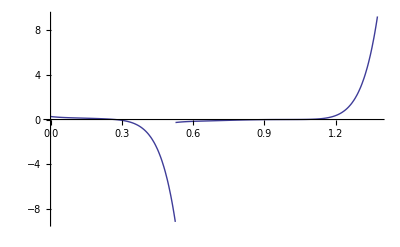

Piecewise[{{0.27029-2.54196 u+22.3339 u^2-122.309 u^3+323.324 u^4-304.072 u^5-297.534 u^6+899.765 u^7-2282.05 u^8+184.223 u^9, 0.≤u<0.525731}, {-50.4684+292.369 u-514.506 u^2-116.322 u^3+1302.1 u^4-872.969 u^5-1337.74 u^6+2409.85 u^7-1410.38 u^8+298.079 u^9, 0.525731≤u<1.37638}, {0., True}}]

{a[0]→-0.000866482,b[0]→0.000866089,a[1]→0.00428412,b[1]→-0.00692363,a[2]→-0.0197888,b[2]→0.051647,a[3]→0.0569745,b[3]→-0.239385,a[4]→-0.0791811,b[4]→0.531163,a[5]→0.0391493,b[5]→-0.409977,a[6]→0.0201395,b[6]→-0.308662,a[7]→-0.0320187,b[7]→0.574552,a[8]→0.0426937,b[8]→0,a[9]→-0.00181195,b[9]→-0.222855}

```mathematica
l=2;k=1;
λ/.λSol[n][[l]]/.σSol//N
1/σ^9/.σSol//N
f[norm_,u_]:=Poly[norm,n,u]/.Flatten[Table[{vector[n][[i]]->  ρ[n][[l,k,i]]},{i,Length[vector[n]]}]]/.A2Sol/.αβSol/.ϕSol/.σSol
f[1,u]//N
Integrate[f[1,u]//N,{u,0,A2/.A2Sol}]//N//Chop
halfnorm=2*Integrate[f[1,u]//N,{u,α/.αSol,A2/.A2Sol}]//N//Chop
Plot[f[halfnorm,u]//N,{u,0,A2/.A2Sol},PlotRange->Full,ImageSize->Scaled[0.5]]
f[halfnorm,u]//N
Flatten[Table[{vector[n][[i]]->  ρ[n][[l,k,i]]},{i,Length[vector[n]]}]]
```

```mathematica
ψ[10,2,u_]:=Poly[-0.0032057463817178554,9,u]/.{a[0]->-0.0008664818021422533,b[0]->0.0008660891958984899,a[1]->0.004284121634860971,b[1]->-0.006923631565220389,a[2]->-0.019788849719772593,b[2]->0.0516469855719417,a[3]->0.05697446715544354,b[3]->-0.23938540958711396,a[4]->-0.07918113359751924,b[4]->0.5311631917786371,a[5]->0.039149305464810304,b[5]->-0.409976849371301,a[6]->0.020139461841470488,b[6]->-0.3086621837883013,a[7]->-0.032018711922278835,b[7]->0.5745524729413032,a[8]->0.042693694197778055,b[8]->0,a[9]->-0.0018119488975842368,b[9]->-0.22285498213715502}/.A2Sol/.αβSol/.ϕSol/.σSol//N
𝕍[10]:={1/σ^9/.σSol//N,2}
ψ[10,2,u]
```

Piecewise[{{0.27029-2.54196 u+22.3339 u^2-122.309 u^3+323.324 u^4-304.072 u^5-297.534 u^6+899.765 u^7-2282.05 u^8+184.223 u^9, 0.≤u<0.525731}, {-50.4684+292.369 u-514.506 u^2-116.322 u^3+1302.1 u^4-872.969 u^5-1337.74 u^6+2409.85 u^7-1410.38 u^8+298.079 u^9, 0.525731≤u<1.37638}, {0., True}}]

0.0000252506

0.0000252506

Piecewise[{{0.00234316-0.0275454 u+0.145717 u^2-0.456802 u^3+0.939756 u^4-1.3257 u^5+1.29871 u^6-0.872415 u^7+0.384594 u^8-0.100471 u^9, 0.≤u<0.525731}, {-0.285846+2.06627 u-6.69989 u^2+12.8062 u^3-15.9235 u^4+13.3765 u^5-7.60278 u^6+2.82319 u^7-0.622287 u^8+0.0620943 u^9, 0.525731≤u<1.37638}, {0., True}}]

0

-0.000360571

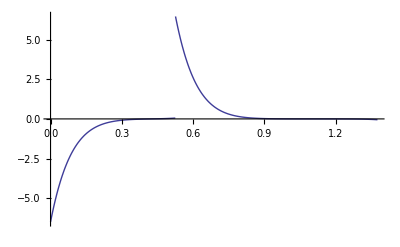

Piecewise[{{-6.49846+76.3939 u-404.129 u^2+1266.89 u^3-2606.3 u^4+3676.67 u^5-3601.82 u^6+2419.54 u^7-1066.63 u^8+278.643 u^9, 0.≤u<0.525731}, {792.759-5730.55 u+18581.3 u^2-35516.4 u^3+44161.8 u^4-37098.2 u^5+21085.4 u^6-7829.79 u^7+1725.84 u^8-172.211 u^9, 0.525731≤u<1.37638}, {0., True}}]

{a[0]→0.00234316,b[0]→-0.002343,a[1]→-0.0144815,b[1]→0.0234275,a[2]→0.0402753,b[2]→-0.105394,a[3]→-0.0663773,b[3]→0.280845,a[4]→0.071791,b[4]→-0.490534,a[5]→-0.0532431,b[5]→0.585674,a[6]→0.0274217,b[6]→-0.481588,a[7]→-0.00968431,b[7]→0.265509,a[8]→0.00224446,b[8]→-0.0900582,a[9]→-0.000308257,b[9]→0.0144815}

```mathematica
l=1;k=1;
λ/.λSol[n][[l]]/.σSol//N
1/σ^11/.σSol//N
f[norm_,u_]:=Poly[norm,n,u]/.Flatten[Table[{vector[n][[i]]->  ρ[n][[l,k,i]]},{i,Length[vector[n]]}]]/.A2Sol/.αβSol/.ϕSol/.σSol
f[1,u]//N
Integrate[f[1,u]//N,{u,0,A2/.A2Sol}]//N//Chop
halfnorm=2*Integrate[f[1,u]//N,{u,α/.αSol,A2/.A2Sol}]//N//Chop
Plot[f[halfnorm,u]//N,{u,0,A2/.A2Sol},PlotRange->Full,ImageSize->Scaled[0.5]]
f[halfnorm,u]//N
Flatten[Table[{vector[n][[i]]->  ρ[n][[l,k,i]]},{i,Length[vector[n]]}]]
```

```mathematica
ψ[12,1,u_]:=Poly[-0.00036057101805579987,9,u]/.{a[0]->0.002343155112623322,b[0]->-0.0023430002137588527,a[1]->-0.014481495005133356,b[1]->0.02342749582129763,a[2]->0.04027525254486573,b[2]->-0.10539420390042457,a[3]->-0.06637726660856136,b[3]->0.2808450678333778,a[4]->0.0717909619777069,b[4]->-0.4905344142729256,a[5]->-0.053243105504729,b[5]->0.5856741605520196,a[6]->0.027421707390432617,b[6]->-0.48158841345676945,a[7]->-0.009684312683909352,b[7]->0.2655090664342458,a[8]->0.0022444628986265786,b[8]->-0.09005820250128202,a[9]->-0.00030825652396437864,b[9]->0.014481495005126561}/.A2Sol/.αβSol/.ϕSol/.σSol//N
𝕍[12]:={1/σ^11/.σSol//N,1}
ψ[12,1,u]
```

Piecewise[{{-6.49846+76.3939 u-404.129 u^2+1266.89 u^3-2606.3 u^4+3676.67 u^5-3601.82 u^6+2419.54 u^7-1066.63 u^8+278.643 u^9, 0.≤u<0.525731}, {792.759-5730.55 u+18581.3 u^2-35516.4 u^3+44161.8 u^4-37098.2 u^5+21085.4 u^6-7829.79 u^7+1725.84 u^8-172.211 u^9, 0.525731≤u<1.37638}, {0., True}}]

#### order 10

```mathematica
n=10;
Subscript[LPoly, A][n]=Collect[(Subscript[Poly, A][n,u/σ]+Subscript[Poly, B][n,u/σ+α])/σ,u,Simplify]
Subscript[LPoly, B][n]=Collect[(Subscript[Poly, A][n,u/σ]+Subscript[Poly, B][n,u/σ+α]+Subscript[Poly, B][n,u/σ+β])/σ,u,Simplify]
```

(a[0]+b[0])/σ+(u (β a[1]+α b[1]))/(α β σ^2)+(u^2 (a[2]/α^2+b[2]/β^2))/σ^3+(u^3 (a[3]/α^3+b[3]/β^3))/σ^4+(u^4 (a[4]/α^4+b[4]/β^4))/σ^5+(u^5 (a[5]/α^5+b[5]/β^5))/σ^6+(u^6 (a[6]/α^6+b[6]/β^6))/σ^7+(u^7 (a[7]/α^7+b[7]/β^7))/σ^8+(u^8 (a[8]/α^8+b[8]/β^8))/σ^9+(u^9 (a[9]/α^9+b[9]/β^9))/σ^10+(u^10 (a[10]/α^10+b[10]/β^10))/σ^11

(u^10 (a[10]/α^10+(2 b[10])/β^10))/σ^11+(u^9 (β^10 a[9]-10 α^10 b[10]+2 α^9 β (b[9]+5 b[10])))/(α^9 β^10 σ^10)+1/(α^7 β^10 σ^8)u^7 (β^10 a[7]-120 α^10 b[10]+36 α^9 β (b[9]+10 b[10])+2 α^7 β^3 (b[7]+4 b[8]+18 b[9]+60 b[10])-8 α^8 β^2 (b[8]+9 (b[9]+5 b[10])))+(u^8 (β^10 a[8]+45 α^10 b[10]-9 α^9 β (b[9]+10 b[10])+α^8 β^2 (2 b[8]+9 (b[9]+5 b[10]))))/(α^8 β^10 σ^9)+1/(α^6 β^10 σ^7)u^6 (β^10 a[6]+210 α^10 b[10]-84 α^9 β (b[9]+10 b[10])-7 α^7 β^3 (b[7]+8 b[8]+36 b[9]+120 b[10])+28 α^8 β^2 (b[8]+9 (b[9]+5 b[10]))+α^6 β^4 (2 b[6]+7 (b[7]+4 b[8]+12 b[9]+30 b[10])))+1/(α^2 β^10 σ^3)u^2 (β^10 a[2]+45 α^10 b[10]-36 α^9 β (b[9]+10 b[10])+α^2 β^8 (2 b[2]+3 b[3]+6 b[4]+10 b[5]+15 b[6]+21 b[7]+28 b[8]+36 b[9]+45 b[10])-21 α^7 β^3 (b[7]+8 b[8]+36 b[9]+120 b[10])-3 α^3 β^7 (b[3]+4 b[4]+10 b[5]+20 b[6]+35 b[7]+56 b[8]+84 b[9]+120 b[10])+6 α^4 β^6 (b[4]+5 b[5]+15 b[6]+35 b[7]+70 b[8]+126 b[9]+210 b[10])+28 α^8 β^2 (b[8]+9 (b[9]+5 b[10]))+15 α^6 β^4 (b[6]+7 (b[7]+4 b[8]+12 b[9]+30 b[10]))-10 α^5 β^5 (b[5]+6 b[6]+7 (3 b[7]+8 b[8]+18 b[9]+36 b[10])))+1/(α^4 β^10 σ^5)u^4 (β^10 a[4]+210 α^10 b[10]-126 α^9 β (b[9]+10 b[10])-35 α^7 β^3 (b[7]+8 b[8]+36 b[9]+120 b[10])+α^4 β^6 (2 b[4]+5 b[5]+15 b[6]+35 b[7]+70 b[8]+126 b[9]+210 b[10])+70 α^8 β^2 (b[8]+9 (b[9]+5 b[10]))+15 α^6 β^4 (b[6]+7 (b[7]+4 b[8]+12 b[9]+30 b[10]))-5 α^5 β^5 (b[5]+6 b[6]+7 (3 b[7]+8 b[8]+18 b[9]+36 b[10])))+1/(β^10 σ)(α^10 b[10]+β^10 (a[0]+2 b[0]+b[1]+b[2]+b[3]+b[4]+b[5]+b[6]+b[7]+b[8]+b[9]+b[10])-α^9 β (b[9]+10 b[10])-α β^9 (b[1]+2 b[2]+3 b[3]+4 b[4]+5 b[5]+6 b[6]+7 b[7]+8 b[8]+9 b[9]+10 b[10])+α^2 β^8 (b[2]+3 b[3]+6 b[4]+10 b[5]+15 b[6]+21 b[7]+28 b[8]+36 b[9]+45 b[10])-α^7 β^3 (b[7]+8 b[8]+36 b[9]+120 b[10])-α^3 β^7 (b[3]+4 b[4]+10 b[5]+20 b[6]+35 b[7]+56 b[8]+84 b[9]+120 b[10])+α^4 β^6 (b[4]+5 b[5]+15 b[6]+35 b[7]+70 b[8]+126 b[9]+210 b[10])+α^8 β^2 (b[8]+9 (b[9]+5 b[10]))+α^6 β^4 (b[6]+7 (b[7]+4 b[8]+12 b[9]+30 b[10]))-α^5 β^5 (b[5]+6 b[6]+7 (3 b[7]+8 b[8]+18 b[9]+36 b[10])))+1/(α β^10 σ^2)u (β^10 a[1]-10 α^10 b[10]+9 α^9 β (b[9]+10 b[10])+α β^9 (2 b[1]+2 b[2]+3 b[3]+4 b[4]+5 b[5]+6 b[6]+7 b[7]+8 b[8]+9 b[9]+10 b[10])-2 α^2 β^8 (b[2]+3 b[3]+6 b[4]+10 b[5]+15 b[6]+21 b[7]+28 b[8]+36 b[9]+45 b[10])+7 α^7 β^3 (b[7]+8 b[8]+36 b[9]+120 b[10])+3 α^3 β^7 (b[3]+4 b[4]+10 b[5]+20 b[6]+35 b[7]+56 b[8]+84 b[9]+120 b[10])-4 α^4 β^6 (b[4]+5 b[5]+15 b[6]+35 b[7]+70 b[8]+126 b[9]+210 b[10])-8 α^8 β^2 (b[8]+9 (b[9]+5 b[10]))-6 α^6 β^4 (b[6]+7 (b[7]+4 b[8]+12 b[9]+30 b[10]))+5 α^5 β^5 (b[5]+6 b[6]+7 (3 b[7]+8 b[8]+18 b[9]+36 b[10])))+1/(α^3 β^10 σ^4)u^3 (β^10 a[3]-120 α^10 b[10]+84 α^9 β (b[9]+10 b[10])+35 α^7 β^3 (b[7]+8 b[8]+36 b[9]+120 b[10])+α^3 β^7 (2 b[3]+4 b[4]+10 b[5]+20 b[6]+35 b[7]+56 b[8]+84 b[9]+120 b[10])-4 α^4 β^6 (b[4]+5 b[5]+15 b[6]+35 b[7]+70 b[8]+126 b[9]+210 b[10])-56 α^8 β^2 (b[8]+9 (b[9]+5 b[10]))-20 α^6 β^4 (b[6]+7 (b[7]+4 b[8]+12 b[9]+30 b[10]))+10 α^5 β^5 (b[5]+6 b[6]+7 (3 b[7]+8 b[8]+18 b[9]+36 b[10])))+1/(α^5 β^10 σ^6)u^5 (β^10 a[5]-252 α^10 b[10]+126 α^9 β (b[9]+10 b[10])+21 α^7 β^3 (b[7]+8 b[8]+36 b[9]+120 b[10])-56 α^8 β^2 (b[8]+9 (b[9]+5 b[10]))-6 α^6 β^4 (b[6]+7 (b[7]+4 b[8]+12 b[9]+30 b[10]))+α^5 β^5 (2 b[5]+6 b[6]+7 (3 b[7]+8 b[8]+18 b[9]+36 b[10])))

```mathematica
vector[n]=Table[{a[i],b[i]},{i,0,n}]//Flatten;
```

```mathematica
Subscript[lhs, A][n,i_]:=Coefficient[Subscript[LPoly, A][n],u,i]
Subscript[lhs, B][n,i_]:=Coefficient[Subscript[LPoly, B][n],u,i]
L[n]={};
Do[
L[n]=Append[L[n],Coefficient[Subscript[lhs, A][n,i],#]&/@vector[n]];
L[n]=Append[L[n],Coefficient[Subscript[lhs, B][n,i],#]&/@vector[n]],
{i,0,n}]
L[n]//Simplify//TraditionalForm
Subscript[rhs, A][n,i_]:=Coefficient[Subscript[Poly, A][n,u],u,i]
Subscript[rhs, B][n,i_]:=Coefficient[Subscript[Poly, B][n,u],u,i]
J[n]={};
Do[
J[n]=Append[J[n],Coefficient[Subscript[rhs, A][n,i],#]&/@vector[n]];
J[n]=Append[J[n],Coefficient[Subscript[rhs, B][n,i],#]&/@vector[n]],
{i,0,n}]
J[n]//TraditionalForm
```

(1/σ | 1/σ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/σ | 2/σ | 0 | (β-α)/(β σ) | 0 | (α-β)^2/(β^2 σ) | 0 | -(α-β)^3/(β^3 σ) | 0 | (α-β)^4/(β^4 σ) | 0 | -(α-β)^5/(β^5 σ) | 0 | (α-β)^6/(β^6 σ) | 0 | -(α-β)^7/(β^7 σ) | 0 | (α-β)^8/(β^8 σ) | 0 | -(α-β)^9/(β^9 σ) | 0 | (α-β)^10/(β^10 σ)
0 | 0 | 1/(α σ^2) | 1/(β σ^2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/(α σ^2) | 2/(β σ^2) | 0 | -(2 (α-β))/(β^2 σ^2) | 0 | (3 (α-β)^2)/(β^3 σ^2) | 0 | -(4 (α-β)^3)/(β^4 σ^2) | 0 | (5 (α-β)^4)/(β^5 σ^2) | 0 | -(6 (α-β)^5)/(β^6 σ^2) | 0 | (7 (α-β)^6)/(β^7 σ^2) | 0 | -(8 (α-β)^7)/(β^8 σ^2) | 0 | (9 (α-β)^8)/(β^9 σ^2) | 0 | -(10 (α-β)^9)/(β^10 σ^2)
0 | 0 | 0 | 0 | 1/(α^2 σ^3) | 1/(β^2 σ^3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/(α^2 σ^3) | 2/(β^2 σ^3) | 0 | -(3 (α-β))/(β^3 σ^3) | 0 | (6 (α-β)^2)/(β^4 σ^3) | 0 | -(10 (α-β)^3)/(β^5 σ^3) | 0 | (15 (α-β)^4)/(β^6 σ^3) | 0 | -(21 (α-β)^5)/(β^7 σ^3) | 0 | (28 (α-β)^6)/(β^8 σ^3) | 0 | -(36 (α-β)^7)/(β^9 σ^3) | 0 | (45 (α-β)^8)/(β^10 σ^3)
0 | 0 | 0 | 0 | 0 | 0 | 1/(α^3 σ^4) | 1/(β^3 σ^4) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/(α^3 σ^4) | 2/(β^3 σ^4) | 0 | -(4 (α-β))/(β^4 σ^4) | 0 | (10 (α-β)^2)/(β^5 σ^4) | 0 | -(20 (α-β)^3)/(β^6 σ^4) | 0 | (35 (α-β)^4)/(β^7 σ^4) | 0 | -(56 (α-β)^5)/(β^8 σ^4) | 0 | (84 (α-β)^6)/(β^9 σ^4) | 0 | -(120 (α-β)^7)/(β^10 σ^4)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(α^4 σ^5) | 1/(β^4 σ^5) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(α^4 σ^5) | 2/(β^4 σ^5) | 0 | -(5 (α-β))/(β^5 σ^5) | 0 | (15 (α-β)^2)/(β^6 σ^5) | 0 | -(35 (α-β)^3)/(β^7 σ^5) | 0 | (70 (α-β)^4)/(β^8 σ^5) | 0 | -(126 (α-β)^5)/(β^9 σ^5) | 0 | (210 (α-β)^6)/(β^10 σ^5)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(α^5 σ^6) | 1/(β^5 σ^6) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(α^5 σ^6) | 2/(β^5 σ^6) | 0 | -(6 (α-β))/(β^6 σ^6) | 0 | (21 (α-β)^2)/(β^7 σ^6) | 0 | -(56 (α-β)^3)/(β^8 σ^6) | 0 | (126 (α-β)^4)/(β^9 σ^6) | 0 | -(252 (α-β)^5)/(β^10 σ^6)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(α^6 σ^7) | 1/(β^6 σ^7) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(α^6 σ^7) | 2/(β^6 σ^7) | 0 | -(7 (α-β))/(β^7 σ^7) | 0 | (28 (α-β)^2)/(β^8 σ^7) | 0 | -(84 (α-β)^3)/(β^9 σ^7) | 0 | (210 (α-β)^4)/(β^10 σ^7)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(α^7 σ^8) | 1/(β^7 σ^8) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(α^7 σ^8) | 2/(β^7 σ^8) | 0 | -(8 (α-β))/(β^8 σ^8) | 0 | (36 (α-β)^2)/(β^9 σ^8) | 0 | -(120 (α-β)^3)/(β^10 σ^8)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(α^8 σ^9) | 1/(β^8 σ^9) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(α^8 σ^9) | 2/(β^8 σ^9) | 0 | -(9 (α-β))/(β^9 σ^9) | 0 | (45 (α-β)^2)/(β^10 σ^9)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(α^9 σ^10) | 1/(β^9 σ^10) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(α^9 σ^10) | 2/(β^9 σ^10) | 0 | -(10 (α-β))/(β^10 σ^10)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(α^10 σ^11) | 1/(β^10 σ^11)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(α^10 σ^11) | 2/(β^10 σ^11))

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | -α/β | 0 | α^2/β^2 | 0 | -α^3/β^3 | 0 | α^4/β^4 | 0 | -α^5/β^5 | 0 | α^6/β^6 | 0 | -α^7/β^7 | 0 | α^8/β^8 | 0 | -α^9/β^9 | 0 | α^10/β^10
0 | 0 | 1/α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/β | 0 | -(2 α)/β^2 | 0 | (3 α^2)/β^3 | 0 | -(4 α^3)/β^4 | 0 | (5 α^4)/β^5 | 0 | -(6 α^5)/β^6 | 0 | (7 α^6)/β^7 | 0 | -(8 α^7)/β^8 | 0 | (9 α^8)/β^9 | 0 | -(10 α^9)/β^10
0 | 0 | 0 | 0 | 1/α^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/β^2 | 0 | -(3 α)/β^3 | 0 | (6 α^2)/β^4 | 0 | -(10 α^3)/β^5 | 0 | (15 α^4)/β^6 | 0 | -(21 α^5)/β^7 | 0 | (28 α^6)/β^8 | 0 | -(36 α^7)/β^9 | 0 | (45 α^8)/β^10
0 | 0 | 0 | 0 | 0 | 0 | 1/α^3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/β^3 | 0 | -(4 α)/β^4 | 0 | (10 α^2)/β^5 | 0 | -(20 α^3)/β^6 | 0 | (35 α^4)/β^7 | 0 | -(56 α^5)/β^8 | 0 | (84 α^6)/β^9 | 0 | -(120 α^7)/β^10
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/α^4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/β^4 | 0 | -(5 α)/β^5 | 0 | (15 α^2)/β^6 | 0 | -(35 α^3)/β^7 | 0 | (70 α^4)/β^8 | 0 | -(126 α^5)/β^9 | 0 | (210 α^6)/β^10
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/α^5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/β^5 | 0 | -(6 α)/β^6 | 0 | (21 α^2)/β^7 | 0 | -(56 α^3)/β^8 | 0 | (126 α^4)/β^9 | 0 | -(252 α^5)/β^10
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/α^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/β^6 | 0 | -(7 α)/β^7 | 0 | (28 α^2)/β^8 | 0 | -(84 α^3)/β^9 | 0 | (210 α^4)/β^10
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/α^7 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/β^7 | 0 | -(8 α)/β^8 | 0 | (36 α^2)/β^9 | 0 | -(120 α^3)/β^10
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/α^8 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/β^8 | 0 | -(9 α)/β^9 | 0 | (45 α^2)/β^10
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/α^9 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/β^9 | 0 | -(10 α)/β^10
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/α^10 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/β^10)

```mathematica
determinant[n]=Det[L[n]-λ J[n]]//Simplify
```

1/(α^55 β^55 σ^132)(1-3 λ σ+λ^2 σ^2) (1-3 λ σ^2+λ^2 σ^4) (1-3 λ σ^3+λ^2 σ^6) (1-3 λ σ^4+λ^2 σ^8) (1-3 λ σ^5+λ^2 σ^10) (1-3 λ σ^6+λ^2 σ^12) (1-3 λ σ^7+λ^2 σ^14) (1-3 λ σ^8+λ^2 σ^16) (1-3 λ σ^9+λ^2 σ^18) (1-3 λ σ^10+λ^2 σ^20) (1-3 λ σ^11+λ^2 σ^22)

```mathematica
λSol[n]=Solve[determinant[n]==0,λ]
```

{{λ→(3-√5)/(2 σ^11)},{λ→(3+√5)/(2 σ^11)},{λ→(3-√5)/(2 σ^10)},{λ→(3+√5)/(2 σ^10)},{λ→(3-√5)/(2 σ^9)},{λ→(3+√5)/(2 σ^9)},{λ→(3-√5)/(2 σ^8)},{λ→(3+√5)/(2 σ^8)},{λ→(3-√5)/(2 σ^7)},{λ→(3+√5)/(2 σ^7)},{λ→(3-√5)/(2 σ^6)},{λ→(3+√5)/(2 σ^6)},{λ→(3-√5)/(2 σ^5)},{λ→(3+√5)/(2 σ^5)},{λ→(3-√5)/(2 σ^4)},{λ→(3+√5)/(2 σ^4)},{λ→(3-√5)/(2 σ^3)},{λ→(3+√5)/(2 σ^3)},{λ→(3-√5)/(2 σ^2)},{λ→(3+√5)/(2 σ^2)},{λ→(3-√5)/(2 σ)},{λ→(3+√5)/(2 σ)}}

```mathematica
λSol[n]/.σSol//Simplify
%//N
```

{{λ→51841-23184 √5},{λ→1024/(3+√5)^10},{λ→1/2 (39603-17711 √5)},{λ→512/(3+√5)^9},{λ→1/2 (15127-6765 √5)},{λ→256/(3+√5)^8},{λ→2889-1292 √5},{λ→128/(3+√5)^7},{λ→1/2 (2207-987 √5)},{λ→64/(3+√5)^6},{λ→1/2 (843-377 √5)},{λ→32/(3+√5)^5},{λ→161-72 √5},{λ→16/(3+√5)^4},{λ→1/2 (123-55 √5)},{λ→9-4 √5},{λ→1/2 (47-21 √5)},{λ→4/(3+√5)^2},{λ→9-4 √5},{λ→2/(3+√5)},{λ→1/2 (7-3 √5)},{λ→1}}

{{λ→9.64487×10^-6},{λ→0.000066107},{λ→0.0000252506},{λ→0.00017307},{λ→0.000066107},{λ→0.000453104},{λ→0.00017307},{λ→0.00118624},{λ→0.000453104},{λ→0.00310562},{λ→0.00118624},{λ→0.00813062},{λ→0.00310562},{λ→0.0212862},{λ→0.00813062},{λ→0.0557281},{λ→0.0212862},{λ→0.145898},{λ→0.0557281},{λ→0.381966},{λ→0.145898},{λ→1.}}

```mathematica
LN[n]=(L[n]/.αβSol/.σSol)//N//Chop
JN[n]=(J[n]/.αβSol/.σSol)//N//Chop
```

{{0.381966,0.381966,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0.381966,0.763932,0,0.145898,0,0.0557281,0,0.0212862,0,0.00813062,0,0.00310562,0,0.00118624,0,0.000453104,0,0.00017307,0,0.000066107,0,0.0000252506},{0,0,0.277515,0.171513,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0.277515,0.343027,0,0.131025,0,0.0750704,0,0.0382325,0,0.0182544,0,0.00836706,0,0.00372859,0,0.00162765,0,0.000699421,0,0.000296839},{0,0,0,0,0.201626,0.0770143,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0.201626,0.154029,0,0.0882506,0,0.0674174,0,0.0429186,0,0.0245902,0,0.0131497,0,0.00669696,0,0.00328887,0,0.0015703},{0,0,0,0,0,0,0.14649,0.0345816,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0.14649,0.0691632,0,0.052836,0,0.0504539,0,0.0385433,0,0.0257639,0,0.0157455,0,0.00902137,0,0.00492265},{0,0,0,0,0,0,0,0,0.106431,0.0155281,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0.106431,0.0310562,0,0.029656,0,0.0339828,0,0.0302873,0,0.0231374,0,0.0159079,0,0.0101271},{0,0,0,0,0,0,0,0,0,0,0.0773268,0.00697255,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0.0773268,0.0139451,0,0.0159797,0,0.0213629,0,0.0217598,0,0.0187008,0,0.0142862},{0,0,0,0,0,0,0,0,0,0,0,0,0.0561812,0.00313087,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0.0561812,0.00626174,0,0.0083712,0,0.0127901,0,0.0146561,0,0.0139953},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.040818,0.00140585,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.040818,0.0028117,0,0.00429589,0,0.00738398,0,0.00940143},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.029656,0.000631265,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.029656,0.00126253,0,0.0021701,0,0.00414452},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.0215464,0.000283456,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.0215464,0.000566912,0,0.0010827},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.0156544,0.00012728},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.0156544,0.000254559}}

{{1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1.,0,-0.618034,0,0.381966,0,-0.236068,0,0.145898,0,-0.0901699,0,0.0557281,0,-0.0344419,0,0.0212862,0,-0.0131556,0,0.00813062},{0,0,1.90211,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1.17557,0,-1.45309,0,1.34708,0,-1.11006,0,0.857567,0,-0.636007,0,0.458586,0,-0.323911,0,0.225211,0,-0.154654},{0,0,0,0,3.61803,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1.38197,0,-2.56231,0,3.16718,0,-3.26238,0,3.02439,0,-2.61685,0,2.1564,0,-1.71351,0,1.32376},{0,0,0,0,0,0,6.88191,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1.6246,0,-4.01623,0,6.20541,0,-7.67031,0,8.2959,0,-8.20344,0,7.605,0,-6.7145},{0,0,0,0,0,0,0,0,13.0902,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1.90983,0,-5.9017,0,10.9424,0,-15.7797,0,19.5048,0,-21.6984,0,22.3505},{0,0,0,0,0,0,0,0,0,0,24.899,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,2.24514,0,-8.32544,0,18.0089,0,-29.6803,0,41.2727,0,-51.0159},{0,0,0,0,0,0,0,0,0,0,0,0,47.3607,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,2.63932,0,-11.4183,0,28.2277,0,-52.337,0,80.865},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,90.0854,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3.10271,0,-15.3406,0,42.6646,0,-87.894},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,171.353,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3.64745,0,-20.2882,0,62.6941},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,325.932,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,4.28784,0,-26.5003},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,619.959,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5.04065}}

```mathematica
ρ[n]=Table[
NullSpace[(LN[n]-λ JN[n])/.λSol[n][[i]]/.σSol//N],
{i,Length[λSol[n]]}]//Chop
Length/@%
λSol[n]/.σSol//Simplify;
%//N
```

{{{-0.00119625,0.00119622,0.00813258,-0.0131579,-0.025131,0.0657826,0.0465955,-0.197292,-0.0575952,0.394295,0.0498341,-0.550953,-0.0307992,0.548176,0.0135964,-0.386361,-0.00420152,0.186382,0.00086556,-0.0561947,-0.000106989,0.00813258}},{{-0.00139132,0.00139108,0.00994075,-0.0160772,-0.0245749,0.0642615,0.01817,-0.0767304,0.0231783,-0.157575,-0.0489547,0.531359,0.0201705,-0.341774,0.0173329,-0.429828,-0.0201959,0.586376,0.023357,0,-0.00089216,-0.177544},{-0.00560912,0.00560815,0.0321607,-0.0520135,-0.0795056,0.207901,0.107116,-0.452341,-0.0818324,0.556327,0.0354599,-0.384886,-0.0146103,0.247561,0.0137673,-0.341408,-0.0097734,0.283765,0.010195,0,-0.000389413,-0.0774952}},{{-0.00234316,0.002343,0.0144815,-0.0234275,-0.0402753,0.105394,0.0663773,-0.280845,-0.071791,0.490534,0.0532431,-0.585674,-0.0274217,0.481588,0.00968431,-0.265509,-0.00224446,0.0900582,0.000308257,-0.0144815,0,0}},{{0.00740296,-0.0073996,-0.0366022,0.0591534,0.0823102,-0.214822,-0.111429,0.468185,0.0965626,-0.647762,-0.0477432,0.499973,0.00514751,-0.0788919,0.0075722,-0.135878,-0.0127217,0,0.000539918,0.0664056,0,0},{-0.00731101,0.00730769,0.0361476,-0.0584187,-0.0656776,0.171412,0.0425117,-0.178618,0.00898207,-0.0602536,-0.00444098,0.0465065,-0.0369687,0.566591,0.0403795,-0.72458,-0.0507772,0,0.00215502,0.26505,0,0}},{{-0.00575778,0.00575678,0.0336475,-0.0544182,-0.0831813,0.217513,0.10724,-0.452866,-0.0699516,0.475557,0.0177373,-0.192523,-0.00730818,0.123832,0.0186299,-0.461991,-0.0157754,0.458031,0.0171959,0,-0.000656826,-0.130712},{-0.000495952,0.000495867,0.000985533,-0.0015939,-0.00243637,0.00637094,0.01742,-0.073563,-0.0483794,0.328901,0.0577872,-0.627228,-0.0238096,0.403437,-0.0119539,0.296438,0.0159539,-0.463214,-0.0188093,0,0.00071845,0.142975}},{{-0.00158606,0.00158418,0.000748863,-0.00120792,0.026946,-0.069972,-0.0686165,0.284477,0.0424073,-0.274466,0.040461,-0.383252,-0.0662107,0.734288,0.0992147,0,-0.00473708,-0.360081,0,0,0,0},{-0.0181356,0.0181141,0.0772493,-0.124604,-0.137621,0.357366,0.13367,-0.554184,-0.0826128,0.534681,0.0417542,-0.395501,-0.0200557,0.222421,0.0196352,0,-0.0009375,-0.0712623,0,0,0,0}},{{0.00554136,-0.00553885,-0.027398,0.0442783,0.0651705,-0.170089,-0.0988041,0.415138,0.0960676,-0.644441,-0.0474985,0.49741,-0.00341568,0.0523495,0.016578,-0.29748,-0.0239623,0,0.00101698,0.12508,0,0},{-0.00880613,0.00880214,0.0435399,-0.0703655,-0.0827123,0.215871,0.0667946,-0.280646,-0.0132676,0.0890015,0.00655984,-0.0686956,-0.0371687,0.569656,0.03759,-0.674525,-0.0465401,0,0.00197519,0.242933,0,0}},{{0.0339749,-0.0338694,-0.125079,0.200737,0.191298,-0.490164,-0.157638,0.630553,0.0775622,-0.454057,-0.0247279,0.169488,0.011107,0,-0.00060607,-0.0284724,0,0,0,0,0,0},{-0.00264188,0.00263367,0.0252044,-0.04045,-0.0722718,0.185183,0.0595553,-0.238221,0.0487776,-0.285549,-0.106473,0.729777,0.188829,0,-0.0103038,-0.484057,0,0,0,0,0,0}},{{-0.0134933,0.0134773,0.05307,-0.0856023,-0.0738065,0.191657,0.0405631,-0.168171,-0.0250694,0.162252,0.0580589,-0.549941,-0.062189,0.689687,0.0861056,0,-0.00411118,-0.312503,0,0,0,0},{-0.0122208,0.0122063,0.0561391,-0.0905528,-0.11924,0.309635,0.144674,-0.599805,-0.0894136,0.578697,0.00311016,-0.0294598,0.0303086,-0.336127,-0.053056,0,0.0025332,0.192556,0,0,0,0}},{{-0.0652736,0.0647429,0.200682,-0.317798,-0.248056,0.613229,0.158005,-0.571666,-0.0560841,0.237576,0.0174192,0,-0.00110892,-0.032197,0,0,0,0,0,0,0,0},{0.0203283,-0.020163,-0.0823266,0.130372,0.101761,-0.251568,0.0265284,-0.0959808,-0.14636,0.61999,0.331589,0,-0.0211093,-0.612896,0,0,0,0,0,0,0,0}},{{0.0305604,-0.0304655,-0.120413,0.193248,0.201382,-0.516002,-0.165948,0.663791,0.0417796,-0.244582,0.0331086,-0.22693,-0.0868743,0,0.00474043,0.222699,0,0,0,0,0,0},{0.0150775,-0.0150307,-0.0422002,0.0677261,0.0355458,-0.0910792,-0.0292914,0.117165,0.0815452,-0.477374,-0.104172,0.714005,0.168026,0,-0.00916859,-0.430729,0,0,0,0,0,0}},{{0.131563,-0.128762,-0.325241,0.496925,0.257467,-0.575713,-0.0153367,0.040152,-0.272236,0,0.020797,0.373187,0,0,0,0,0,0,0,0,0,0},{0.0318099,-0.0311328,-0.0786385,0.120149,0.14254,-0.31873,-0.202193,0.529348,0.43039,0,-0.0328788,-0.589987,0,0,0,0,0,0,0,0,0,0}},{{-0.0342838,0.0340051,0.0919825,-0.145663,-0.113697,0.281073,0.134257,-0.485747,-0.140356,0.594557,0.237283,0,-0.0151057,-0.438585,0,0,0,0,0,0,0,0},{0.0591482,-0.0586673,-0.196444,0.311086,0.242818,-0.600278,-0.0874316,0.31633,-0.0697631,0.295521,0.232274,0,-0.0147868,-0.429327,0,0,0,0,0,0,0,0}},{{-0.251584,0.237564,0.44563,-0.615846,-0.211039,0.341468,-0.257504,0,0.0245894,0.272701,0,0,0,0,0,0,0,0,0,0,0,0},{-0.0346526,0.0327215,0.113287,-0.156559,-0.221549,0.358474,0.606136,0,-0.0578808,-0.641908,0,0,0,0,0,0,0,0,0,0,0,0}},{{0.130386,-0.12761,-0.322331,0.492478,0.25239,-0.564361,-0.00834416,0.0218453,-0.286939,0,0.0219202,0.393341,0,0,0,0,0,0,0,0,0,0},{0.0363349,-0.0355614,-0.0898248,0.13724,0.151348,-0.338424,-0.202602,0.530419,0.42073,0,-0.0321409,-0.576746,0,0,0,0,0,0,0,0,0,0}},{{-0.412256,0.352109,0.438749,-0.438749,0.424968,0,-0.0541078,-0.37086,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-0.207714,0.177409,0.358895,-0.358895,-0.612878,0,0.0780329,0.534846,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{{0.0631631,-0.0596431,-0.163448,0.225879,0.244205,-0.395132,-0.572755,0,0.0546932,0.606557,0,0,0,0,0,0,0,0,0,0,0,0},{-0.245979,0.232271,0.429773,-0.593932,-0.184351,0.298286,-0.325054,0,0.0310399,0.344238,0,0,0,0,0,0,0,0,0,0,0,0}},{{-0.0467114,0.0288692,0.767847,0,-0.146646,-0.621201,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-0.849367,0.524938,-0.0422281,0,0.00806486,0.0341633,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{{-0.0789259,0.0674107,-0.0266776,0.0266776,0.745412,0,-0.0949074,-0.650505,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-0.454831,0.388472,0.566211,-0.566211,-0.0240532,0,0.00306251,0.0209907,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{{-0.682646,0,0.260748,0.682646,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{{0.542641,-0.335371,0.592219,0,-0.113104,-0.479115,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-0.655093,0.40487,0.49056,0,-0.0936886,-0.396871,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{{0.525731,0.850651,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}}

{1,2,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,2,1}

{{λ→9.64487×10^-6},{λ→0.000066107},{λ→0.0000252506},{λ→0.00017307},{λ→0.000066107},{λ→0.000453104},{λ→0.00017307},{λ→0.00118624},{λ→0.000453104},{λ→0.00310562},{λ→0.00118624},{λ→0.00813062},{λ→0.00310562},{λ→0.0212862},{λ→0.00813062},{λ→0.0557281},{λ→0.0212862},{λ→0.145898},{λ→0.0557281},{λ→0.381966},{λ→0.145898},{λ→1.}}

0.000066107

0.000066107

Piecewise[{{-0.00139132+0.0189084 u-0.0889127 u^2+0.125044 u^3+0.303409 u^4-1.21892 u^5+0.955286 u^6+1.56144 u^7-3.46061 u^8+7.61281 u^9-0.553103 u^10, 0.≤u<0.525731}, {-0.01012+0.272736 u-0.826579 u^2-0.756967 u^3+7.07485 u^4-12.0486 u^5+6.20075 u^6+5.27607 u^7-8.9922 u^8+4.70497 u^9-0.894939 u^10, 0.525731≤u<1.37638}, {0., True}}]

0

-0.00154061

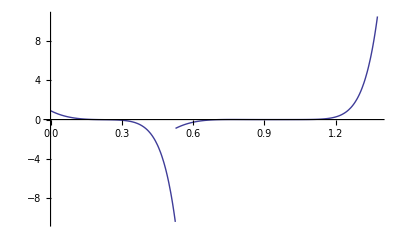

Piecewise[{{0.903095-12.2733 u+57.7127 u^2-81.1656 u^3-196.941 u^4+791.195 u^5-620.07 u^6-1013.52 u^7+2246.26 u^8-4941.42 u^9+359.015 u^10, 0.≤u<0.525731}, {6.56885-177.031 u+536.527 u^2+491.343 u^3-4592.24 u^4+7820.65 u^5-4024.87 u^6-3424.66 u^7+5836.78 u^8-3053.97 u^9+580.899 u^10, 0.525731≤u<1.37638}, {0., True}}]

{a[0]→-0.00139132,b[0]→0.00139108,a[1]→0.00994075,b[1]→-0.0160772,a[2]→-0.0245749,b[2]→0.0642615,a[3]→0.01817,b[3]→-0.0767304,a[4]→0.0231783,b[4]→-0.157575,a[5]→-0.0489547,b[5]→0.531359,a[6]→0.0201705,b[6]→-0.341774,a[7]→0.0173329,b[7]→-0.429828,a[8]→-0.0201959,b[8]→0.586376,a[9]→0.023357,b[9]→0,a[10]→-0.00089216,b[10]→-0.177544}

```mathematica
l=2;k=1;
λ/.λSol[n][[l]]/.σSol//N
1/σ^10/.σSol//N
f[norm_,u_]:=Poly[norm,n,u]/.Flatten[Table[{vector[n][[i]]->  ρ[n][[l,k,i]]},{i,Length[vector[n]]}]]/.A2Sol/.αβSol/.ϕSol/.σSol
f[1,u]//N
Integrate[f[1,u]//N,{u,0,A2/.A2Sol}]//N//Chop
halfnorm=2*Integrate[f[1,u]//N,{u,α/.αSol,A2/.A2Sol}]//N//Chop
Plot[f[halfnorm,u]//N,{u,0,A2/.A2Sol},PlotRange->Full,ImageSize->Scaled[0.5]]
f[halfnorm,u]//N
Flatten[Table[{vector[n][[i]]->  ρ[n][[l,k,i]]},{i,Length[vector[n]]}]]
```

```mathematica
ψ[11,2,u_]:=Poly[-0.0015406096862361975,10,u]/.{a[0]->-0.0013913175281760688,b[0]->0.0013910767324734352,a[1]->0.009940747502585872,b[1]->-0.016077179398630032,a[2]->-0.024574879320734017,b[2]->0.06426154909402043,a[3]->0.018170021229475645,b[3]->-0.0767304072314762,a[4]->0.023178349367433404,b[4]->-0.15757508483412805,a[5]->-0.04895471262930236,b[5]->0.5313594426068985,a[6]->0.0201704508762615,b[6]->-0.3417736041946569,a[7]->0.017332910066519977,b[7]->-0.42982798419295665,a[8]->-0.02019586274596838,b[8]->0.5863756025841038,a[9]->0.02335704114627296,b[9]->0,a[10]->-0.0008921595841243427,b[10]->-0.17754424034159064}/.A2Sol/.αβSol/.ϕSol/.σSol//N
𝕍[11]:={1/σ^10/.σSol//N,2}
ψ[11,2,u]
```

Piecewise[{{0.903095-12.2733 u+57.7127 u^2-81.1656 u^3-196.941 u^4+791.195 u^5-620.07 u^6-1013.52 u^7+2246.26 u^8-4941.42 u^9+359.015 u^10, 0.≤u<0.525731}, {6.56885-177.031 u+536.527 u^2+491.343 u^3-4592.24 u^4+7820.65 u^5-4024.87 u^6-3424.66 u^7+5836.78 u^8-3053.97 u^9+580.899 u^10, 0.525731≤u<1.37638}, {0., True}}]

9.64488×10^-6

9.64488×10^-6

Piecewise[{{-0.00119625+0.0154691 u-0.090925 u^2+0.320666 u^3-0.753931 u^4+1.24082 u^5-1.45867 u^6+1.22484 u^7-0.719941 u^8+0.282114 u^9-0.0663289 u^10, 0.≤u<0.525731}, {0.236864-1.8871 u+6.82057 u^2-14.7438 u^3+21.136 u^4-21.0248 u^5+14.7182 u^6-7.17031 u^7+2.32978 u^8-0.456469 u^9+0.0409935 u^10, 0.525731≤u<1.37638}, {0., True}}]

0

0.000170124

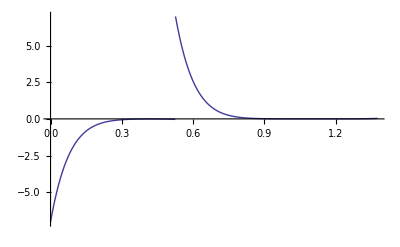

Piecewise[{{-7.03165+90.9282 u-534.463 u^2+1884.9 u^3-4431.66 u^4+7293.61 u^5-8574.16 u^6+7199.66 u^7-4231.86 u^8+1658.28 u^9-389.885 u^10, 0.≤u<0.525731}, {1392.3-11092.5 u+40091.7 u^2-86665.1 u^3+124239. u^4-123585. u^5+86514.7 u^6-42147.6 u^7+13694.6 u^8-2683.16 u^9+240.962 u^10, 0.525731≤u<1.37638}, {0., True}}]

{a[0]→-0.00119625,b[0]→0.00119622,a[1]→0.00813258,b[1]→-0.0131579,a[2]→-0.025131,b[2]→0.0657826,a[3]→0.0465955,b[3]→-0.197292,a[4]→-0.0575952,b[4]→0.394295,a[5]→0.0498341,b[5]→-0.550953,a[6]→-0.0307992,b[6]→0.548176,a[7]→0.0135964,b[7]→-0.386361,a[8]→-0.00420152,b[8]→0.186382,a[9]→0.00086556,b[9]→-0.0561947,a[10]→-0.000106989,b[10]→0.00813258}

```mathematica
l=1;k=1;
λ/.λSol[n][[l]]/.σSol//N
1/σ^12/.σSol//N
f[norm_,u_]:=Poly[norm,n,u]/.Flatten[Table[{vector[n][[i]]->  ρ[n][[l,k,i]]},{i,Length[vector[n]]}]]/.A2Sol/.αβSol/.ϕSol/.σSol
f[1,u]//N
Integrate[f[1,u]//N,{u,0,A2/.A2Sol}]//N//Chop
halfnorm=2*Integrate[f[1,u]//N,{u,α/.αSol,A2/.A2Sol}]//N//Chop
Plot[f[halfnorm,u]//N,{u,0,A2/.A2Sol},PlotRange->Full,ImageSize->Scaled[0.5]]
f[halfnorm,u]//N
Flatten[Table[{vector[n][[i]]->  ρ[n][[l,k,i]]},{i,Length[vector[n]]}]]
```

```mathematica
ψ[13,1,u_]:=Poly[0.00017012407324282282,10,u]/.{a[0]->-0.0011962534846784202,b[0]->0.0011962232785454013,a[1]->0.008132578439601319,b[1]->-0.013157918443937829,a[2]->-0.025131049459236107,b[2]->0.06578255468187523,a[3]->0.046595528216286874,b[3]->-0.19729239050613906,a[4]->-0.05759524032283956,b[4]->0.3942953650021851,a[5]->0.049834142553625976,b[5]->-0.5509527296712301,a[6]->-0.030799193898348107,b[6]->0.5481755680898809,a[7]->0.013596391896626715,b[7]->-0.3863606176269065,a[8]->-0.004201516158239119,b[8]->0.1863821128651374,a[9]->0.0008655599300246841,b[9]->-0.056194734936756245,a[10]->-0.00010698909121107172,b[10]->0.008132578439598973}/.A2Sol/.αβSol/.ϕSol/.σSol//N
𝕍[13]:={1/σ^12/.σSol//N,1}
ψ[13,1,u]
```

Piecewise[{{-7.03165+90.9282 u-534.463 u^2+1884.9 u^3-4431.66 u^4+7293.61 u^5-8574.16 u^6+7199.66 u^7-4231.86 u^8+1658.28 u^9-389.885 u^10, 0.≤u<0.525731}, {1392.3-11092.5 u+40091.7 u^2-86665.1 u^3+124239. u^4-123585. u^5+86514.7 u^6-42147.6 u^7+13694.6 u^8-2683.16 u^9+240.962 u^10, 0.525731≤u<1.37638}, {0., True}}]

#### Closed Forms of the Matrices

```mathematica
JA[n_Integer,i_Integer,j_Integer] := α^(-i)KroneckerDelta[i,j]
JB[n_Integer,i_Integer,j_Integer] := Binomial[j,i](-α)^(j-i) β^(-j) If[i-j> 0,0,1]
LA[n_Integer,i_Integer,j_Integer] :=α^(-i)/σ^(i+1)KroneckerDelta[i,j]
LB2[n_Integer,i_Integer,j_Integer] :=β^(-i)/σ^(i+1)KroneckerDelta[i,j]
LB[n_Integer,i_Integer,j_Integer] :=Binomial[j,i]((-1)^(j-i)(α-β))^(j-i)β^(-j)/σ^(i+1)If[i-j> 0,0,1]
```

```mathematica
n=2
```

2

```mathematica
Table[JA[n,i,j],{i,0,n},{j,0,n}]//TraditionalForm
JALarge=Table[If[EvenQ[i]&&EvenQ[j],JA[n,i/2,j/2],0],{i,0,2n+1},{j,0,2n+1}];
JALarge//TraditionalForm
```

(1 | 0 | 0
0 | 1/α | 0
0 | 0 | 1/α^2)

(1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/α | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/α^2 | 0
0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Table[JB[n,i,j],{i,0,n},{j,0,n}]//TraditionalForm
JBLarge=Table[If[OddQ[i]&&OddQ[j],JB[n,(i-1)/2,(j-1)/2],0],{i,0,2n+1},{j,0,2n+1}];
JBLarge//TraditionalForm
```

(1 | -α/β | α^2/β^2
0 | 1/β | -(2 α)/β^2
0 | 0 | 1/β^2)

(0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | -α/β | 0 | α^2/β^2
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/β | 0 | -(2 α)/β^2
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/β^2)

```mathematica
JLarge=JALarge+JBLarge;
%//TraditionalForm
```

(1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | -α/β | 0 | α^2/β^2
0 | 0 | 1/α | 0 | 0 | 0
0 | 0 | 0 | 1/β | 0 | -(2 α)/β^2
0 | 0 | 0 | 0 | 1/α^2 | 0
0 | 0 | 0 | 0 | 0 | 1/β^2)

```mathematica
Table[LA[n,i,j],{i,0,n},{j,0,n}]//TraditionalForm
LALarge=Table[If[EvenQ[i]&&EvenQ[j],LA[n,i/2,j/2],0],{i,0,2n+1},{j,0,2n+1}];
LALarge//TraditionalForm
LA2Large=Table[If[OddQ[i]&&EvenQ[j],LA[n,(i-1)/2,j/2],0],{i,0,2n+1},{j,0,2n+1}];
LA2Large//TraditionalForm
```

(1/σ | 0 | 0
0 | 1/(α σ^2) | 0
0 | 0 | 1/(α^2 σ^3))

(1/σ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/(α σ^2) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/(α^2 σ^3) | 0
0 | 0 | 0 | 0 | 0 | 0)

(0 | 0 | 0 | 0 | 0 | 0
1/σ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/(α σ^2) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/(α^2 σ^3) | 0)

```mathematica
Table[LB2[n,i,j],{i,0,n},{j,0,n}]//TraditionalForm
LB2Large=Table[If[OddQ[i]&&OddQ[j],LB2[n,(i-1)/2,(j-1)/2],0],{i,0,2n+1},{j,0,2n+1}];
LB2Large//TraditionalForm
LB3Large=Table[If[EvenQ[i]&&OddQ[j],LB2[n,i/2,(j-1)/2],0],{i,0,2n+1},{j,0,2n+1}];
LB3Large//TraditionalForm
```

(1/σ | 0 | 0
0 | 1/(β σ^2) | 0
0 | 0 | 1/(β^2 σ^3))

(0 | 0 | 0 | 0 | 0 | 0
0 | 1/σ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/(β σ^2) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/(β^2 σ^3))

(0 | 1/σ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/(β σ^2) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/(β^2 σ^3)
0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Table[LB[n,i,j],{i,0,n},{j,0,n}]//TraditionalForm
LBLarge=Table[If[OddQ[i]&&OddQ[j],LB[n,(i-1)/2,(j-1)/2],0],{i,0,2n+1},{j,0,2n+1}];
LBLarge//TraditionalForm
```

(1/σ | (β-α)/(β σ) | (α-β)^2/(β^2 σ)
0 | 1/(β σ^2) | (2 (β-α))/(β^2 σ^2)
0 | 0 | 1/(β^2 σ^3))

(0 | 0 | 0 | 0 | 0 | 0
0 | 1/σ | 0 | (β-α)/(β σ) | 0 | (α-β)^2/(β^2 σ)
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/(β σ^2) | 0 | (2 (β-α))/(β^2 σ^2)
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/(β^2 σ^3))

```mathematica
LLarge=LALarge+LA2Large+LB2Large+LB3Large+LBLarge;
%//TraditionalForm
```

(1/σ | 1/σ | 0 | 0 | 0 | 0
1/σ | 2/σ | 0 | (β-α)/(β σ) | 0 | (α-β)^2/(β^2 σ)
0 | 0 | 1/(α σ^2) | 1/(β σ^2) | 0 | 0
0 | 0 | 1/(α σ^2) | 2/(β σ^2) | 0 | (2 (β-α))/(β^2 σ^2)
0 | 0 | 0 | 0 | 1/(α^2 σ^3) | 1/(β^2 σ^3)
0 | 0 | 0 | 0 | 1/(α^2 σ^3) | 2/(β^2 σ^3))

```mathematica
Det[LLarge-λ JLarge]
```

1/(α^6 β^9 σ^12)(α^3 β^6-3 α^3 β^6 λ σ-3 α^3 β^6 λ σ^2+α^3 β^6 λ^2 σ^2-3 α^3 β^6 λ σ^3+9 α^3 β^6 λ^2 σ^3+10 α^3 β^6 λ^2 σ^4-3 α^3 β^6 λ^3 σ^4+9 α^3 β^6 λ^2 σ^5-6 α^3 β^6 λ^3 σ^5+α^3 β^6 λ^2 σ^6-27 α^3 β^6 λ^3 σ^6+α^3 β^6 λ^4 σ^6-6 α^3 β^6 λ^3 σ^7+9 α^3 β^6 λ^4 σ^7-3 α^3 β^6 λ^3 σ^8+10 α^3 β^6 λ^4 σ^8+9 α^3 β^6 λ^4 σ^9-3 α^3 β^6 λ^5 σ^9+α^3 β^6 λ^4 σ^10-3 α^3 β^6 λ^5 σ^10-3 α^3 β^6 λ^5 σ^11+α^3 β^6 λ^6 σ^12)

```mathematica
determinantFactor[n_Integer,i_Integer]:=(α β)^(-i)(λ^2-3λ/σ^(i+1)+1/σ^(2(i+1)))
```

```mathematica
Product[determinantFactor[n,i],{i,0,n}]
```

((λ^2+1/σ^6-(3 λ)/σ^3) (λ^2+1/σ^4-(3 λ)/σ^2) (λ^2+1/σ^2-(3 λ)/σ))/(α^3 β^3)

#### Construction of the Dual Space

```mathematica
qn=Join[{{1,1},{2,1}},Riffle[Table[{i,1},{i,3,13}],Table[{i,2},{i,3,13}]]]
Do[
Print[qn[[i]]];
Print[ψ[qn[[i,1]],qn[[i,2]],u]],
{i,Length[qn]}]
```

{{1,1},{2,1},{3,1},{3,2},{4,1},{4,2},{5,1},{5,2},{6,1},{6,2},{7,1},{7,2},{8,1},{8,2},{9,1},{9,2},{10,1},{10,2},{11,1},{11,2},{12,1},{12,2},{13,1},{13,2}}

{1,1}

Piecewise[{{0.525731, 0.≤u<0.525731}, {0.850651, 0.525731≤u<1.37638}, {0., True}}]

{2,1}

Piecewise[{{-1.17557+0.854102 u, 0.≤u<0.525731}, {-0.726543+1.38197 u, 0.525731≤u<1.37638}, {0., True}}]

{3,1}

Piecewise[{{-0.951057, 0.≤u<0.525731}, {0.587785, 0.525731≤u<1.37638}, {0., True}}]

{3,2}

Piecewise[{{0.-4.1459 u+1.50609 u^2, 0.≤u<0.525731}, {0.673542-2.56231 u+2.4369 u^2, 0.525731≤u<1.37638}, {0., True}}]

{4,1}

Piecewise[{{-2.4899+5.8541 u, 0.≤u<0.525731}, {4.02874-3.61803 u, 0.525731≤u<1.37638}, {0., True}}]

{4,2}

Piecewise[{{-0.438257+2.16913 u-12.9958 u^2+3.14735 u^3, 0.≤u<0.525731}, {0.339123+2.88201 u-8.03188 u^2+5.09251 u^3, 0.525731≤u<1.37638}, {0., True}}]

{5,1}

Piecewise[{{-2.09062+7.37303 u-8.66752 u^2, 0.≤u<0.525731}, {6.7654-11.9298 u+5.35682 u^2, 0.525731≤u<1.37638}, {0., True}}]

{5,2}

Piecewise[{{-0.81518+2.35384 u+0.295668 u^2-23.3029 u^3+4.23264 u^4, 0.≤u<0.525731}, {2.29937-5.79889 u+11.1746 u^2-14.402 u^3+6.84856 u^4, 0.525731≤u<1.37638}, {0., True}}]

{6,1}

Piecewise[{{-3.25932+15.3262 u-27.0256 u^2+21.1803 u^3, 0.≤u<0.525731}, {19.0804-49.5967 u+43.7284 u^2-13.0902 u^3, 0.525731≤u<1.37638}, {0., True}}]

{6,2}

Piecewise[{{-0.595008+2.7979 u-8.15686 u^2+19.0228 u^3-72.0722 u^4+10.4727 u^5, 0.≤u<0.525731}, {4.92468-13.2433 u+0.886665 u^2+35.0786 u^3-44.5431 u^4+16.9452 u^5, 0.525731≤u<1.37638}, {0., True}}]

{7,1}

Piecewise[{{-3.3504+19.6932 u-46.3015 u^2+54.4306 u^3-31.9935 u^4, 0.≤u<0.525731}, {33.8062-115.286 u+149.835 u^2-88.0706 u^3+19.7731 u^4, 0.525731≤u<1.37638}, {0., True}}]

{7,2}

Piecewise[{{-0.663778+4.66802 u-10.9752 u^2+0.191973 u^3+37.2412 u^4-170.524 u^5+20.6488 u^6, 0.≤u<0.525731}, {4.89566-10.2746 u+10.7378 u^2-48.8589 u^3+115.5 u^4-105.39 u^5+33.4105 u^6, 0.525731≤u<1.37638}, {0., True}}]

{8,1}

Piecewise[{{-4.2665+30.0935 u-88.4425 u^2+138.627 u^3-122.224 u^4+57.4734 u^5, 0.≤u<0.525731}, {72.2928-303.648 u+517.751 u^2-448.607 u^3+197.763 u^4-35.5205 u^5, 0.525731≤u<1.37638}, {0., True}}]

{8,2}

Piecewise[{{-1.55323+10.0248 u-25.6328 u^2+40.1775 u^3-67.1769 u^4+106.245 u^5-284.009 u^6+29.4778 u^7, 0.≤u<0.525731}, {25.7135-119.16 u+235.26 u^2-212.555 u^3-12.592 u^4+211.178 u^5-175.527 u^6+47.6961 u^7, 0.525731≤u<1.37638}, {0., True}}]

{9,1}

Piecewise[{{-4.60632+37.9054 u-133.681 u^2+261.92 u^3-307.905 u^4+217.178 u^5-85.1028 u^6, 0.≤u<0.525731}, {129.136-642.279 u+1348.87 u^2-1533.3 u^3+996.401 u^4-351.402 u^5+52.5964 u^6, 0.525731≤u<1.37638}, {0., True}}]

{9,2}

Piecewise[{{-11.8337+95.3587 u-318.485 u^2+575.128 u^3-676.103 u^4+720.038 u^5-758.56 u^6+1553.46 u^7-141.081 u^8, 0.≤u<0.525731}, {312.938-1592.63 u+3558.3 u^2-4454.28 u^3+2977.97 u^4-236.28 u^5-1297.8 u^6+960.089 u^7-228.275 u^8, 0.525731≤u<1.37638}, {0., True}}]

{10,1}

Piecewise[{{-5.36153+50.4228 u-207.465 u^2+487.779 u^3-716.773 u^4+674.093 u^5-396.222 u^6+133.082 u^7, 0.≤u<0.525731}, {246.516-1413.58 u+3515.34 u^2-4921.77 u^3+4196.06 u^4-2181.41 u^5+641.101 u^6-82.2492 u^7, 0.525731≤u<1.37638}, {0., True}}]

{10,2}

Piecewise[{{0.27029-2.54196 u+22.3339 u^2-122.309 u^3+323.324 u^4-304.072 u^5-297.534 u^6+899.765 u^7-2282.05 u^8+184.223 u^9, 0.≤u<0.525731}, {-50.4684+292.369 u-514.506 u^2-116.322 u^3+1302.1 u^4-872.969 u^5-1337.74 u^6+2409.85 u^7-1410.38 u^8+298.079 u^9, 0.525731≤u<1.37638}, {0., True}}]

{11,1}

Piecewise[{{-5.83083+61.691 u-290.088 u^2+795.712 u^3-1403.12 u^4+1649.47 u^5-1292.71 u^6+651.289 u^7-191.409 u^8, 0.≤u<0.525731}, {437.389-2836.47 u+8132.46 u^2-13482.8 u^3+14157.7 u^4-9656.16 u^5+4183.3 u^6-1053.81 u^7+118.297 u^8, 0.525731≤u<1.37638}, {0., True}}]

{11,2}

Piecewise[{{0.903095-12.2733 u+57.7127 u^2-81.1656 u^3-196.941 u^4+791.195 u^5-620.07 u^6-1013.52 u^7+2246.26 u^8-4941.42 u^9+359.015 u^10, 0.≤u<0.525731}, {6.56885-177.031 u+536.527 u^2+491.343 u^3-4592.24 u^4+7820.65 u^5-4024.87 u^6-3424.66 u^7+5836.78 u^8-3053.97 u^9+580.899 u^10, 0.525731≤u<1.37638}, {0., True}}]

{12,1}

Piecewise[{{-6.49846+76.3939 u-404.129 u^2+1266.89 u^3-2606.3 u^4+3676.67 u^5-3601.82 u^6+2419.54 u^7-1066.63 u^8+278.643 u^9, 0.≤u<0.525731}, {792.759-5730.55 u+18581.3 u^2-35516.4 u^3+44161.8 u^4-37098.2 u^5+21085.4 u^6-7829.79 u^7+1725.84 u^8-172.211 u^9, 0.525731≤u<1.37638}, {0., True}}]

{12,2}

Indeterminate

{13,1}

Piecewise[{{-7.03165+90.9282 u-534.463 u^2+1884.9 u^3-4431.66 u^4+7293.61 u^5-8574.16 u^6+7199.66 u^7-4231.86 u^8+1658.28 u^9-389.885 u^10, 0.≤u<0.525731}, {1392.3-11092.5 u+40091.7 u^2-86665.1 u^3+124239. u^4-123585. u^5+86514.7 u^6-42147.6 u^7+13694.6 u^8-2683.16 u^9+240.962 u^10, 0.525731≤u<1.37638}, {0., True}}]

{13,2}

Indeterminate

```mathematica
n=10;
qm=Join[Take[qn,2 n],{qn[[2n+1]],qn[[2n+3]]}]
Clear[c,d]
Do[
χ[qm[[i,1]],qm[[i,2]],fA_,fB_,u_]:= Integrate[Sum[c[qm[[i,1]],qm[[i,2]],j]D[fA,{u,j}],{j,0,n}],{u,0,α/.αSol}]+Integrate[Sum[d[qm[[i,1]],qm[[i,2]],j]D[fB,{u,j}],{j,0,n}],{u,α/.αSol,A2/.A2Sol}],
{i,Length[qm]}]
```

{{1,1},{2,1},{3,1},{3,2},{4,1},{4,2},{5,1},{5,2},{6,1},{6,2},{7,1},{7,2},{8,1},{8,2},{9,1},{9,2},{10,1},{10,2},{11,1},{11,2},{12,1},{13,1}}

```mathematica
χSol=
Solve[
Table[
χ[qm[[i,1]],qm[[i,2]],#1,#2,u]&[ψ[qm[[j,1]],qm[[j,2]],u][[1,1,1]],ψ[qm[[j,1]],qm[[j,2]],u][[1,2,1]]]==If[qm[[i]]==qm[[j]],1,0],
{i,Length[qm]},{j,Length[qm]}]//Flatten,
Table[
Join[
Table[c[qm[[i,1]],qm[[i,2]],j],{j,0,n}],
Table[d[qm[[i,1]],qm[[i,2]],j],{j,0,n}]
],
{i,Length[qm]}]//Flatten
]//Chop
```

{{c[1,1,0]→1.,c[1,1,1]→0,c[1,1,2]→0,c[1,1,3]→0,c[1,1,4]→0,c[1,1,5]→0,c[1,1,6]→0,c[1,1,7]→0,c[1,1,8]→0,c[1,1,9]→0,c[1,1,10]→0,d[1,1,0]→1.,d[1,1,1]→0,d[1,1,2]→0,d[1,1,3]→0,d[1,1,4]→0,d[1,1,5]→0,d[1,1,6]→0,d[1,1,7]→0,d[1,1,8]→0,d[1,1,9]→0,d[1,1,10]→0,c[2,1,0]→0,c[2,1,1]→0.615537,c[2,1,2]→0,c[2,1,3]→0,c[2,1,4]→0,c[2,1,5]→0,c[2,1,6]→0,c[2,1,7]→0,c[2,1,8]→0,c[2,1,9]→0,c[2,1,10]→0,d[2,1,0]→0,d[2,1,1]→0.615537,d[2,1,2]→0,d[2,1,3]→0,d[2,1,4]→0,d[2,1,5]→0,d[2,1,6]→0,d[2,1,7]→0,d[2,1,8]→0,d[2,1,9]→0,d[2,1,10]→0,c[3,1,0]→-1.44721,c[3,1,1]→-0.850651,c[3,1,2]→-0.233333,c[3,1,3]→-0.0195928,c[3,1,4]→-0.000307104,c[3,1,5]→0.0000902555,c[3,1,6]→2.52623×10^-6,c[3,1,7]→-5.93952×10^-7,c[3,1,8]→-1.86195×10^-8,c[3,1,9]→4.10411×10^-9,c[3,1,10]→1.32278×10^-10,d[3,1,0]→0.552786,d[3,1,1]→-0.525731,d[3,1,2]→-0.290273,d[3,1,3]→-0.0317019,d[3,1,4]→0.000804008,d[3,1,5]→0.000382328,d[3,1,6]→-0.000017315,d[3,1,7]→-6.58703×10^-6,d[3,1,8]→3.34114×10^-7,d[3,1,9]→1.19161×10^-7,d[3,1,10]→-6.21426×10^-9,c[3,2,0]→0,c[3,2,1]→0,c[3,2,2]→0.174536,c[3,2,3]→0,c[3,2,4]→0,c[3,2,5]→0,c[3,2,6]→0,c[3,2,7]→0,c[3,2,8]→0,c[3,2,9]→0,c[3,2,10]→0,d[3,2,0]→0,d[3,2,1]→0,d[3,2,2]→0.174536,d[3,2,3]→0,d[3,2,4]→0,d[3,2,5]→0,d[3,2,6]→0,d[3,2,7]→0,d[3,2,8]→0,d[3,2,9]→0,d[3,2,10]→0,c[4,1,0]→0,c[4,1,1]→0.235114,c[4,1,2]→0.138197,c[4,1,3]→0.0275917,c[4,1,4]→0.00318305,c[4,1,5]→0.000049892,c[4,1,6]→-0.0000146629,c[4,1,7]→-4.10411×10^-7,c[4,1,8]→9.64934×10^-8,c[4,1,9]→3.02493×10^-9,c[4,1,10]→-6.66753×10^-10,d[4,1,0]→0,d[4,1,1]→-0.0898056,d[4,1,2]→0.0854102,d[4,1,3]→0.0368422,d[4,1,4]→0.00515028,d[4,1,5]→-0.000130619,d[4,1,6]→-0.000062113,d[4,1,7]→2.813×10^-6,d[4,1,8]→1.07013×10^-6,d[4,1,9]→-5.42801×10^-8,d[4,1,10]→-1.93588×10^-8,c[4,2,0]→0,c[4,2,1]→0,c[4,2,2]→0,c[4,2,3]→0.0278399,c[4,2,4]→0,c[4,2,5]→0,c[4,2,6]→0,c[4,2,7]→0,c[4,2,8]→0,c[4,2,9]→0,c[4,2,10]→0,d[4,2,0]→0,d[4,2,1]→0,d[4,2,2]→0,d[4,2,3]→0.0278399,d[4,2,4]→0,d[4,2,5]→0,d[4,2,6]→0,d[4,2,7]→0,d[4,2,8]→0,d[4,2,9]→0,d[4,2,10]→0,c[5,1,0]→0,c[5,1,1]→0,c[5,1,2]→-0.0793989,c[5,1,3]→-0.0466695,c[5,1,4]→-0.0126249,c[5,1,5]→-0.00107493,c[5,1,6]→-0.0000168487,c[5,1,7]→4.95171×10^-6,c[5,1,8]→1.38597×10^-7,c[5,1,9]→-3.25862×10^-8,c[5,1,10]→-1.02153×10^-9,d[5,1,0]→0,d[5,1,1]→0,d[5,1,2]→0.0303277,d[5,1,3]→-0.0288433,d[5,1,4]→-0.0157488,d[5,1,5]→-0.00173927,d[5,1,6]→0.0000441105,d[5,1,7]→0.0000209758,d[5,1,8]→-9.4996×10^-7,d[5,1,9]→-3.61386×10^-7,d[5,1,10]→1.83306×10^-8,c[5,2,0]→0,c[5,2,1]→0,c[5,2,2]→0,c[5,2,3]→0,c[5,2,4]→0.00517537,c[5,2,5]→0,c[5,2,6]→0,c[5,2,7]→0,c[5,2,8]→0,c[5,2,9]→0,c[5,2,10]→0,d[5,2,0]→0,d[5,2,1]→0,d[5,2,2]→0,d[5,2,3]→0,d[5,2,4]→0.00517537,d[5,2,5]→0,d[5,2,6]→0,d[5,2,7]→0,d[5,2,8]→0,d[5,2,9]→0,d[5,2,10]→0,c[6,1,0]→0,c[6,1,1]→0,c[6,1,2]→0,c[6,1,3]→0.0108307,c[6,1,4]→0.0063661,c[6,1,5]→0.0013705,c[6,1,6]→0.000146629,c[6,1,7]→2.2983×10^-6,c[6,1,8]→-6.75454×10^-7,c[6,1,9]→-1.89058×10^-8,c[6,1,10]→4.44502×10^-9,d[6,1,0]→0,d[6,1,1]→0,d[6,1,2]→0,d[6,1,3]→-0.00413694,d[6,1,4]→0.00393447,d[6,1,5]→0.00179663,d[6,1,6]→0.000237251,d[6,1,7]→-6.01703×10^-6,d[6,1,8]→-2.86127×10^-6,d[6,1,9]→1.29582×10^-7,d[6,1,10]→4.9296×10^-8,c[6,2,0]→0,c[6,2,1]→0,c[6,2,2]→0,c[6,2,3]→0,c[6,2,4]→0,c[6,2,5]→0.000418334,c[6,2,6]→0,c[6,2,7]→0,c[6,2,8]→0,c[6,2,9]→0,c[6,2,10]→0,d[6,2,0]→0,d[6,2,1]→0,d[6,2,2]→0,d[6,2,3]→0,d[6,2,4]→0,d[6,2,5]→0.000418334,d[6,2,6]→0,d[6,2,7]→0,d[6,2,8]→0,d[6,2,9]→0,d[6,2,10]→0,c[7,1,0]→0,c[7,1,1]→0,c[7,1,2]→0,c[7,1,3]→0,c[7,1,4]→-0.00179253,c[7,1,5]→-0.00105362,c[7,1,6]→-0.000247846,c[7,1,7]→-0.0000242678,c[7,1,8]→-3.8038×10^-7,c[7,1,9]→1.11791×10^-7,c[7,1,10]→3.129×10^-9,d[7,1,0]→0,d[7,1,1]→0,d[7,1,2]→0,d[7,1,3]→0,d[7,1,4]→0.000684684,d[7,1,5]→-0.000651174,d[7,1,6]→-0.000318372,d[7,1,7]→-0.0000392661,d[7,1,8]→9.95848×10^-7,d[7,1,9]→4.73554×10^-7,d[7,1,10]→-2.14465×10^-8,c[7,2,0]→0,c[7,2,1]→0,c[7,2,2]→0,c[7,2,3]→0,c[7,2,4]→0,c[7,2,5]→0,c[7,2,6]→0.0000353619,c[7,2,7]→0,c[7,2,8]→0,c[7,2,9]→0,c[7,2,10]→0,d[7,2,0]→0,d[7,2,1]→0,d[7,2,2]→0,d[7,2,3]→0,d[7,2,4]→0,d[7,2,5]→0,d[7,2,6]→0.0000353619,d[7,2,7]→0,d[7,2,8]→0,d[7,2,9]→0,d[7,2,10]→0,c[8,1,0]→0,c[8,1,1]→0,c[8,1,2]→0,c[8,1,3]→0,c[8,1,4]→0,c[8,1,5]→0.000199568,c[8,1,6]→0.000117303,c[8,1,7]→0.0000256347,c[8,1,8]→2.70182×10^-6,c[8,1,9]→4.2349×10^-8,c[8,1,10]→-1.24461×10^-8,d[8,1,0]→0,d[8,1,1]→0,d[8,1,2]→0,d[8,1,3]→0,d[8,1,4]→0,d[8,1,5]→-0.0000762282,d[8,1,6]→0.0000724973,d[8,1,7]→0.0000334866,d[8,1,8]→4.37163×10^-6,d[8,1,9]→-1.10871×10^-7,d[8,1,10]→-5.27223×10^-8,c[8,2,0]→0,c[8,2,1]→0,c[8,2,2]→0,c[8,2,3]→0,c[8,2,4]→0,c[8,2,5]→0,c[8,2,6]→0,c[8,2,7]→3.53865×10^-6,c[8,2,8]→0,c[8,2,9]→0,c[8,2,10]→0,d[8,2,0]→0,d[8,2,1]→0,d[8,2,2]→0,d[8,2,3]→0,d[8,2,4]→0,d[8,2,5]→0,d[8,2,6]→0,d[8,2,7]→3.53865×10^-6,d[8,2,8]→0,d[8,2,9]→0,d[8,2,10]→0,c[9,1,0]→0,c[9,1,1]→0,c[9,1,2]→0,c[9,1,3]→0,c[9,1,4]→0,c[9,1,5]→0,c[9,1,6]→-0.0000224627,c[9,1,7]→-0.0000132033,c[9,1,8]→-2.79786×10^-6,c[9,1,9]→-3.04108×10^-7,c[9,1,10]→-4.76667×10^-9,d[9,1,0]→0,d[9,1,1]→0,d[9,1,2]→0,d[9,1,3]→0,d[9,1,4]→0,d[9,1,5]→0,d[9,1,6]→8.58×10^-6,d[9,1,7]→-8.16006×10^-6,d[9,1,8]→-3.68164×10^-6,d[9,1,9]→-4.92056×10^-7,d[9,1,10]→1.24793×10^-8,c[9,2,0]→0,c[9,2,1]→0,c[9,2,2]→0,c[9,2,3]→0,c[9,2,4]→0,c[9,2,5]→0,c[9,2,6]→0,c[9,2,7]→0,c[9,2,8]→-9.24215×10^-8,c[9,2,9]→0,c[9,2,10]→0,d[9,2,0]→0,d[9,2,1]→0,d[9,2,2]→0,d[9,2,3]→0,d[9,2,4]→0,d[9,2,5]→0,d[9,2,6]→0,d[9,2,7]→0,d[9,2,8]→-9.24215×10^-8,d[9,2,9]→0,d[9,2,10]→0,c[10,1,0]→0,c[10,1,1]→0,c[10,1,2]→0,c[10,1,3]→0,c[10,1,4]→0,c[10,1,5]→0,c[10,1,6]→0,c[10,1,7]→2.05205×10^-6,c[10,1,8]→1.20617×10^-6,c[10,1,9]→2.77682×10^-7,c[10,1,10]→2.77814×10^-8,d[10,1,0]→0,d[10,1,1]→0,d[10,1,2]→0,d[10,1,3]→0,d[10,1,4]→0,d[10,1,5]→0,d[10,1,6]→0,d[10,1,7]→-7.83815×10^-7,d[10,1,8]→7.45453×10^-7,d[10,1,9]→3.58419×10^-7,d[10,1,10]→4.49512×10^-8,c[10,2,0]→0,c[10,2,1]→0,c[10,2,2]→0,c[10,2,3]→0,c[10,2,4]→0,c[10,2,5]→0,c[10,2,6]→0,c[10,2,7]→0,c[10,2,8]→0,c[10,2,9]→7.86424×10^-9,c[10,2,10]→0,d[10,2,0]→0,d[10,2,1]→0,d[10,2,2]→0,d[10,2,3]→0,d[10,2,4]→0,d[10,2,5]→0,d[10,2,6]→0,d[10,2,7]→0,d[10,2,8]→0,d[10,2,9]→7.86424×10^-9,d[10,2,10]→0,c[11,1,0]→0,c[11,1,1]→0,c[11,1,2]→0,c[11,1,3]→0,c[11,1,4]→0,c[11,1,5]→0,c[11,1,6]→0,c[11,1,7]→0,c[11,1,8]→-1.78343×10^-7,c[11,1,9]→-1.04827×10^-7,c[11,1,10]→-2.40184×10^-8,d[11,1,0]→0,d[11,1,1]→0,d[11,1,2]→0,d[11,1,3]→0,d[11,1,4]→0,d[11,1,5]→0,d[11,1,6]→0,d[11,1,7]→0,d[11,1,8]→6.8121×10^-8,d[11,1,9]→-6.47869×10^-8,d[11,1,10]→-3.10353×10^-8,c[11,2,0]→0,c[11,2,1]→0,c[11,2,2]→0,c[11,2,3]→0,c[11,2,4]→0,c[11,2,5]→0,c[11,2,6]→0,c[11,2,7]→0,c[11,2,8]→0,c[11,2,9]→0,c[11,2,10]→4.03541×10^-10,d[11,2,0]→0,d[11,2,1]→0,d[11,2,2]→0,d[11,2,3]→0,d[11,2,4]→0,d[11,2,5]→0,d[11,2,6]→0,d[11,2,7]→0,d[11,2,8]→0,d[11,2,9]→0,d[11,2,10]→4.03541×10^-10,c[12,1,0]→0,c[12,1,1]→0,c[12,1,2]→0,c[12,1,3]→0,c[12,1,4]→0,c[12,1,5]→0,c[12,1,6]→0,c[12,1,7]→0,c[12,1,8]→0,c[12,1,9]→1.36122×10^-8,c[12,1,10]→8.00104×10^-9,d[12,1,0]→0,d[12,1,1]→0,d[12,1,2]→0,d[12,1,3]→0,d[12,1,4]→0,d[12,1,5]→0,d[12,1,6]→0,d[12,1,7]→0,d[12,1,8]→0,d[12,1,9]→-5.19939×10^-9,d[12,1,10]→4.94491×10^-9,c[13,1,0]→0,c[13,1,1]→0,c[13,1,2]→0,c[13,1,3]→0,c[13,1,4]→0,c[13,1,5]→0,c[13,1,6]→0,c[13,1,7]→0,c[13,1,8]→0,c[13,1,9]→0,c[13,1,10]→-9.72835×10^-10,d[13,1,0]→0,d[13,1,1]→0,d[13,1,2]→0,d[13,1,3]→0,d[13,1,4]→0,d[13,1,5]→0,d[13,1,6]→0,d[13,1,7]→0,d[13,1,8]→0,d[13,1,9]→0,d[13,1,10]→3.7159×10^-10}}

```mathematica
Do[
Print["⟨u|",qm[[i,1]],",",qm[[i,2]],"⟩"];
Print[ψ[qm[[i,1]],qm[[i,2]],u]];
Print["⟨",qm[[i,1]],",",qm[[i,2]],"|𝒻⟩"];
Print[χ[qm[[i,1]],qm[[i,2]],fA[u],fB[u],u]/.χSol[[1]]],
{i,Length[qm]}]
```

⟨u|1,1⟩

Piecewise[{{0.525731, 0.≤u<0.525731}, {0.850651, 0.525731≤u<1.37638}, {0., True}}]

⟨1,1|𝒻⟩

∫_0^(√(2/(5+√5))) 1. fA[u]ⅆu+∫_(√(2/(5+√5)))^((3+√5)/(√(2 (5+√5)))) 1. fB[u]ⅆu

⟨u|2,1⟩

Piecewise[{{-1.17557+0.854102 u, 0.≤u<0.525731}, {-0.726543+1.38197 u, 0.525731≤u<1.37638}, {0., True}}]

⟨2,1|𝒻⟩

∫_0^(√(2/(5+√5))) 0.615537 fA'[u]ⅆu+∫_(√(2/(5+√5)))^((3+√5)/(√(2 (5+√5)))) 0.615537 fB'[u]ⅆu

⟨u|3,1⟩

Piecewise[{{-0.951057, 0.≤u<0.525731}, {0.587785, 0.525731≤u<1.37638}, {0., True}}]

⟨3,1|𝒻⟩

∫_0^(√(2/(5+√5))) (-1.44721 fA[u]-0.850651 fA'[u]-0.233333 fA''[u]-0.0195928 fA^(3)[u]-0.000307104 fA^(4)[u]+0.0000902555 fA^(5)[u]+2.52623×10^-6 fA^(6)[u]-5.93952×10^-7 fA^(7)[u]-1.86195×10^-8 fA^(8)[u]+4.10411×10^-9 fA^(9)[u]+1.32278×10^-10 fA^(10)[u])ⅆu+∫_(√(2/(5+√5)))^((3+√5)/(√(2 (5+√5)))) (0.552786 fB[u]-0.525731 fB'[u]-0.290273 fB''[u]-0.0317019 fB^(3)[u]+0.000804008 fB^(4)[u]+0.000382328 fB^(5)[u]-0.000017315 fB^(6)[u]-6.58703×10^-6 fB^(7)[u]+3.34114×10^-7 fB^(8)[u]+1.19161×10^-7 fB^(9)[u]-6.21426×10^-9 fB^(10)[u])ⅆu

⟨u|3,2⟩

Piecewise[{{0.-4.1459 u+1.50609 u^2, 0.≤u<0.525731}, {0.673542-2.56231 u+2.4369 u^2, 0.525731≤u<1.37638}, {0., True}}]

⟨3,2|𝒻⟩

∫_0^(√(2/(5+√5))) 0.174536 fA''[u]ⅆu+∫_(√(2/(5+√5)))^((3+√5)/(√(2 (5+√5)))) 0.174536 fB''[u]ⅆu

⟨u|4,1⟩

Piecewise[{{-2.4899+5.8541 u, 0.≤u<0.525731}, {4.02874-3.61803 u, 0.525731≤u<1.37638}, {0., True}}]

⟨4,1|𝒻⟩

∫_0^(√(2/(5+√5))) (0.235114 fA'[u]+0.138197 fA''[u]+0.0275917 fA^(3)[u]+0.00318305 fA^(4)[u]+0.000049892 fA^(5)[u]-0.0000146629 fA^(6)[u]-4.10411×10^-7 fA^(7)[u]+9.64934×10^-8 fA^(8)[u]+3.02493×10^-9 fA^(9)[u]-6.66753×10^-10 fA^(10)[u])ⅆu+∫_(√(2/(5+√5)))^((3+√5)/(√(2 (5+√5)))) (-0.0898056 fB'[u]+0.0854102 fB''[u]+0.0368422 fB^(3)[u]+0.00515028 fB^(4)[u]-0.000130619 fB^(5)[u]-0.000062113 fB^(6)[u]+2.813×10^-6 fB^(7)[u]+1.07013×10^-6 fB^(8)[u]-5.42801×10^-8 fB^(9)[u]-1.93588×10^-8 fB^(10)[u])ⅆu

⟨u|4,2⟩

Piecewise[{{-0.438257+2.16913 u-12.9958 u^2+3.14735 u^3, 0.≤u<0.525731}, {0.339123+2.88201 u-8.03188 u^2+5.09251 u^3, 0.525731≤u<1.37638}, {0., True}}]

⟨4,2|𝒻⟩

∫_0^(√(2/(5+√5))) 0.0278399 fA^(3)[u]ⅆu+∫_(√(2/(5+√5)))^((3+√5)/(√(2 (5+√5)))) 0.0278399 fB^(3)[u]ⅆu

⟨u|5,1⟩

Piecewise[{{-2.09062+7.37303 u-8.66752 u^2, 0.≤u<0.525731}, {6.7654-11.9298 u+5.35682 u^2, 0.525731≤u<1.37638}, {0., True}}]

⟨5,1|𝒻⟩

∫_0^(√(2/(5+√5))) (-0.0793989 fA''[u]-0.0466695 fA^(3)[u]-0.0126249 fA^(4)[u]-0.00107493 fA^(5)[u]-0.0000168487 fA^(6)[u]+4.95171×10^-6 fA^(7)[u]+1.38597×10^-7 fA^(8)[u]-3.25862×10^-8 fA^(9)[u]-1.02153×10^-9 fA^(10)[u])ⅆu+∫_(√(2/(5+√5)))^((3+√5)/(√(2 (5+√5)))) (0.0303277 fB''[u]-0.0288433 fB^(3)[u]-0.0157488 fB^(4)[u]-0.00173927 fB^(5)[u]+0.0000441105 fB^(6)[u]+0.0000209758 fB^(7)[u]-9.4996×10^-7 fB^(8)[u]-3.61386×10^-7 fB^(9)[u]+1.83306×10^-8 fB^(10)[u])ⅆu

⟨u|5,2⟩

Piecewise[{{-0.81518+2.35384 u+0.295668 u^2-23.3029 u^3+4.23264 u^4, 0.≤u<0.525731}, {2.29937-5.79889 u+11.1746 u^2-14.402 u^3+6.84856 u^4, 0.525731≤u<1.37638}, {0., True}}]

⟨5,2|𝒻⟩

∫_0^(√(2/(5+√5))) 0.00517537 fA^(4)[u]ⅆu+∫_(√(2/(5+√5)))^((3+√5)/(√(2 (5+√5)))) 0.00517537 fB^(4)[u]ⅆu

⟨u|6,1⟩

Piecewise[{{-3.25932+15.3262 u-27.0256 u^2+21.1803 u^3, 0.≤u<0.525731}, {19.0804-49.5967 u+43.7284 u^2-13.0902 u^3, 0.525731≤u<1.37638}, {0., True}}]

⟨6,1|𝒻⟩

∫_0^(√(2/(5+√5))) (0.0108307 fA^(3)[u]+0.0063661 fA^(4)[u]+0.0013705 fA^(5)[u]+0.000146629 fA^(6)[u]+2.2983×10^-6 fA^(7)[u]-6.75454×10^-7 fA^(8)[u]-1.89058×10^-8 fA^(9)[u]+4.44502×10^-9 fA^(10)[u])ⅆu+∫_(√(2/(5+√5)))^((3+√5)/(√(2 (5+√5)))) (-0.00413694 fB^(3)[u]+0.00393447 fB^(4)[u]+0.00179663 fB^(5)[u]+0.000237251 fB^(6)[u]-6.01703×10^-6 fB^(7)[u]-2.86127×10^-6 fB^(8)[u]+1.29582×10^-7 fB^(9)[u]+4.9296×10^-8 fB^(10)[u])ⅆu

⟨u|6,2⟩

Piecewise[{{-0.595008+2.7979 u-8.15686 u^2+19.0228 u^3-72.0722 u^4+10.4727 u^5, 0.≤u<0.525731}, {4.92468-13.2433 u+0.886665 u^2+35.0786 u^3-44.5431 u^4+16.9452 u^5, 0.525731≤u<1.37638}, {0., True}}]

⟨6,2|𝒻⟩

∫_0^(√(2/(5+√5))) 0.000418334 fA^(5)[u]ⅆu+∫_(√(2/(5+√5)))^((3+√5)/(√(2 (5+√5)))) 0.000418334 fB^(5)[u]ⅆu

⟨u|7,1⟩

Piecewise[{{-3.3504+19.6932 u-46.3015 u^2+54.4306 u^3-31.9935 u^4, 0.≤u<0.525731}, {33.8062-115.286 u+149.835 u^2-88.0706 u^3+19.7731 u^4, 0.525731≤u<1.37638}, {0., True}}]

⟨7,1|𝒻⟩

∫_0^(√(2/(5+√5))) (-0.00179253 fA^(4)[u]-0.00105362 fA^(5)[u]-0.000247846 fA^(6)[u]-0.0000242678 fA^(7)[u]-3.8038×10^-7 fA^(8)[u]+1.11791×10^-7 fA^(9)[u]+3.129×10^-9 fA^(10)[u])ⅆu+∫_(√(2/(5+√5)))^((3+√5)/(√(2 (5+√5)))) (0.000684684 fB^(4)[u]-0.000651174 fB^(5)[u]-0.000318372 fB^(6)[u]-0.0000392661 fB^(7)[u]+9.95848×10^-7 fB^(8)[u]+4.73554×10^-7 fB^(9)[u]-2.14465×10^-8 fB^(10)[u])ⅆu

⟨u|7,2⟩

Piecewise[{{-0.663778+4.66802 u-10.9752 u^2+0.191973 u^3+37.2412 u^4-170.524 u^5+20.6488 u^6, 0.≤u<0.525731}, {4.89566-10.2746 u+10.7378 u^2-48.8589 u^3+115.5 u^4-105.39 u^5+33.4105 u^6, 0.525731≤u<1.37638}, {0., True}}]

⟨7,2|𝒻⟩

∫_0^(√(2/(5+√5))) 0.0000353619 fA^(6)[u]ⅆu+∫_(√(2/(5+√5)))^((3+√5)/(√(2 (5+√5)))) 0.0000353619 fB^(6)[u]ⅆu

⟨u|8,1⟩

Piecewise[{{-4.2665+30.0935 u-88.4425 u^2+138.627 u^3-122.224 u^4+57.4734 u^5, 0.≤u<0.525731}, {72.2928-303.648 u+517.751 u^2-448.607 u^3+197.763 u^4-35.5205 u^5, 0.525731≤u<1.37638}, {0., True}}]

⟨8,1|𝒻⟩

∫_0^(√(2/(5+√5))) (0.000199568 fA^(5)[u]+0.000117303 fA^(6)[u]+0.0000256347 fA^(7)[u]+2.70182×10^-6 fA^(8)[u]+4.2349×10^-8 fA^(9)[u]-1.24461×10^-8 fA^(10)[u])ⅆu+∫_(√(2/(5+√5)))^((3+√5)/(√(2 (5+√5)))) (-0.0000762282 fB^(5)[u]+0.0000724973 fB^(6)[u]+0.0000334866 fB^(7)[u]+4.37163×10^-6 fB^(8)[u]-1.10871×10^-7 fB^(9)[u]-5.27223×10^-8 fB^(10)[u])ⅆu

⟨u|8,2⟩

Piecewise[{{-1.55323+10.0248 u-25.6328 u^2+40.1775 u^3-67.1769 u^4+106.245 u^5-284.009 u^6+29.4778 u^7, 0.≤u<0.525731}, {25.7135-119.16 u+235.26 u^2-212.555 u^3-12.592 u^4+211.178 u^5-175.527 u^6+47.6961 u^7, 0.525731≤u<1.37638}, {0., True}}]

⟨8,2|𝒻⟩

∫_0^(√(2/(5+√5))) 3.53865×10^-6 fA^(7)[u]ⅆu+∫_(√(2/(5+√5)))^((3+√5)/(√(2 (5+√5)))) 3.53865×10^-6 fB^(7)[u]ⅆu

⟨u|9,1⟩

Piecewise[{{-4.60632+37.9054 u-133.681 u^2+261.92 u^3-307.905 u^4+217.178 u^5-85.1028 u^6, 0.≤u<0.525731}, {129.136-642.279 u+1348.87 u^2-1533.3 u^3+996.401 u^4-351.402 u^5+52.5964 u^6, 0.525731≤u<1.37638}, {0., True}}]

⟨9,1|𝒻⟩

∫_0^(√(2/(5+√5))) (-0.0000224627 fA^(6)[u]-0.0000132033 fA^(7)[u]-2.79786×10^-6 fA^(8)[u]-3.04108×10^-7 fA^(9)[u]-4.76667×10^-9 fA^(10)[u])ⅆu+∫_(√(2/(5+√5)))^((3+√5)/(√(2 (5+√5)))) (8.58×10^-6 fB^(6)[u]-8.16006×10^-6 fB^(7)[u]-3.68164×10^-6 fB^(8)[u]-4.92056×10^-7 fB^(9)[u]+1.24793×10^-8 fB^(10)[u])ⅆu

⟨u|9,2⟩

Piecewise[{{-11.8337+95.3587 u-318.485 u^2+575.128 u^3-676.103 u^4+720.038 u^5-758.56 u^6+1553.46 u^7-141.081 u^8, 0.≤u<0.525731}, {312.938-1592.63 u+3558.3 u^2-4454.28 u^3+2977.97 u^4-236.28 u^5-1297.8 u^6+960.089 u^7-228.275 u^8, 0.525731≤u<1.37638}, {0., True}}]

⟨9,2|𝒻⟩

∫_0^(√(2/(5+√5))) -9.24215×10^-8 fA^(8)[u]ⅆu+∫_(√(2/(5+√5)))^((3+√5)/(√(2 (5+√5)))) -9.24215×10^-8 fB^(8)[u]ⅆu

⟨u|10,1⟩

Piecewise[{{-5.36153+50.4228 u-207.465 u^2+487.779 u^3-716.773 u^4+674.093 u^5-396.222 u^6+133.082 u^7, 0.≤u<0.525731}, {246.516-1413.58 u+3515.34 u^2-4921.77 u^3+4196.06 u^4-2181.41 u^5+641.101 u^6-82.2492 u^7, 0.525731≤u<1.37638}, {0., True}}]

⟨10,1|𝒻⟩

∫_0^(√(2/(5+√5))) (2.05205×10^-6 fA^(7)[u]+1.20617×10^-6 fA^(8)[u]+2.77682×10^-7 fA^(9)[u]+2.77814×10^-8 fA^(10)[u])ⅆu+∫_(√(2/(5+√5)))^((3+√5)/(√(2 (5+√5)))) (-7.83815×10^-7 fB^(7)[u]+7.45453×10^-7 fB^(8)[u]+3.58419×10^-7 fB^(9)[u]+4.49512×10^-8 fB^(10)[u])ⅆu

⟨u|10,2⟩

Piecewise[{{0.27029-2.54196 u+22.3339 u^2-122.309 u^3+323.324 u^4-304.072 u^5-297.534 u^6+899.765 u^7-2282.05 u^8+184.223 u^9, 0.≤u<0.525731}, {-50.4684+292.369 u-514.506 u^2-116.322 u^3+1302.1 u^4-872.969 u^5-1337.74 u^6+2409.85 u^7-1410.38 u^8+298.079 u^9, 0.525731≤u<1.37638}, {0., True}}]

⟨10,2|𝒻⟩

∫_0^(√(2/(5+√5))) 7.86424×10^-9 fA^(9)[u]ⅆu+∫_(√(2/(5+√5)))^((3+√5)/(√(2 (5+√5)))) 7.86424×10^-9 fB^(9)[u]ⅆu

⟨u|11,1⟩

Piecewise[{{-5.83083+61.691 u-290.088 u^2+795.712 u^3-1403.12 u^4+1649.47 u^5-1292.71 u^6+651.289 u^7-191.409 u^8, 0.≤u<0.525731}, {437.389-2836.47 u+8132.46 u^2-13482.8 u^3+14157.7 u^4-9656.16 u^5+4183.3 u^6-1053.81 u^7+118.297 u^8, 0.525731≤u<1.37638}, {0., True}}]

⟨11,1|𝒻⟩

∫_0^(√(2/(5+√5))) (-1.78343×10^-7 fA^(8)[u]-1.04827×10^-7 fA^(9)[u]-2.40184×10^-8 fA^(10)[u])ⅆu+∫_(√(2/(5+√5)))^((3+√5)/(√(2 (5+√5)))) (6.8121×10^-8 fB^(8)[u]-6.47869×10^-8 fB^(9)[u]-3.10353×10^-8 fB^(10)[u])ⅆu

⟨u|11,2⟩

Piecewise[{{0.903095-12.2733 u+57.7127 u^2-81.1656 u^3-196.941 u^4+791.195 u^5-620.07 u^6-1013.52 u^7+2246.26 u^8-4941.42 u^9+359.015 u^10, 0.≤u<0.525731}, {6.56885-177.031 u+536.527 u^2+491.343 u^3-4592.24 u^4+7820.65 u^5-4024.87 u^6-3424.66 u^7+5836.78 u^8-3053.97 u^9+580.899 u^10, 0.525731≤u<1.37638}, {0., True}}]

⟨11,2|𝒻⟩

∫_0^(√(2/(5+√5))) 4.03541×10^-10 fA^(10)[u]ⅆu+∫_(√(2/(5+√5)))^((3+√5)/(√(2 (5+√5)))) 4.03541×10^-10 fB^(10)[u]ⅆu

⟨u|12,1⟩

Piecewise[{{-6.49846+76.3939 u-404.129 u^2+1266.89 u^3-2606.3 u^4+3676.67 u^5-3601.82 u^6+2419.54 u^7-1066.63 u^8+278.643 u^9, 0.≤u<0.525731}, {792.759-5730.55 u+18581.3 u^2-35516.4 u^3+44161.8 u^4-37098.2 u^5+21085.4 u^6-7829.79 u^7+1725.84 u^8-172.211 u^9, 0.525731≤u<1.37638}, {0., True}}]

⟨12,1|𝒻⟩

∫_0^(√(2/(5+√5))) (1.36122×10^-8 fA^(9)[u]+8.00104×10^-9 fA^(10)[u])ⅆu+∫_(√(2/(5+√5)))^((3+√5)/(√(2 (5+√5)))) (-5.19939×10^-9 fB^(9)[u]+4.94491×10^-9 fB^(10)[u])ⅆu

⟨u|13,1⟩

Piecewise[{{-7.03165+90.9282 u-534.463 u^2+1884.9 u^3-4431.66 u^4+7293.61 u^5-8574.16 u^6+7199.66 u^7-4231.86 u^8+1658.28 u^9-389.885 u^10, 0.≤u<0.525731}, {1392.3-11092.5 u+40091.7 u^2-86665.1 u^3+124239. u^4-123585. u^5+86514.7 u^6-42147.6 u^7+13694.6 u^8-2683.16 u^9+240.962 u^10, 0.525731≤u<1.37638}, {0., True}}]

⟨13,1|𝒻⟩

∫_0^(√(2/(5+√5))) -9.72835×10^-10 fA^(10)[u]ⅆu+∫_(√(2/(5+√5)))^((3+√5)/(√(2 (5+√5)))) 3.7159×10^-10 fB^(10)[u]ⅆu

#### Koopman operator

D^n∘𝒦 = σ^n𝒦∘D^n

```mathematica
map[u_]:=σ u-α
Koop[f_,u_]:=f[map[u]]
g:=(Sum[a[i]#^i,{i,0,3}])&
g
```

∑_(i=0)^3 a[i] #1^i&

```mathematica
Koop[g,u]
DK=Table[D[%,{u,i}],{i,0,3}]
```

a[0]+(-α+u σ) a[1]+(-α+u σ)^2 a[2]+(-α+u σ)^3 a[3]

{a[0]+(-α+u σ) a[1]+(-α+u σ)^2 a[2]+(-α+u σ)^3 a[3],σ a[1]+2 σ (-α+u σ) a[2]+3 σ (-α+u σ)^2 a[3],2 σ^2 a[2]+6 σ^2 (-α+u σ) a[3],6 σ^3 a[3]}

```mathematica
d=Table[D[g@u,{u,i}],{i,0,3}]
```

{a[0]+u a[1]+u^2 a[2]+u^3 a[3],a[1]+2 u a[2]+3 u^2 a[3],2 a[2]+6 u a[3],6 a[3]}

```mathematica
KD={Koop[(a[0]+# a[1]+#^2 a[2]+#^3 a[3])&,u],Koop[(a[1]+2 # a[2]+3 #^2a[3])&,u],Koop[(2 a[2]+6 # a[3])&,u],Koop[(6 a[3])&,u]}
```

{a[0]+(-α+u σ) a[1]+(-α+u σ)^2 a[2]+(-α+u σ)^3 a[3],a[1]+2 (-α+u σ) a[2]+3 (-α+u σ)^2 a[3],2 a[2]+6 (-α+u σ) a[3],6 a[3]}

```mathematica
Table[Expand[DK[[i]]==s^(i-1) KD[[i]]],{i,Length[KD]}]
```

{True,True,True,True}

𝒦∘D^n(𝒻) = σ^-nD^n∘𝒦(𝒻)

χ(𝒻)

```mathematica
Clear[f1,f2]
X1[u_]:=Sum[a[i]D[f1[u],{u,i}],{i,0,10}]
X2[u_]:=Sum[b[i]D[f2[u],{u,i}],{i,0,10}]
X1[u]
X2[u]
```

a[0] f1[u]+a[1] f1'[u]+a[2] f1''[u]+a[3] f1^(3)[u]+a[4] f1^(4)[u]+a[5] f1^(5)[u]+a[6] f1^(6)[u]+a[7] f1^(7)[u]+a[8] f1^(8)[u]+a[9] f1^(9)[u]+a[10] f1^(10)[u]

b[0] f2[u]+b[1] f2'[u]+b[2] f2''[u]+b[3] f2^(3)[u]+b[4] f2^(4)[u]+b[5] f2^(5)[u]+b[6] f2^(6)[u]+b[7] f2^(7)[u]+b[8] f2^(8)[u]+b[9] f2^(9)[u]+b[10] f2^(10)[u]

𝒦(𝒻)

```mathematica
Kf11[u_]:=f1[σ u]
Kf12[u_]:=f2[σ u]
Kf21[u_]:=f1[σ u]
Kf22[u_]:=f2[σ u]
Kf32[u_]:=f2[σ u]
```

```mathematica
Sum[a[i]D[Kf11[u],{u,i}],{i,0,10}]
Sum[b[i]D[Kf12[u],{u,i}],{i,0,10}]
```

a[0] f1[u σ]+σ a[1] f1'[u σ]+σ^2 a[2] f1''[u σ]+σ^3 a[3] f1^(3)[u σ]+σ^4 a[4] f1^(4)[u σ]+σ^5 a[5] f1^(5)[u σ]+σ^6 a[6] f1^(6)[u σ]+σ^7 a[7] f1^(7)[u σ]+σ^8 a[8] f1^(8)[u σ]+σ^9 a[9] f1^(9)[u σ]+σ^10 a[10] f1^(10)[u σ]

b[0] f2[u σ]+σ b[1] f2'[u σ]+σ^2 b[2] f2''[u σ]+σ^3 b[3] f2^(3)[u σ]+σ^4 b[4] f2^(4)[u σ]+σ^5 b[5] f2^(5)[u σ]+σ^6 b[6] f2^(6)[u σ]+σ^7 b[7] f2^(7)[u σ]+σ^8 b[8] f2^(8)[u σ]+σ^9 b[9] f2^(9)[u σ]+σ^10 b[10] f2^(10)[u σ]

```mathematica
KX11[u_]:=Sum[(a[i]/σ^i)D[Kf11[u],{u,i}],{i,0,10}]
KX11[u]
%==X1[v]/.{v->σ u}
KX12[u_]:=Sum[(b[i]/σ^i)D[Kf12[u],{u,i}],{i,0,10}]
KX12[u]
%==X2[v]/.{v->σ u}
```

a[0] f1[u σ]+a[1] f1'[u σ]+a[2] f1''[u σ]+a[3] f1^(3)[u σ]+a[4] f1^(4)[u σ]+a[5] f1^(5)[u σ]+a[6] f1^(6)[u σ]+a[7] f1^(7)[u σ]+a[8] f1^(8)[u σ]+a[9] f1^(9)[u σ]+a[10] f1^(10)[u σ]

True

b[0] f2[u σ]+b[1] f2'[u σ]+b[2] f2''[u σ]+b[3] f2^(3)[u σ]+b[4] f2^(4)[u σ]+b[5] f2^(5)[u σ]+b[6] f2^(6)[u σ]+b[7] f2^(7)[u σ]+b[8] f2^(8)[u σ]+b[9] f2^(9)[u σ]+b[10] f2^(10)[u σ]

True

#### Bernoulli basis

```mathematica
SubPlus[E][n_Integer,fA_,fB_,u_]:=
Integrate[D[fA[u],{u,n}],{u,0,α/.αSol}]+Integrate[D[fB[u],{u,n}],{u,α/.αSol,A2/.A2Sol}]
SubMinus[E][n_Integer,fA_,fB_,u_]:=
Integrate[-D[fA[u],{u,n}],{u,0,α/.αSol}]+(1/ϕ^2/.ϕSol)Integrate[D[fB[u],{u,n}],{u,α/.αSol,A2/.A2Sol}]
```

```mathematica
Table[BernoulliB[i,u],{i,0,n}]
Integrate[%,{u,0,1}]
Table[D[BernoulliB[i,u],{u,1}],{i,0,n}]
Integrate[%,{u,0,1}]
Table[D[BernoulliB[i,u],{u,2}],{i,0,n}]
Integrate[%,{u,0,1}]
```

{1,-1/2+u,1/6-u+u^2,u/2-(3 u^2)/2+u^3,-1/30+u^2-2 u^3+u^4,-u/6+(5 u^3)/3-(5 u^4)/2+u^5,1/42-u^2/2+(5 u^4)/2-3 u^5+u^6,u/6-(7 u^3)/6+(7 u^5)/2-(7 u^6)/2+u^7,-1/30+(2 u^2)/3-(7 u^4)/3+(14 u^6)/3-4 u^7+u^8,-(3 u)/10+2 u^3-(21 u^5)/5+6 u^7-(9 u^8)/2+u^9,5/66-(3 u^2)/2+5 u^4-7 u^6+(15 u^8)/2-5 u^9+u^10}

{1,0,0,0,0,0,0,0,0,0,0}

{0,1,-1+2 u,1/2-3 u+3 u^2,2 u-6 u^2+4 u^3,-1/6+5 u^2-10 u^3+5 u^4,-u+10 u^3-15 u^4+6 u^5,1/6-(7 u^2)/2+(35 u^4)/2-21 u^5+7 u^6,(4 u)/3-(28 u^3)/3+28 u^5-28 u^6+8 u^7,-3/10+6 u^2-21 u^4+42 u^6-36 u^7+9 u^8,-3 u+20 u^3-42 u^5+60 u^7-45 u^8+10 u^9}

{0,1,0,0,0,0,0,0,0,0,0}

{0,0,2,-3+6 u,2-12 u+12 u^2,10 u-30 u^2+20 u^3,-1+30 u^2-60 u^3+30 u^4,-7 u+70 u^3-105 u^4+42 u^5,4/3-28 u^2+140 u^4-168 u^5+56 u^6,12 u-84 u^3+252 u^5-252 u^6+72 u^7,-3+60 u^2-210 u^4+420 u^6-360 u^7+90 u^8}

{0,0,2,0,0,0,0,0,0,0,0}

⟨+i|+j⟩

```mathematica
Table[
Chop[Integrate[D[(α^(j+1)/Factorial[i])BernoulliB[j,u/α]/.αβSol//N,{u,i}],{u,0,α/.αSol}]+Integrate[D[(β^(j+1)/Factorial[i])BernoulliB[j,(u-α)/β]/.αβSol//N,{u,i}],{u,α/.αSol,A2/.A2Sol}]],
{i,0,n},{j,0,n}]//TraditionalForm
```

(1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.)

⟨+i|-j⟩

```mathematica
Table[
Chop[Integrate[D[-ϕ^2(α^(j+1)/Factorial[i])BernoulliB[j,u/α]/.αβSol/.ϕSol//N,{u,i}],{u,0,α/.αSol}]+Integrate[D[(β^(j+1)/Factorial[i])BernoulliB[j,(u-α)/β]/.αβSol//N,{u,i}],{u,α/.αSol,A2/.A2Sol}]],
{i,0,n},{j,0,n}]//TraditionalForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

⟨-i|+j⟩

```mathematica
Table[
Chop[Integrate[-D[(α^(j+1)/Factorial[i])BernoulliB[j,u/α]/.αβSol//N,{u,i}],{u,0,α/.αSol}]+Integrate[(1/ϕ^2/.ϕSol)D[(β^(j+1)/Factorial[i])BernoulliB[j,(u-α)/β]/.αβSol/.σSol//N,{u,i}],{u,α/.αSol,A2/.A2Sol}]],
{i,0,n},{j,0,n}]//TraditionalForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

⟨-i|-j⟩

```mathematica
Table[
Chop[Integrate[-D[-ϕ^2(α^(j+1)/Factorial[i])BernoulliB[j,u/α]/.αβSol/.ϕSol//N,{u,i}],{u,0,α/.αSol}]+Integrate[D[(1/ϕ^2)(β^(j+1)/Factorial[i])BernoulliB[j,(u-α)/β]/.αβSol/.ϕSol//N,{u,i}],{u,α/.αSol,A2/.A2Sol}]],
{i,0,n},{j,0,n}]//TraditionalForm
```

(1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.)

```mathematica
Kleft=Table[Null,{Length[qm]}];
Kright=Table[Null,{Length[qm]}];
Do[
Print[1/σ^(qm[[i,1]]-1),"=",1/σ^(qm[[i,1]]-1)/.σSol//N];
Print["|",qm[[i]],"⟩"];
Print[ψ[qm[[i,1]],qm[[i,2]],u]];
Print["⟨",qm[[i]],"|"];
Print[χ[qm[[i,1]],qm[[i,2]],fA[u],fB[u],u]/.χSol[[1]]];
Kleft1=Table[
χ[qm[[i,1]],qm[[i,2]],α^(j+1)BernoulliB[j,u/α]/.αβSol//N,β^(j+1)BernoulliB[j,(u-α)/β]/.αβSol//N,u]/.χSol[[1]]//Chop,
{j,0,n}];
Kleft2=Table[
χ[qm[[i,1]],qm[[i,2]],-ϕ^2α^(j+1)BernoulliB[j,u/α]/.αβSol/.ϕSol//N,β^(j+1)BernoulliB[j,(u-α)/β]/.αβSol//N,u]/.χSol[[1]]//Chop,
{j,0,n}];
Kleft[[i]]=Join[Kleft1,Kleft2];
Print["⟨",qm[[i]],"|+⟩","=",Kleft1];
Print["⟨",qm[[i]],"|-⟩","=",Kleft2];
Kright1=Table[
(1/Factorial[j])(Integrate[D[ψ[qm[[i,1]],qm[[i,2]],u][[1,1,1]],{u,j}],{u,0,α}]+Integrate[D[ψ[qm[[i,1]],qm[[i,2]],u][[1,2,1]],{u,j}],{u,α,α+β}])/.αβSol//N//Chop,
{j,0,n}];
Kright2=Table[
(1/Factorial[j])(Integrate[-D[ψ[qm[[i,1]],qm[[i,2]],u][[1,1,1]],{u,j}],{u,0,α}]+Integrate[(1/ϕ^2/.ϕSol)D[ψ[qm[[i,1]],qm[[i,2]],u][[1,2,1]],{u,j}],{u,α,α+β}])/.αβSol//N//Chop,
{j,0,n}];
Kright[[i]]=Join[Kright1,Kright2];
Print["⟨+|",qm[[i]],"⟩","=",Kright1];
Print["⟨-|",qm[[i]],"⟩","=",Kright2],
{i,Length[qm]}]
```

1=1.

|{1,1}⟩

Piecewise[{{0.525731, 0.≤u<0.525731}, {0.850651, 0.525731≤u<1.37638}, {0., True}}]

⟨{1,1}|

∫_0^(√(2/(5+√5))) 1. fA[u]ⅆu+∫_(√(2/(5+√5)))^((3+√5)/(√(2 (5+√5)))) 1. fB[u]ⅆu

⟨{1,1}|+⟩={1.,0,0,0,0,0,0,0,0,0,0}

⟨{1,1}|-⟩={0,0,0,0,0,0,0,0,0,0,0}

⟨+|{1,1}⟩={1.,0,0,0,0,0,0,0,0,0,0}

⟨-|{1,1}⟩={0,0,0,0,0,0,0,0,0,0,0}

1/σ=0.381966

|{2,1}⟩

Piecewise[{{-1.17557+0.854102 u, 0.≤u<0.525731}, {-0.726543+1.38197 u, 0.525731≤u<1.37638}, {0., True}}]

⟨{2,1}|

∫_0^(√(2/(5+√5))) 0.615537 fA'[u]ⅆu+∫_(√(2/(5+√5)))^((3+√5)/(√(2 (5+√5)))) 0.615537 fB'[u]ⅆu

⟨{2,1}|+⟩={0,0.615537,0,0,0,0,0,0,0,0,0}

⟨{2,1}|-⟩={0,0,0,0,0,0,0,0,0,0,0}

⟨+|{2,1}⟩={0,1.6246,0,0,0,0,0,0,0,0,0}

⟨-|{2,1}⟩={0.690983,0,0,0,0,0,0,0,0,0,0}

1/σ^2=0.145898

|{3,1}⟩

Piecewise[{{-0.951057, 0.≤u<0.525731}, {0.587785, 0.525731≤u<1.37638}, {0., True}}]

⟨{3,1}|

∫_0^(√(2/(5+√5))) (-1.44721 fA[u]-0.850651 fA'[u]-0.233333 fA''[u]-0.0195928 fA^(3)[u]-0.000307104 fA^(4)[u]+0.0000902555 fA^(5)[u]+2.52623×10^-6 fA^(6)[u]-5.93952×10^-7 fA^(7)[u]-1.86195×10^-8 fA^(8)[u]+4.10411×10^-9 fA^(9)[u]+1.32278×10^-10 fA^(10)[u])ⅆu+∫_(√(2/(5+√5)))^((3+√5)/(√(2 (5+√5)))) (0.552786 fB[u]-0.525731 fB'[u]-0.290273 fB''[u]-0.0317019 fB^(3)[u]+0.000804008 fB^(4)[u]+0.000382328 fB^(5)[u]-0.000017315 fB^(6)[u]-6.58703×10^-6 fB^(7)[u]+3.34114×10^-7 fB^(8)[u]+1.19161×10^-7 fB^(9)[u]-6.21426×10^-9 fB^(10)[u])ⅆu

⟨{3,1}|+⟩={0,-0.615537,-0.549071,-0.17013,0.0119257,0.0361922,-0.00851835,-0.0248502,0.00954056,0.0317011,-0.0161849}

⟨{3,1}|-⟩={1.44721,0.235114,-0.0824045,-0.0525731,0.0192962,0.0253615,-0.0103372,-0.0218566,0.0102913,0.0302118,-0.0166649}

⟨+|{3,1}⟩={0,0,0,0,0,0,0,0,0,0,0}

⟨-|{3,1}⟩={0.690983,0,0,0,0,0,0,0,0,0,0}

1/σ^2=0.145898

|{3,2}⟩

Piecewise[{{0.-4.1459 u+1.50609 u^2, 0.≤u<0.525731}, {0.673542-2.56231 u+2.4369 u^2, 0.525731≤u<1.37638}, {0., True}}]

⟨{3,2}|

∫_0^(√(2/(5+√5))) 0.174536 fA''[u]ⅆu+∫_(√(2/(5+√5)))^((3+√5)/(√(2 (5+√5)))) 0.174536 fB''[u]ⅆu

⟨{3,2}|+⟩={0,0,0.349071,0,0,0,0,0,0,0,0}

⟨{3,2}|-⟩={0,0,0,0,0,0,0,0,0,0,0}

⟨+|{3,2}⟩={0,0,2.86475,0,0,0,0,0,0,0,0}

⟨-|{3,2}⟩={0.690983,2.4369,0,0,0,0,0,0,0,0,0}

1/σ^3=0.0557281

|{4,1}⟩

Piecewise[{{-2.4899+5.8541 u, 0.≤u<0.525731}, {4.02874-3.61803 u, 0.525731≤u<1.37638}, {0., True}}]

⟨{4,1}|

∫_0^(√(2/(5+√5))) (0.235114 fA'[u]+0.138197 fA''[u]+0.0275917 fA^(3)[u]+0.00318305 fA^(4)[u]+0.000049892 fA^(5)[u]-0.0000146629 fA^(6)[u]-4.10411×10^-7 fA^(7)[u]+9.64934×10^-8 fA^(8)[u]+3.02493×10^-9 fA^(9)[u]-6.66753×10^-10 fA^(10)[u])ⅆu+∫_(√(2/(5+√5)))^((3+√5)/(√(2 (5+√5)))) (-0.0898056 fB'[u]+0.0854102 fB''[u]+0.0368422 fB^(3)[u]+0.00515028 fB^(4)[u]-0.000130619 fB^(5)[u]-0.000062113 fB^(6)[u]+2.813×10^-6 fB^(7)[u]+1.07013×10^-6 fB^(8)[u]-5.42801×10^-8 fB^(9)[u]-1.93588×10^-8 fB^(10)[u])ⅆu

⟨{4,1}|+⟩={0,0,0.2,0.205713,0.110557,-0.00968723,-0.0352786,0.00968723,0.0322972,-0.0139496,-0.0515016}

⟨{4,1}|-⟩={0,-0.235114,-0.0763932,0.0401623,0.0341641,-0.0156743,-0.0247214,0.0117557,0.0284066,-0.0150473,-0.049082}

⟨+|{4,1}⟩={0,0,0,0,0,0,0,0,0,0,0}

⟨-|{4,1}⟩={0.690983,-4.25325,0,0,0,0,0,0,0,0,0}

1/σ^3=0.0557281

|{4,2}⟩

Piecewise[{{-0.438257+2.16913 u-12.9958 u^2+3.14735 u^3, 0.≤u<0.525731}, {0.339123+2.88201 u-8.03188 u^2+5.09251 u^3, 0.525731≤u<1.37638}, {0., True}}]

⟨{4,2}|

∫_0^(√(2/(5+√5))) 0.0278399 fA^(3)[u]ⅆu+∫_(√(2/(5+√5)))^((3+√5)/(√(2 (5+√5)))) 0.0278399 fB^(3)[u]ⅆu

⟨{4,2}|+⟩={0,0,0,0.16704,0,0,0,0,0,0,0}

⟨{4,2}|-⟩={0,0,0,0,0,0,0,0,0,0,0}

⟨+|{4,2}⟩={0,0,0,5.98661,0,0,0,0,0,0,0}

⟨-|{4,2}⟩={0.690983,2.75599,7.63877,0,0,0,0,0,0,0,0}

1/σ^4=0.0212862

|{5,1}⟩

Piecewise[{{-2.09062+7.37303 u-8.66752 u^2, 0.≤u<0.525731}, {6.7654-11.9298 u+5.35682 u^2, 0.525731≤u<1.37638}, {0., True}}]

⟨{5,1}|

∫_0^(√(2/(5+√5))) (-0.0793989 fA''[u]-0.0466695 fA^(3)[u]-0.0126249 fA^(4)[u]-0.00107493 fA^(5)[u]-0.0000168487 fA^(6)[u]+4.95171×10^-6 fA^(7)[u]+1.38597×10^-7 fA^(8)[u]-3.25862×10^-8 fA^(9)[u]-1.02153×10^-9 fA^(10)[u])ⅆu+∫_(√(2/(5+√5)))^((3+√5)/(√(2 (5+√5)))) (0.0303277 fB''[u]-0.0288433 fB^(3)[u]-0.0157488 fB^(4)[u]-0.00173927 fB^(5)[u]+0.0000441105 fB^(6)[u]+0.0000209758 fB^(7)[u]-9.4996×10^-7 fB^(8)[u]-3.61386×10^-7 fB^(9)[u]+1.83306×10^-8 fB^(10)[u])ⅆu

⟨{5,1}|+⟩={0,0,0,-0.202622,-0.357249,-0.186678,0.0196285,0.0833961,-0.0261713,-0.098162,0.0471084}

⟨{5,1}|-⟩={0,0,0.158798,0.0773948,-0.0542518,-0.0576867,0.0317595,0.0584394,-0.0317595,-0.0863371,0.0508153}

⟨+|{5,1}⟩={0,0,0,0,0,0,0,0,0,0,0}

⟨-|{5,1}⟩={0.690983,-2.04612,6.29732,0,0,0,0,0,0,0,0}

1/σ^4=0.0212862

|{5,2}⟩

Piecewise[{{-0.81518+2.35384 u+0.295668 u^2-23.3029 u^3+4.23264 u^4, 0.≤u<0.525731}, {2.29937-5.79889 u+11.1746 u^2-14.402 u^3+6.84856 u^4, 0.525731≤u<1.37638}, {0., True}}]

⟨{5,2}|

∫_0^(√(2/(5+√5))) 0.00517537 fA^(4)[u]ⅆu+∫_(√(2/(5+√5)))^((3+√5)/(√(2 (5+√5)))) 0.00517537 fB^(4)[u]ⅆu

⟨{5,2}|+⟩={0,0,0,0,0.124209,0,0,0,0,0,0}

⟨{5,2}|-⟩={0,0,0,0,0,0,0,0,0,0,0}

⟨+|{5,2}⟩={0,0,0,0,8.05096,0,0,0,0,0,0}

⟨-|{5,2}⟩={0.690983,2.40954,11.4366,13.6971,0,0,0,0,0,0,0}

1/σ^5=0.00813062

|{6,1}⟩

Piecewise[{{-3.25932+15.3262 u-27.0256 u^2+21.1803 u^3, 0.≤u<0.525731}, {19.0804-49.5967 u+43.7284 u^2-13.0902 u^3, 0.525731≤u<1.37638}, {0., True}}]

⟨{6,1}|

∫_0^(√(2/(5+√5))) (0.0108307 fA^(3)[u]+0.0063661 fA^(4)[u]+0.0013705 fA^(5)[u]+0.000146629 fA^(6)[u]+2.2983×10^-6 fA^(7)[u]-6.75454×10^-7 fA^(8)[u]-1.89058×10^-8 fA^(9)[u]+4.44502×10^-9 fA^(10)[u])ⅆu+∫_(√(2/(5+√5)))^((3+√5)/(√(2 (5+√5)))) (-0.00413694 fB^(3)[u]+0.00393447 fB^(4)[u]+0.00179663 fB^(5)[u]+0.000237251 fB^(6)[u]-6.01703×10^-6 fB^(7)[u]-2.86127×10^-6 fB^(8)[u]+1.29582×10^-7 fB^(9)[u]+4.9296×10^-8 fB^(10)[u])ⅆu

⟨{6,1}|+⟩={0,0,0,0,0.110557,0.201462,0.152786,-0.0187424,-0.0910072,0.0321298,0.133901}

⟨{6,1}|-⟩={0,0,0,-0.0649839,-0.0422291,0.0370019,0.0472136,-0.0303258,-0.0637729,0.0389904,0.117771}

⟨+|{6,1}⟩={0,0,0,0,0,0,0,0,0,0,0}

⟨-|{6,1}⟩={0.690983,-5.06555,7.5,-15.3884,0,0,0,0,0,0,0}

1/σ^5=0.00813062

|{6,2}⟩

Piecewise[{{-0.595008+2.7979 u-8.15686 u^2+19.0228 u^3-72.0722 u^4+10.4727 u^5, 0.≤u<0.525731}, {4.92468-13.2433 u+0.886665 u^2+35.0786 u^3-44.5431 u^4+16.9452 u^5, 0.525731≤u<1.37638}, {0., True}}]

⟨{6,2}|

∫_0^(√(2/(5+√5))) 0.000418334 fA^(5)[u]ⅆu+∫_(√(2/(5+√5)))^((3+√5)/(√(2 (5+√5)))) 0.000418334 fB^(5)[u]ⅆu

⟨{6,2}|+⟩={0,0,0,0,0,0.0502001,0,0,0,0,0}

⟨{6,2}|-⟩={0,0,0,0,0,0,0,0,0,0,0}

⟨+|{6,2}⟩={0,0,0,0,0,19.9203,0,0,0,0,0}

⟨-|{6,2}⟩={0.690983,4.29045,21.209,34.2272,42.363,0,0,0,0,0,0}

1/σ^6=0.00310562

|{7,1}⟩

Piecewise[{{-3.3504+19.6932 u-46.3015 u^2+54.4306 u^3-31.9935 u^4, 0.≤u<0.525731}, {33.8062-115.286 u+149.835 u^2-88.0706 u^3+19.7731 u^4, 0.525731≤u<1.37638}, {0., True}}]

⟨{7,1}|

∫_0^(√(2/(5+√5))) (-0.00179253 fA^(4)[u]-0.00105362 fA^(5)[u]-0.000247846 fA^(6)[u]-0.0000242678 fA^(7)[u]-3.8038×10^-7 fA^(8)[u]+1.11791×10^-7 fA^(9)[u]+3.129×10^-9 fA^(10)[u])ⅆu+∫_(√(2/(5+√5)))^((3+√5)/(√(2 (5+√5)))) (0.000684684 fB^(4)[u]-0.000651174 fB^(5)[u]-0.000318372 fB^(6)[u]-0.0000392661 fB^(7)[u]+9.95848×10^-7 fB^(8)[u]+4.73554×10^-7 fB^(9)[u]-2.14465×10^-8 fB^(10)[u])ⅆu

⟨{7,1}|+⟩={0,0,0,0,0,-0.0914889,-0.215193,-0.177008,0.0248157,0.135559,-0.0531764}

⟨{7,1}|-⟩={0,0,0,0,0.0430206,0.0349456,-0.036744,-0.0546986,0.0401526,0.0949926,-0.064531}

⟨+|{7,1}⟩={0,0,0,0,0,0,0,0,0,0,0}

⟨-|{7,1}⟩={0.690983,-4.175,15.3033,-15.1053,23.2447,0,0,0,0,0,0}

1/σ^6=0.00310562

|{7,2}⟩

Piecewise[{{-0.663778+4.66802 u-10.9752 u^2+0.191973 u^3+37.2412 u^4-170.524 u^5+20.6488 u^6, 0.≤u<0.525731}, {4.89566-10.2746 u+10.7378 u^2-48.8589 u^3+115.5 u^4-105.39 u^5+33.4105 u^6, 0.525731≤u<1.37638}, {0., True}}]

⟨{7,2}|

∫_0^(√(2/(5+√5))) 0.0000353619 fA^(6)[u]ⅆu+∫_(√(2/(5+√5)))^((3+√5)/(√(2 (5+√5)))) 0.0000353619 fB^(6)[u]ⅆu

⟨{7,2}|+⟩={0,0,0,0,0,0,0.0254606,0,0,0,0}

⟨{7,2}|-⟩={0,0,0,0,0,0,0,0,0,0,0}

⟨+|{7,2}⟩={0,0,0,0,0,0,39.2764,0,0,0,0}

⟨-|{7,2}⟩={0.690983,5.69247,34.4755,74.6549,115.046,100.232,0,0,0,0,0}

1/σ^7=0.00118624

|{8,1}⟩

Piecewise[{{-4.2665+30.0935 u-88.4425 u^2+138.627 u^3-122.224 u^4+57.4734 u^5, 0.≤u<0.525731}, {72.2928-303.648 u+517.751 u^2-448.607 u^3+197.763 u^4-35.5205 u^5, 0.525731≤u<1.37638}, {0., True}}]

⟨{8,1}|

∫_0^(√(2/(5+√5))) (0.000199568 fA^(5)[u]+0.000117303 fA^(6)[u]+0.0000256347 fA^(7)[u]+2.70182×10^-6 fA^(8)[u]+4.2349×10^-8 fA^(9)[u]-1.24461×10^-8 fA^(10)[u])ⅆu+∫_(√(2/(5+√5)))^((3+√5)/(√(2 (5+√5)))) (-0.0000762282 fB^(5)[u]+0.0000724973 fB^(6)[u]+0.0000334866 fB^(7)[u]+4.37163×10^-6 fB^(8)[u]-1.10871×10^-7 fB^(9)[u]-5.27223×10^-8 fB^(10)[u])ⅆu

⟨{8,1}|+⟩={0,0,0,0,0,0,0.0611146,0.157835,0.157655,-0.0248653,-0.150923}

⟨{8,1}|-⟩={0,0,0,0,0,-0.0239482,-0.0233437,0.0286358,0.0487182,-0.0402329,-0.105758}

⟨+|{8,1}⟩={0,0,0,0,0,0,0,0,0,0,0}

⟨-|{8,1}⟩={0.690983,-6.20643,18.75,-45.8184,33.9191,-41.7569,0,0,0,0,0}

1/σ^7=0.00118624

|{8,2}⟩

Piecewise[{{-1.55323+10.0248 u-25.6328 u^2+40.1775 u^3-67.1769 u^4+106.245 u^5-284.009 u^6+29.4778 u^7, 0.≤u<0.525731}, {25.7135-119.16 u+235.26 u^2-212.555 u^3-12.592 u^4+211.178 u^5-175.527 u^6+47.6961 u^7, 0.525731≤u<1.37638}, {0., True}}]

⟨{8,2}|

∫_0^(√(2/(5+√5))) 3.53865×10^-6 fA^(7)[u]ⅆu+∫_(√(2/(5+√5)))^((3+√5)/(√(2 (5+√5)))) 3.53865×10^-6 fB^(7)[u]ⅆu

⟨{8,2}|+⟩={0,0,0,0,0,0,0,0.0178348,0,0,0}

⟨{8,2}|-⟩={0,0,0,0,0,0,0,0,0,0,0}

⟨+|{8,2}⟩={0,0,0,0,0,0,0,56.0702,0,0,0}

⟨-|{8,2}⟩={0.690983,3.4695,38.8215,89.4762,205.283,206.818,166.936,0,0,0,0}

1/σ^8=0.000453104

|{9,1}⟩

Piecewise[{{-4.60632+37.9054 u-133.681 u^2+261.92 u^3-307.905 u^4+217.178 u^5-85.1028 u^6, 0.≤u<0.525731}, {129.136-642.279 u+1348.87 u^2-1533.3 u^3+996.401 u^4-351.402 u^5+52.5964 u^6, 0.525731≤u<1.37638}, {0., True}}]

⟨{9,1}|

∫_0^(√(2/(5+√5))) (-0.0000224627 fA^(6)[u]-0.0000132033 fA^(7)[u]-2.79786×10^-6 fA^(8)[u]-3.04108×10^-7 fA^(9)[u]-4.76667×10^-9 fA^(10)[u])ⅆu+∫_(√(2/(5+√5)))^((3+√5)/(√(2 (5+√5)))) (8.58×10^-6 fB^(6)[u]-8.16006×10^-6 fB^(7)[u]-3.68164×10^-6 fB^(8)[u]-4.92056×10^-7 fB^(9)[u]+1.24793×10^-8 fB^(10)[u])ⅆu

⟨{9,1}|+⟩={0,0,0,0,0,0,0,-0.048152,-0.138595,-0.159707,0.0279876}

⟨{9,1}|-⟩={0,0,0,0,0,0,0.0161732,0.0183924,-0.0257853,-0.0493521,0.0452849}

⟨+|{9,1}⟩={0,0,0,0,0,0,0,0,0,0,0}

⟨-|{9,1}⟩={0.690983,-6.13897,27.5702,-55.5275,101.767,-60.2702,61.8308,0,0,0,0}

1/σ^8=0.000453104

|{9,2}⟩

Piecewise[{{-11.8337+95.3587 u-318.485 u^2+575.128 u^3-676.103 u^4+720.038 u^5-758.56 u^6+1553.46 u^7-141.081 u^8, 0.≤u<0.525731}, {312.938-1592.63 u+3558.3 u^2-4454.28 u^3+2977.97 u^4-236.28 u^5-1297.8 u^6+960.089 u^7-228.275 u^8, 0.525731≤u<1.37638}, {0., True}}]

⟨{9,2}|

∫_0^(√(2/(5+√5))) -9.24215×10^-8 fA^(8)[u]ⅆu+∫_(√(2/(5+√5)))^((3+√5)/(√(2 (5+√5)))) -9.24215×10^-8 fB^(8)[u]ⅆu

⟨{9,2}|+⟩={0,0,0,0,0,0,0,0,-0.00372644,0,0}

⟨{9,2}|-⟩={0,0,0,0,0,0,0,0,0,0,0}

⟨+|{9,2}⟩={0,0,0,0,0,0,0,0,-268.353,0,0}

⟨-|{9,2}⟩={0.690983,-32.2688,-40.3171,-548.041,-760.118,-1629.05,-1261.24,-913.098,0,0,0}

1/σ^9=0.00017307

|{10,1}⟩

Piecewise[{{-5.36153+50.4228 u-207.465 u^2+487.779 u^3-716.773 u^4+674.093 u^5-396.222 u^6+133.082 u^7, 0.≤u<0.525731}, {246.516-1413.58 u+3515.34 u^2-4921.77 u^3+4196.06 u^4-2181.41 u^5+641.101 u^6-82.2492 u^7, 0.525731≤u<1.37638}, {0., True}}]

⟨{10,1}|

∫_0^(√(2/(5+√5))) (2.05205×10^-6 fA^(7)[u]+1.20617×10^-6 fA^(8)[u]+2.77682×10^-7 fA^(9)[u]+2.77814×10^-8 fA^(10)[u])ⅆu+∫_(√(2/(5+√5)))^((3+√5)/(√(2 (5+√5)))) (-7.83815×10^-7 fB^(7)[u]+7.45453×10^-7 fB^(8)[u]+3.58419×10^-7 fB^(9)[u]+4.49512×10^-8 fB^(10)[u])ⅆu

⟨{10,1}|+⟩={0,0,0,0,0,0,0,0,0.0351909,0.121965,0.145898}

⟨{10,1}|-⟩={0,0,0,0,0,0,0,-0.0103424,-0.0134417,0.0212002,0.045085}

⟨+|{10,1}⟩={0,0,0,0,0,0,0,0,0,0,0}

⟨-|{10,1}⟩={0.690983,-7.56381,33.6,-100.599,151.957,-222.798,109.957,-96.6898,0,0,0}

1/σ^9=0.00017307

|{10,2}⟩

Piecewise[{{0.27029-2.54196 u+22.3339 u^2-122.309 u^3+323.324 u^4-304.072 u^5-297.534 u^6+899.765 u^7-2282.05 u^8+184.223 u^9, 0.≤u<0.525731}, {-50.4684+292.369 u-514.506 u^2-116.322 u^3+1302.1 u^4-872.969 u^5-1337.74 u^6+2409.85 u^7-1410.38 u^8+298.079 u^9, 0.525731≤u<1.37638}, {0., True}}]

⟨{10,2}|

∫_0^(√(2/(5+√5))) 7.86424×10^-9 fA^(9)[u]ⅆu+∫_(√(2/(5+√5)))^((3+√5)/(√(2 (5+√5)))) 7.86424×10^-9 fB^(9)[u]ⅆu

⟨{10,2}|+⟩={0,0,0,0,0,0,0,0,0,0.00285378,0}

⟨{10,2}|-⟩={0,0,0,0,0,0,0,0,0,0,0}

⟨+|{10,2}⟩={0,0,0,0,0,0,0,0,0,350.413,0}

⟨-|{10,2}⟩={0.690983,13.1226,95.2473,440.47,1183.39,2412.33,2881.97,2389.02,1341.36,0,0}

1/σ^10=0.000066107

|{11,1}⟩

Piecewise[{{-5.83083+61.691 u-290.088 u^2+795.712 u^3-1403.12 u^4+1649.47 u^5-1292.71 u^6+651.289 u^7-191.409 u^8, 0.≤u<0.525731}, {437.389-2836.47 u+8132.46 u^2-13482.8 u^3+14157.7 u^4-9656.16 u^5+4183.3 u^6-1053.81 u^7+118.297 u^8, 0.525731≤u<1.37638}, {0., True}}]

⟨{11,1}|

∫_0^(√(2/(5+√5))) (-1.78343×10^-7 fA^(8)[u]-1.04827×10^-7 fA^(9)[u]-2.40184×10^-8 fA^(10)[u])ⅆu+∫_(√(2/(5+√5)))^((3+√5)/(√(2 (5+√5)))) (6.8121×10^-8 fB^(8)[u]-6.47869×10^-8 fB^(9)[u]-3.10353×10^-8 fB^(10)[u])ⅆu

⟨{11,1}|+⟩={0,0,0,0,0,0,0,0,0,-0.0275258,-0.105583}

⟨{11,1}|-⟩={0,0,0,0,0,0,0,0,0.00719079,0.0105139,-0.018425}

⟨+|{11,1}⟩={0,0,0,0,0,-1.22236×10^-10,-1.29633×10^-10,0,0,0,0}

⟨-|{11,1}⟩={0.690983,-7.95061,43.5155,-128.87,289.378,-349.691,427.261,-180.742,139.067,0,0}

1/σ^10=0.000066107

|{11,2}⟩

Piecewise[{{0.903095-12.2733 u+57.7127 u^2-81.1656 u^3-196.941 u^4+791.195 u^5-620.07 u^6-1013.52 u^7+2246.26 u^8-4941.42 u^9+359.015 u^10, 0.≤u<0.525731}, {6.56885-177.031 u+536.527 u^2+491.343 u^3-4592.24 u^4+7820.65 u^5-4024.87 u^6-3424.66 u^7+5836.78 u^8-3053.97 u^9+580.899 u^10, 0.525731≤u<1.37638}, {0., True}}]

⟨{11,2}|

∫_0^(√(2/(5+√5))) 4.03541×10^-10 fA^(10)[u]ⅆu+∫_(√(2/(5+√5)))^((3+√5)/(√(2 (5+√5)))) 4.03541×10^-10 fB^(10)[u]ⅆu

⟨{11,2}|+⟩={0,0,0,0,0,0,0,0,0,0,0.00146437}

⟨{11,2}|-⟩={0,0,0,0,0,0,0,0,0,0,0}

⟨+|{11,2}⟩={0,0,0,0,1.33393×10^-10,0,-1.5522×10^-10,-2.74962×10^-10,-2.77918×10^-10,-1.77395×10^-10,682.888}

⟨-|{11,2}⟩={0.690983,15.7266,115.494,655.372,2063.7,4711.82,7713.8,8074.85,5780.13,2904.5,0}

1/σ^11=0.0000252506

|{12,1}⟩

Piecewise[{{-6.49846+76.3939 u-404.129 u^2+1266.89 u^3-2606.3 u^4+3676.67 u^5-3601.82 u^6+2419.54 u^7-1066.63 u^8+278.643 u^9, 0.≤u<0.525731}, {792.759-5730.55 u+18581.3 u^2-35516.4 u^3+44161.8 u^4-37098.2 u^5+21085.4 u^6-7829.79 u^7+1725.84 u^8-172.211 u^9, 0.525731≤u<1.37638}, {0., True}}]

⟨{12,1}|

∫_0^(√(2/(5+√5))) (1.36122×10^-8 fA^(9)[u]+8.00104×10^-9 fA^(10)[u])ⅆu+∫_(√(2/(5+√5)))^((3+√5)/(√(2 (5+√5)))) (-5.19939×10^-9 fB^(9)[u]+4.94491×10^-9 fB^(10)[u])ⅆu

⟨{12,1}|+⟩={0,0,0,0,0,0,0,0,0,0,0.0210093}

⟨{12,1}|-⟩={0,0,0,0,0,0,0,0,0,-0.00493959,-0.00802484}

⟨+|{12,1}⟩={0,0,0,0,-1.16415×10^-10,0,1.35818×10^-10,1.59932×10^-10,1.19741×10^-10,0,0}

⟨-|{12,1}⟩={0.690983,-9.05307,52.0833,-190.043,422.104,-758.271,763.593,-799.693,296.004,-202.446,0}

1/σ^12=9.64488×10^-6

|{13,1}⟩

Piecewise[{{-7.03165+90.9282 u-534.463 u^2+1884.9 u^3-4431.66 u^4+7293.61 u^5-8574.16 u^6+7199.66 u^7-4231.86 u^8+1658.28 u^9-389.885 u^10, 0.≤u<0.525731}, {1392.3-11092.5 u+40091.7 u^2-86665.1 u^3+124239. u^4-123585. u^5+86514.7 u^6-42147.6 u^7+13694.6 u^8-2683.16 u^9+240.962 u^10, 0.525731≤u<1.37638}, {0., True}}]

⟨{13,1}|

∫_0^(√(2/(5+√5))) -9.72835×10^-10 fA^(10)[u]ⅆu+∫_(√(2/(5+√5)))^((3+√5)/(√(2 (5+√5)))) 3.7159×10^-10 fB^(10)[u]ⅆu

⟨{13,1}|+⟩={0,0,0,0,0,0,0,0,0,0,0}

⟨{13,1}|-⟩={0,0,0,0,0,0,0,0,0,0,0.00353022}

⟨+|{13,1}⟩={0,0,-2.18279×10^-10,1.5522×10^-10,0,2.79397×10^-10,3.72529×10^-10,3.34093×10^-10,0,0,0}

⟨-|{13,1}⟩={0.690983,-9.66843,63.3366,-242.922,664.782,-1181.24,1768.32,-1526.34,1398.69,-460.197,283.268}

(⟨χ|+⟩ | ⟨χ|-⟩
⟨χ|+⟩ | ⟨χ|-⟩)

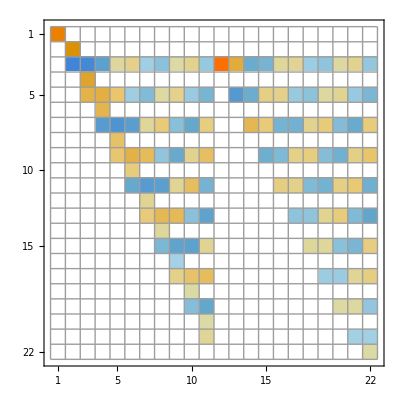

0

(⟨+|χ⟩ | ⟨-|χ⟩
⟨+|χ⟩ | ⟨-|χ⟩)

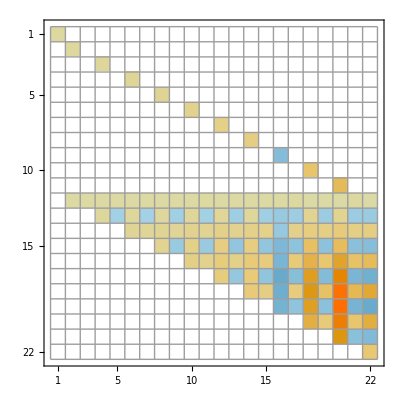

-8.32838×10^30

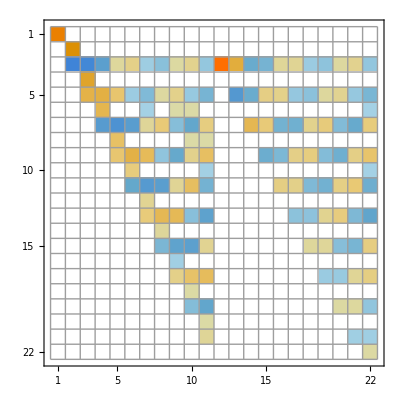

```mathematica
{{"⟨χ|+⟩","⟨χ|-⟩"},{"⟨χ|+⟩","⟨χ|-⟩"}}//TraditionalForm
MatrixPlot[Kleft,Mesh->All]
Det[Kleft]//Chop
{{"⟨+|χ⟩","⟨-|χ⟩"},{"⟨+|χ⟩","⟨-|χ⟩"}}//TraditionalForm
MatrixPlot[Chop[Kright,10^(-9)]//Transpose,Mesh->All]
Det[Chop[Kright,10^(-9)]]//Chop
(*KK={K[[1]],K[[2]],K[[4]],K[[6]],K[[8]],K[[10]],K[[12]],K[[14]],K[[16]],K[[18]],K[[20]],K[[3]],K[[5]],K[[7]],K[[9]],K[[11]],K[[13]],K[[15]],K[[17]],K[[19]],K[[21]],K[[22]]};
MatrixPlot[KK]
Table[KK[[i,i]],{i,Length[KK]}]*)
MatrixPlot[Chop[Kright,10^(-9)]//Transpose//Inverse,Mesh->All]
```